In this notebook we are solving the dispersion relation numerically and then graphically comparing it to the analytic approximation

```mathematica
Solve[1==d/(20000+87178),d]
```

```mathematica
Solve[14==d/(20000+87178),d]
```

```mathematica
Solve[1==d/(20000+22110.8),d]
```

```mathematica
Solve[14==d/(20000+22110.8),d]
```

```mathematica
ReplaceAll[ReplaceAll[1/Subscript[c, 2]^2-1/Subscript[c, 1]^2+(Subscript[γ̄, 1]^2 (1+√(1+(4 Subscript[c, 1]^2 ((kx^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2)))/(2  Subscript[c, 1]^2 (Subscript[c, 1]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 1]^2))+(Subscript[γ̄, 2]^2 (-1+√(1+(4  Subscript[c, 2]^2((kx^2+ky^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2)))/(2  Subscript[c, 2]^2 (Subscript[c, 2]^2 (Subscript[k, x]^2+Subscript[k, y]^2)+Subscript[γ̄, 2]^2)),{Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[γ̄, 2]->(γ+I*kx*U2) }],{U2->d+U1,Subscript[c, 1]->c1,Subscript[c, 2]->c2,Subscript[k, x]->kx,Subscript[k, y]->ky}]
```

```mathematica
Manipulate[NSolve[-1/Subscript[c, 1]^2+1/Subscript[c, 2]^2+((γ+ⅈ U1 kx)^2 (1+√(1+(4 Subscript[c, 1]^2 ((γ+ⅈ U1 kx)^2+Subscript[c, 1]^2 (kx^2+ky^2)))/g^2)))/(2 Subscript[c, 1]^2 ((γ+ⅈ U1 kx)^2+Subscript[c, 1]^2 (kx^2+ky^2)))+((γ+ⅈ U2 kx)^2 (-1+√(1+(4 Subscript[c, 2]^2 ((γ+ⅈ U2 kx)^2+Subscript[c, 2]^2 (kx^2+ky^2)))/g^2)))/(2 Subscript[c, 2]^2 ((γ+ⅈ U2 kx)^2+Subscript[c, 2]^2 (kx^2+ky^2)))==0,γ],{Subscript[c, 1],20000,25000},{Subscript[c, 2],22110.8,87178},{U1,15000,20000},{U2,57000,1500000},{kx,0.1,2},{ky,0,2},{g,10,1000}]
```

```mathematica
ClearAll[k]
```

## Calculate Numerical Roots for A=0.1

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=22110.8;
```

```mathematica
N[(c2^2-c1^2)/(c1^2+c2^2)]
```

```mathematica
hplus[g_,c2_,kx_,U2_,γ_]:=(g+√(g^2+4 c2^4 kx^2+4 c2^2 (γ+I*kx*U2)^2));
hminus[g_,c1_,kx_,U1_,γ_]:=(g-√(g^2+4 c1^4 K^2+4 c1^2 (γ+I*kx*U1)^2));
```

```mathematica
drange =Range[42000.,590000.,548];
```

```mathematica
a =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange}];
```

```mathematica
(*TableForm[a]*)
```

```mathematica
khroot = Flatten[Append[a[[1;;33,1]],a[[34;;All,3]]]];
rtroot=  Flatten[Append[a[[2;;33,3]],a[[34;;All,1]]]];
dvals = Table[d/(c1+c2),{d,drange}];
```

```mathematica
khrootdata = khroot[[All,2]]/(c1*kx);
khrootdata2 = khroot[[All,2]];
khapprox = Table[N[(g*c2)/(2*c1*d)/(c1*kx)],{d,drange}];
khimapprox = Table[N[-(U1 +c1)],{d,drange}];
```

```mathematica
data = Thread[{dvals,Abs[Re[khrootdata]]}];
dataim = Thread[{dvals,Im[khrootdata2]}];
data2 = Thread[{dvals,khapprox}];
data2im = Thread[{dvals,khimapprox}];
data3 = Thread[{dvals[[2;;All]],Abs[Re[rtrootdata]]}];
data4 = Thread[{dvals,rtapprox}];
```

### Plot KH

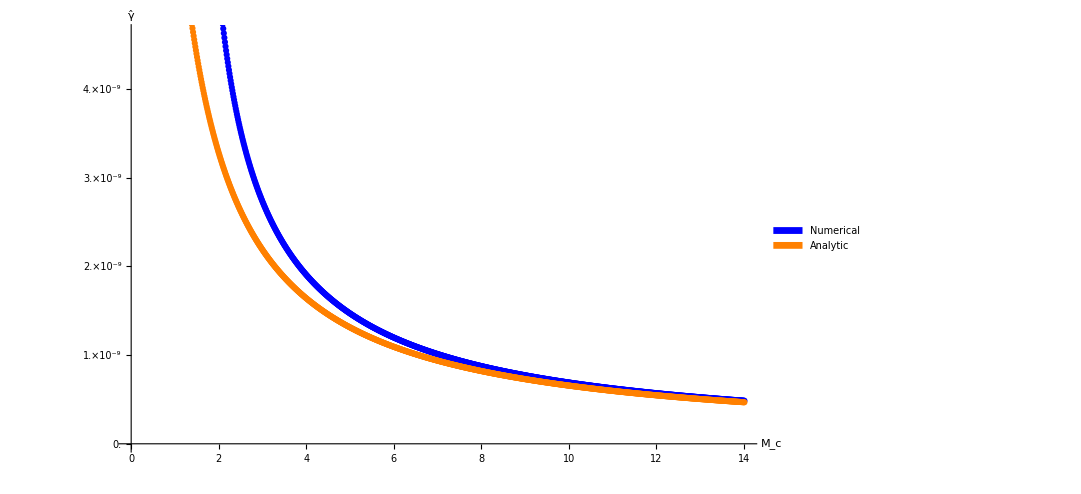

```mathematica
KHA001=ListPlot[{data,data2},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.000000006,0.0000000002],{#,ScientificForm@#}&/@Range[0,0.000000006,0.000000001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue, Orange},AxesStyle->Directive[24,Bold,Thick],ImageSize->800]
```

```mathematica
KHA0011=ListLogPlot[{data,data2},
Ticks->Automatic,
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue, Orange},
AxesStyle->Directive[24,Bold,Thick],
PlotRange->{{1.3,14},Automatic},
ImageSize->800]
```

```mathematica
KHA002=ListPlot[{dataim},
PlotRange->Full,
Ticks->Automatic,
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue, Orange},AxesStyle->Directive[24,Bold,Thick],ImageSize->800]
```

### Plot RT?

```mathematica
RTA001=ListPlot[{data3,data4}, 
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00008,0.0000005],{#,ScientificForm@#}&/@Range[0,0.000008,0.0000015]]},
AxesOrigin->{0,0},PlotRange->{0,0.0000085},
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue,Orange},
ImageSize->800,
AxesStyle->Directive[24,Thick,Bold]]
```

### Plot Relative Error KH

```mathematica
kherror = Abs[Abs[Re[khrootdata]]-khapprox]/Abs[Re[khrootdata]]*100;
kherrordata = Thread[{dvals,kherror}];
```

```mathematica
KHERA001=ListPlot[{kherrordata},
Joined->True,
AxesStyle->Directive[Bold,26,Thick],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
PlotStyle->{Directive[Black,Thickness[0.01]]},
Ticks->{Automatic,{10,20,30,40}},
GridLines->{{2,4,6,8,10,12,14},{5,10,15,20,25,30,35}},
GridLinesStyle->Directive[Blue,Dashed],
ImageSize->800];
```

### Plot Relative Error RT?

```mathematica
rterror = Abs[Abs[Re[rtrootdata]]-rtapprox[[2;;All]]]/Abs[Re[rtrootdata]]*100;
rterrordata = Thread[{dvals[[2;;All]],rterror}];
```

```mathematica
RTERA001=ListPlot[{rterrordata},
Joined->True,
AxesStyle->Directive[Bold,26,Thick],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
PlotStyle->{Directive[Black,Thickness[0.01]]},
GridLines->{{2,4,6,8,10,12,14},{2,4,6,8,10,12}},
GridLinesStyle->Directive[Blue,Dashed],
ImageSize->800];
```

### Getting plot insert

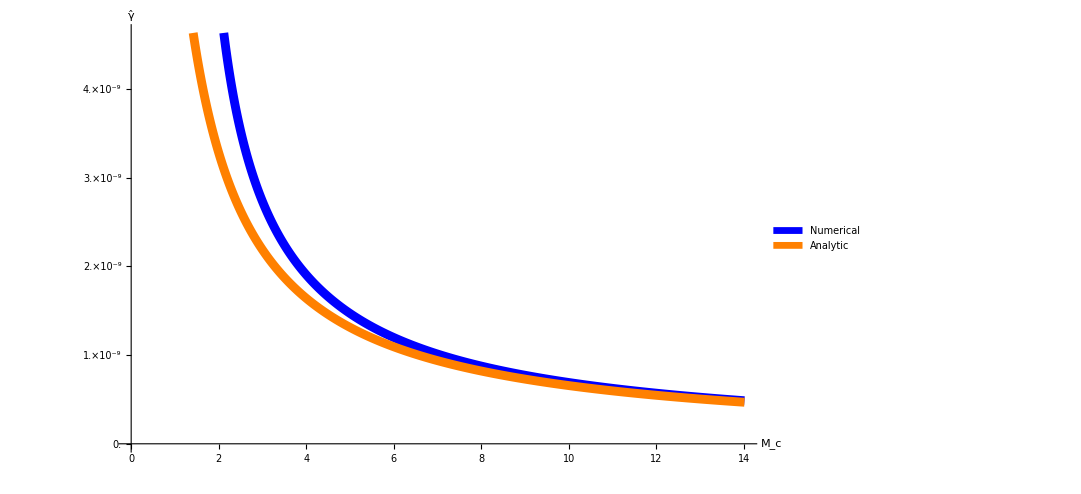

```mathematica
KHA001=ListPlot[{data,data2},
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.000000006,0.0000000002],{#,ScientificForm@#}&/@Range[0,0.000000006,0.000000001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
AxesStyle->Directive[24,Bold,Thick],
ImageSize->800,
Epilog->Inset[KHERA001,Scaled[{1,1}],{Right,Top},Scaled[{0.75,0.75}]]]
```

```mathematica
Export["KH_A_0.1_Full_3.eps",KHA001,"EPS"]
```

KH_A_0.1_Full_3.eps

```mathematica
RTA001=ListPlot[{data3,data4}, 
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00008,0.0000005],{#,ScientificForm@#}&/@Range[0,0.000008,0.0000015]]},
AxesOrigin->{0,8.25*10^-6},
PlotRange->{0,0.0000085},
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
ImageSize->800,
AxesStyle->Directive[24,Thick,Bold],
Epilog->Inset[RTERA001,Scaled[{0.17,0.05}],{Left,Bottom},Scaled[{0.76,0.76}]]
]
```

```mathematica
Export["RT_A_0.1_Full_3.eps",RTA001,"EPS"]
```

### Getting More Data for Absolute Error With log spacing

```mathematica
lnspace[a_,b_,n_]:=N[Exp[1]^Range[a,b,(b-a)/(n-1)]];
```

```mathematica
logrange = lnspace[13.29,16,1000];
fullrange = Join[drange,logrange];
```

```mathematica
a =ParallelTable[NSolve[SetPrecision[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0,200],WorkingPrecision->200],{d,fullrange}];
```

```mathematica
khroot = Flatten[Append[a[[1;;33,1]],a[[34;;All,3]]]];
rtroot=  Flatten[Append[a[[2;;33,3]],a[[34;;All,1]]]];
dvals = Table[d/(c1+c2),{d,fullrange}];
```

```mathematica
khrootdata = khroot[[All,2]]/Sqrt[g*kx];
rtrootdata = rtroot[[All,2]]/Sqrt[g*kx];
khapprox = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,fullrange}];
rtapprox = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,fullrange}];
```

```mathematica
khabserror = Abs[Abs[Re[khrootdata]]-khapprox];
rtabserror=Abs[Abs[Re[rtrootdata]]-rtapprox[[2;;All]]];
```

```mathematica
khabserrordata = Thread[{1/dvals,khabserror}];
rtabserrordata= Thread[{1/dvals[[2;;All]],rtabserror}];
```

#### KH Abs Error Plot

```mathematica
ListLogLogPlot[khabserrordata,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange},PlotRange->{{4*10^-3,0.7},{3*10^-10,10^-3}}]
```

#### RT Abs Error Plot

```mathematica
ListLogLogPlot[rtabserrordata,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange}]
```

```mathematica
Manipulate[N[(Log[rtabserrordata[[x,2]]]-Log[rtabserrordata[[2000,2]]])/(Log[rtabserrordata[[x,1]]]-Log[rtabserrordata[[2000,1]]])],{x,400,2000}]
```

## Calculate Numerical roots for A=0.9

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
d2range =Range[107178,1500492,1340];
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

```mathematica
(*TableForm[a2]*)
```

```mathematica
a2[[100]]
```

{{γ→-0.00017234-59755.1 ⅈ},{γ→0.00017234-59755.1 ⅈ},{γ→-0.000102929-36820.4 ⅈ},{γ→0.000102929-36820.4 ⅈ}}

```mathematica
khroot2 = Flatten[Append[a2[[1;;34,1]],a2[[35;;All,3]]]];
rtroot2=  Flatten[Append[a2[[1;;34,3]],a2[[35;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,d2range}];
```

```mathematica
khrootdata2 = khroot2[[All,2]]/(c1*kx);
khrootdata2im = khroot2[[All,2]];
rtrootdata2 = rtroot2[[All,2]]/Sqrt[g*kx];
khapprox2 = Table[N[(g*c2)/(2*c1*d)/(c1*kx)],{d,d2range}];
khapprox2im = Table[N[-c1-U1],{d,d2range}];
rtapprox2 = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,d2range}];
```

```mathematica
data5 = Thread[{dvals2,Abs[Re[khrootdata2]]}];
data5im = Thread[{dvals2,Im[khrootdata2im]}];
data6 = Thread[{dvals2,khapprox2}];
data6im = Thread[{dvals2,khapprox2im}];
data7 = Thread[{dvals2,Abs[Re[rtrootdata2]]}];
data8 = Thread[{dvals2,rtapprox2}];
```

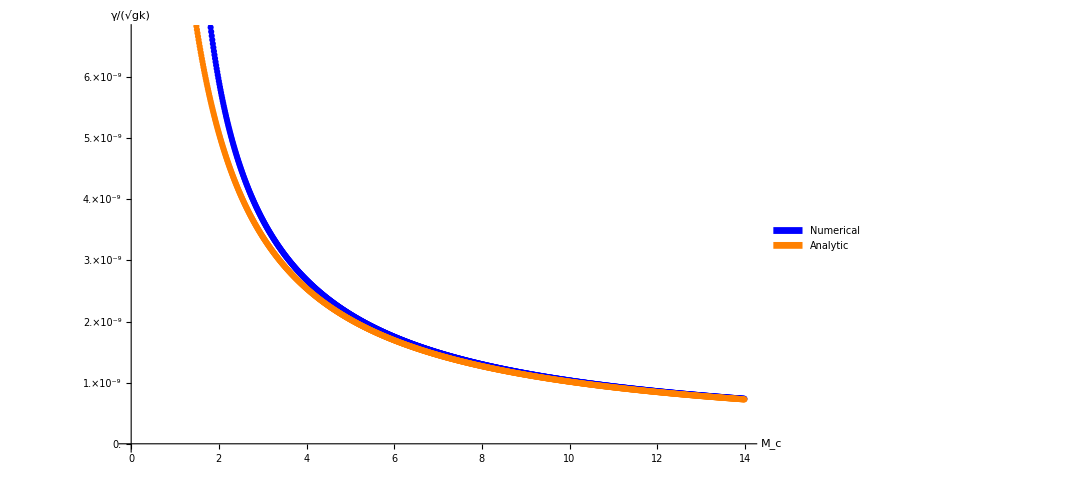

```mathematica
ListPlot[{data5,data6},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.000000007,0.0000000002],{#,ScientificForm@#}&/@Range[0,0.000000006,0.000000001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Blue, Orange},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
ImageSize->800]
```

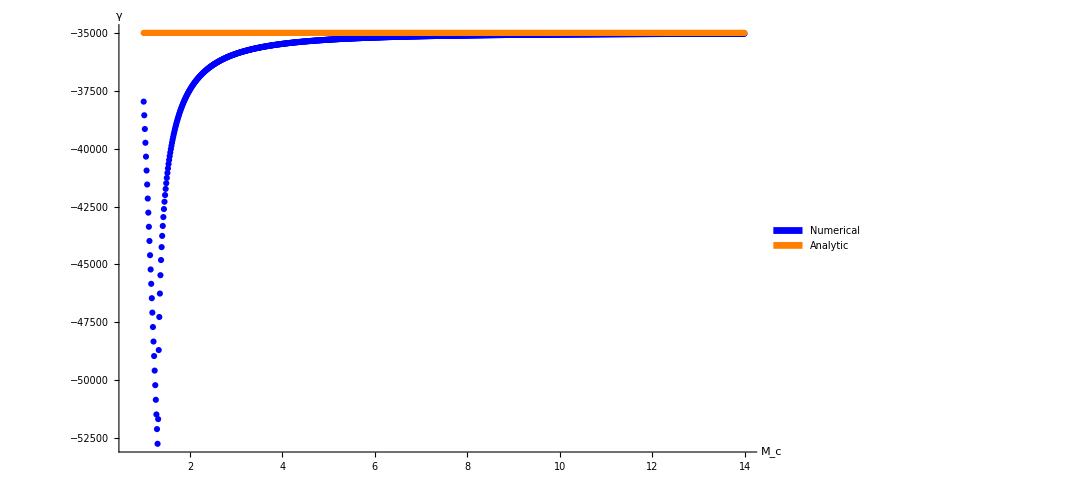

```mathematica
ListPlot[{data5im,data6im},
PlotRange->Full,
Ticks->Automatic,
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Blue, Orange},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
ImageSize->800]
```

```mathematica
ip={{50,60},{40,45}};
```

```mathematica
plot1=ListPlot[{data5,data6},
ImagePadding->ip;
PlotLegends->{Style["Numerical",Bold,22],Style["Analytic",Bold, 22]},
PlotStyle->{Blue, Orange},
FrameStyle->Directive[14,Bold,Thick,Black],
FrameLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
FrameTicks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00005,0.000001],{#,ScientificForm@#}&/@Range[0,0.00005,0.000005]]},
Frame->{True,True,True,False},
ImageSize->800];
```

```mathematica
plot2=ListPlot[{kherrordata2},
PlotLegends->{Style["Relative Error",Bold,22]},
ImagePadding->ip;
PlotStyle->Pink,
FrameStyle->Directive[14,Bold,Thick,Red],
FrameLabel->{{"",Style[Subscript[γ, RelativeError],Large,Bold,Blue]},{"",""}},
FrameTicks->{{False,All},{False,False}},
Frame->{False,False,False,True},
ImageSize->800];
```

```mathematica
ListPlot[{data7,data8},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00006,0.000005],{#,ScientificForm@#}&/@Range[0,0.00006,0.00001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotLegends->{Style[Numerical,Bold],Style[Analytic,Bold]},
PlotStyle->{Blue, Orange},AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
ImageSize->800]
```

```mathematica
kherror2 = Abs[Abs[Re[khrootdata2]]-khapprox2]/Abs[Re[khrootdata2]]*100;
kherrordata2 = Thread[{dvals2,kherror2}];
```

```mathematica
KHERA09=ListPlot[{kherrordata2},
Joined->True,
PlotStyle->{Directive[Black,Thickness[0.01]]},
GridLinesStyle->Directive[Blue,Dashed],
AxesStyle->Directive[Bold,26,Thick],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
GridLines->{{2,4,6,8,10,12,14},{2,4,6,8,10,12,14}},
ImageSize->800];
```

```mathematica
rterror2 = Abs[Abs[Re[rtrootdata2]]-rtapprox2]/Abs[Re[rtrootdata2]]*100;
rterrordata2=Thread[{dvals2,rterror2}];
```

```mathematica
RTERA09=ListPlot[{rterrordata2},
Joined->True,
PlotStyle->{Directive[Black,Thickness[0.01]]},
AxesStyle->Directive[Bold,26,Thick],
GridLinesStyle->Directive[Blue,Dashed],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
GridLines->{{2,4,6,8,10,12,14},{2,4,6,8,10,12}},
ImageSize->800];
```

### Plot Inserts

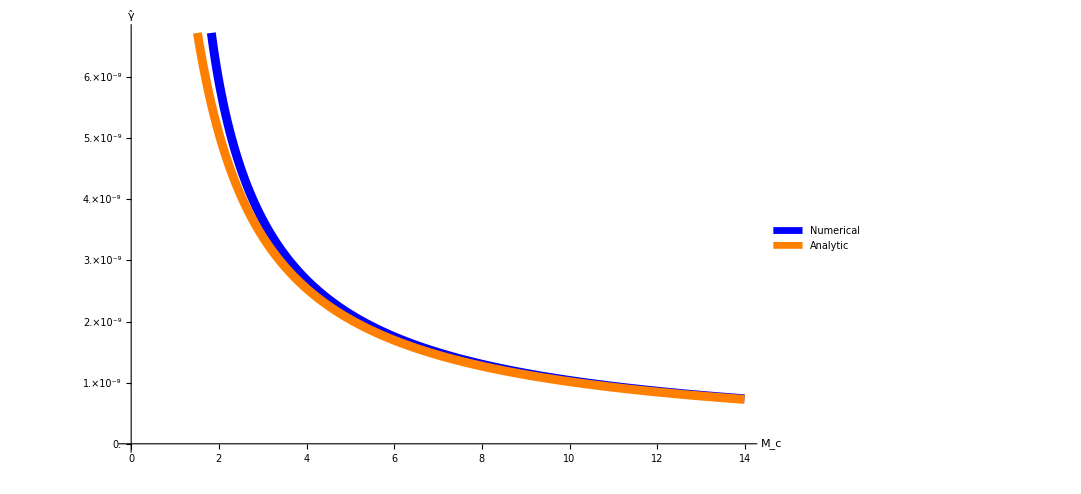

```mathematica
KHA09=ListPlot[{data5,data6},
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.000000007,0.0000000002],{#,ScientificForm@#}&/@Range[0,0.000000006,0.000000001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
ImageSize->800,
Epilog->Inset[KHERA09,Scaled[{1,1}],{Right,Top},Scaled[{0.75,0.75}]]]
```

```mathematica
Export["KH_A_0.9_Full_3.eps",KHA09,"EPS"]
```

KH_A_0.9_Full_3.eps

```mathematica
RTA09=ListPlot[{data7,data8},
Joined->True,
AxesOrigin->{0,6.75*10^-5},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00006,0.000005],{#,ScientificForm@#}&/@Range[0,0.00006,0.00001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotLegends->{Style["Numerical",Bold],Style["Analytic",Bold]},
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
ImageSize->800,
Epilog->Inset[RTERA09,Scaled[{0.17,0.05}],{Left,Bottom},Scaled[{0.76,0.76}]]
]
```

```mathematica
Export["RT_A_0.9_Full_3.eps",RTA09,"EPS"]
```

### Getting More Data for Absolute Error With log spacing

```mathematica
log2range = lnspace[14.221303612292198,17,1000];
full2range = Join[d2range,logrange];
```

```mathematica
a2 =ParallelTable[NSolve[SetPrecision[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0,200],WorkingPrecision->200],{d,full2range}];
```

```mathematica
khroot2 = Flatten[Append[a2[[1;;34,1]],a2[[35;;All,3]]]];
rtroot2=  Flatten[Append[a2[[1;;34,3]],a2[[35;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,full2range}];
```

```mathematica
khrootdata2 = khroot2[[All,2]]/Sqrt[g*kx];
rtrootdata2 = rtroot2[[All,2]]/Sqrt[g*kx];
khapprox2 = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,full2range}];
rtapprox2 = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,full2range}];
```

```mathematica
kh2abserror = Abs[Abs[Re[khrootdata2]]-khapprox2];
rt2abserror=Abs[Abs[Re[rtrootdata2]]-rtapprox2];
```

```mathematica
khabserrordata2 = Thread[{1/dvals2,kh2abserror}];
rtabserrordata2= Thread[{1/dvals2,rt2abserror}];
```

#### Plot KH Abs Error

```mathematica
ListLogLogPlot[khabserrordata2,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange},PlotRange->{{1*10^-2,0.7},{1*10^-9,10^-3}}]
```

```mathematica
Manipulate[N[(Log[khabserrordata2[[x,2]]]-Log[khabserrordata2[[2000,2]]])/(Log[khabserrordata2[[x,1]]]-Log[khabserrordata2[[2000,1]]])],{x,400,2000}]
```

#### RT Abs Error Plot

```mathematica
ListLogLogPlot[rtabserrordata2,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange}]
```

```mathematica
Manipulate[N[(Log[rtabserrordata2[[x,2]]]-Log[rtabserrordata2[[2000,2]]])/(Log[rtabserrordata2[[x,1]]]-Log[rtabserrordata2[[2000,1]]])],{x,400,2000}]
```

## B or β plots

Data should have the form of [ρ1, ρ2, P, c1, c2, U1, d, Mc(8), g, kx, ky, B(12), β(13), Re(γ), Im(γ)] (15 items)

```mathematica
plotdatakh500 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatakh600 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatakh700 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatakh800 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatakh900 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatakh1000 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart500 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart600 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart700 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart800 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart900 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdatart1000 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotdata400 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
bcrit={Last[plotdatart500][[12]],Last[plotdatart600][[12]],Last[plotdatart700][[12]],Last[plotdatart800][[12]],Last[plotdatart900][[12]],Last[plotdatart1000][[12]]};
bcrit2 = bcrit*bcrit*(4*π*10^-7);
dcrit={Last[plotdatakh500][[7]],Last[plotdatakh600][[7]],Last[plotdatakh700][[7]],Last[plotdatakh800][[7]],Last[plotdatakh900][[7]],Last[plotdatakh1000][[7]]};
testdata=Thread[{dcrit,bcrit}];
```

#### KH data allocation

```mathematica
plotb500 = plotdatakh500[[;;,12]];
plotbeta500=plotdatakh500[[;;,13]];
plotgamma500 = Abs[plotdatakh500[[;;,14]]];
plotgammaim500=plotdatakh500[[;;,15]];
betadata500=Thread[{plotbeta500,plotgammanorm500}];
bdata500 = Thread[{plotb500,plotgamma500}];
bdataim500 = Thread[{plotb500,plotgammaim500}];
plotb500norm  = plotdatakh500[[;;,12]]/√(4*π*10^-7*(plotdatakh500[[1]][[1]]+plotdatakh500[[1]][[2]]))*(1/500000);
plotb500norm2 = plotdatakh500[[;;,12]]/√(4*π*10^-7*(plotdatakh500[[1]][[2]]))*(1/(500000-plotdatakh500[[1]][[4]]));
plotb500norm3 = (plotdatakh500[[;;,12]]/√(4*π*10^-7*(plotdatakh500[[1]][[2]]))+plotdatakh500[[;;,12]]/√(4*π*10^-7*(plotdatakh500[[1]][[1]])))*(1/500000);
plotgammanorm500=Abs[plotdatakh500[[;;,14]]/(plotdatakh500[[;;,4]]*plotdatakh500[[;;,10]])];
bdata500norm = Thread[{plotb500norm,plotgammanorm500}];
bdata500norm2 = Thread[{plotb500norm2,plotgammanorm500}];
bdata500norm3 = Thread[{plotb500norm3,plotgammanorm500}];
```

```mathematica
plotb600 = plotdatakh600[[;;,12]];
plotbeta600=plotdatakh600[[;;,13]];
plotgamma600 =Abs[ plotdatakh600[[;;,14]]];
plotgammaim600=plotdatakh600[[;;,15]];
plotgammanorm600=Abs[plotdatakh600[[;;,14]]/Sqrt[10]];
betadata600=Thread[{plotbeta600,plotgammanorm600}];
bdata600 = Thread[{plotb600,plotgamma600}];
bdataim600 = Thread[{plotb600,plotgammaim600}];
plotb600norm  = plotdatakh600[[;;,12]]/√(4*π*10^-7*(plotdatakh600[[1]][[1]]+plotdatakh600[[1]][[2]]))*(1/600000);
plotb600norm2  = plotdatakh600[[;;,12]]/√(4*π*10^-7*(plotdatakh600[[1]][[2]]))*(1/(600000-plotdatakh600[[1]][[4]]));
plotb600norm3  =( plotdatakh600[[;;,12]]/√(4*π*10^-7*(plotdatakh600[[1]][[2]]))+plotdatakh600[[;;,12]]/√(4*π*10^-7*(plotdatakh600[[1]][[1]])))*(1/600000);
plotgammanorm600=Abs[plotdatakh600[[;;,14]]/(plotdatakh600[[;;,4]]*plotdatakh600[[;;,10]])];
bdata600norm = Thread[{plotb600norm,plotgammanorm600}];
bdata600norm2 = Thread[{plotb600norm2,plotgammanorm600}];
bdata600norm3 = Thread[{plotb600norm3,plotgammanorm600}];
```

```mathematica
plotb700 = plotdatakh700[[;;,12]];
plotbeta700=plotdatakh700[[;;,13]];
plotgamma700 =Abs[ plotdatakh700[[;;,14]]];
plotgammaim700=plotdatakh700[[;;,15]];
plotgammanorm700=Abs[plotdatakh700[[;;,14]]/Sqrt[10]];
betadata700=Thread[{plotbeta700,plotgammanorm700}];
bdata700 = Thread[{plotb700,plotgamma700}];
bdataim700 = Thread[{plotb700,plotgammaim700}];
plotb700norm  = plotdatakh700[[;;,12]]/√(4*π*10^-7*(plotdatakh700[[1]][[1]]+plotdatakh700[[1]][[2]]))*(1/700000);
plotb700norm2  = plotdatakh700[[;;,12]]/√(4*π*10^-7*(plotdatakh700[[1]][[2]]))*(1/(700000-plotdatakh700[[1]][[4]]));
plotb700norm3  = (plotdatakh700[[;;,12]]/√(4*π*10^-7*(plotdatakh700[[1]][[2]]))+plotdatakh700[[;;,12]]/√(4*π*10^-7*(plotdatakh700[[1]][[1]])))*(1/700000);
plotgammanorm700=Abs[plotdatakh700[[;;,14]]/(plotdatakh700[[;;,4]]*plotdatakh700[[;;,10]])];
bdata700norm = Thread[{plotb700norm,plotgammanorm700}];
bdata700norm2 = Thread[{plotb700norm2,plotgammanorm700}];
bdata700norm3 = Thread[{plotb700norm3,plotgammanorm700}];
```

```mathematica
plotb800 = plotdatakh800[[;;,12]];
plotbeta800=plotdatakh800[[;;,13]];
plotgamma800 = Abs[plotdatakh800[[;;,14]]];
plotgammaim800=plotdatakh800[[;;,15]];
plotgammanorm800=Abs[plotdatakh800[[;;,14]]/Sqrt[10]];
betadata800=Thread[{plotbeta800,plotgammanorm800}];
bdata800 = Thread[{plotb800,plotgamma800}];
bdataim800 = Thread[{plotb800,plotgammaim800}];
plotb800norm  = plotdatakh800[[;;,12]]/√(4*π*10^-7*(plotdatakh800[[1]][[1]]+plotdatakh800[[1]][[2]]))*(1/800000);
plotb800norm2  = plotdatakh800[[;;,12]]/√(4*π*10^-7*(plotdatakh800[[1]][[2]]))*(1/(800000-plotdatakh800[[1]][[4]]));
plotb800norm3  = (plotdatakh800[[;;,12]]/√(4*π*10^-7*(plotdatakh800[[1]][[2]]))+plotdatakh800[[;;,12]]/√(4*π*10^-7*(plotdatakh800[[1]][[1]])))*(1/800000);
plotgammanorm800=Abs[plotdatakh800[[;;,14]]/(plotdatakh800[[;;,4]]*plotdatakh800[[;;,10]])];
bdata800norm = Thread[{plotb800norm,plotgammanorm800}];
bdata800norm2 = Thread[{plotb800norm2,plotgammanorm800}];
bdata800norm3 = Thread[{plotb800norm3,plotgammanorm800}];
```

```mathematica
plotb900 = plotdatakh900[[;;,12]];
plotbeta900=plotdatakh900[[;;,13]];
plotgamma900 = Abs[plotdatakh900[[;;,14]]];
plotgammaim900=plotdatakh900[[;;,15]];
plotgammanorm900=Abs[plotdatakh900[[;;,14]]/Sqrt[10]];
betadata900=Thread[{plotbeta900,plotgammanorm900}];
bdata900 = Thread[{plotb900,plotgamma900}];
bdataim900 = Thread[{plotb900,plotgammaim900}];
plotb900norm  = plotdatakh900[[;;,12]]/√(4*π*10^-7*(plotdatakh900[[1]][[1]]+plotdatakh900[[1]][[2]]))*(1/900000);
plotb900norm2  = plotdatakh900[[;;,12]]/√(4*π*10^-7*(plotdatakh900[[1]][[2]]))*(1/(900000-plotdatakh900[[1]][[4]]));
plotb900norm3  = (plotdatakh900[[;;,12]]/√(4*π*10^-7*(plotdatakh900[[1]][[2]]))+plotdatakh900[[;;,12]]/√(4*π*10^-7*(plotdatakh900[[1]][[1]])))*(1/900000);
plotgammanorm900=Abs[plotdatakh900[[;;,14]]/(plotdatakh900[[;;,4]]*plotdatakh900[[;;,10]])];
bdata900norm = Thread[{plotb900norm,plotgammanorm900}];
bdata900norm2 = Thread[{plotb900norm2,plotgammanorm900}];
bdata900norm3 = Thread[{plotb900norm3,plotgammanorm900}];
```

```mathematica
plotb1000 = plotdatakh1000[[;;,12]];
plotbeta1000=plotdatakh1000[[;;,13]];
plotgamma1000 = Abs[plotdatakh1000[[;;,14]]];
plotgammaim1000=plotdatakh1000[[;;,15]];
plotgammanorm1000=Abs[plotdatakh1000[[;;,14]]/Sqrt[10]];
betadata1000=Thread[{plotbeta1000,plotgammanorm1000}];
bdata1000 = Thread[{plotb1000,plotgamma1000}];
bdataim1000 = Thread[{plotb1000,plotgammaim1000}];
plotb1000norm  = plotdatakh1000[[;;,12]]/√(4*π*10^-7*(plotdatakh1000[[1]][[1]]+plotdatakh1000[[1]][[2]]))*(1/1000000);
plotb1000norm2  = plotdatakh1000[[;;,12]]/√(4*π*10^-7*(plotdatakh1000[[1]][[2]]))*(1/(1000000-plotdatakh1000[[1]][[4]]));
plotb1000norm3  = (plotdatakh1000[[;;,12]]/√(4*π*10^-7*(plotdatakh1000[[1]][[2]]))+plotdatakh1000[[;;,12]]/√(4*π*10^-7*(plotdatakh1000[[1]][[1]])))*(1/1000000);
plotgammanorm1000=Abs[plotdatakh1000[[;;,14]]/(plotdatakh1000[[;;,4]]*plotdatakh1000[[;;,10]])];
bdata1000norm = Thread[{plotb1000norm,plotgammanorm1000}];
bdata1000norm2 = Thread[{plotb1000norm2,plotgammanorm1000}];
bdata1000norm3 = Thread[{plotb1000norm3,plotgammanorm1000}];
```

#### RT Data

```mathematica
plotb500 = plotdatart500[[;;,12]];
plotbeta500=plotdatart500[[;;,13]];
plotgamma500 = Abs[plotdatart500[[;;,14]]];
plotgammaim500=plotdatart500[[;;,15]];
plotgammanorm500=Abs[plotdatart500[[;;,14]]/Sqrt[10]];
betadata500=Thread[{plotbeta500,plotgammanorm500}];
bdata500 = Thread[{plotb500,plotgamma500}];
bdataim500 = Thread[{plotb500,plotgammaim500}];
plotb500norm  = plotdatart500[[;;,12]]/√(4*π*10^-7*(plotdatart500[[1]][[1]]+plotdatart500[[1]][[2]]))*(1/500000);
plotgammanorm500=Abs[plotdatart500[[;;,14]]/Sqrt[10]];
bdata500norm = Thread[{plotb500norm,plotgammanorm500}];
```

```mathematica
plotb600 = plotdatart600[[;;,12]];
plotbeta600=plotdatart600[[;;,13]];
plotgamma600 =Abs[ plotdatart600[[;;,14]]];
plotgammaim600=plotdatart600[[;;,15]];
plotgammanorm600=Abs[plotdatart600[[;;,14]]/Sqrt[10]];
betadata600=Thread[{plotbeta600,plotgammanorm600}];
bdata600 = Thread[{plotb600,plotgamma600}];
bdataim600 = Thread[{plotb600,plotgammaim600}];
plotb600norm  = plotdatart600[[;;,12]]/√(4*π*10^-7*(plotdatart600[[1]][[1]]+plotdatart600[[1]][[2]]))*(1/600000);
plotgammanorm600=Abs[plotdatart600[[;;,14]]/Sqrt[10]];
bdata600norm = Thread[{plotb600norm,plotgammanorm600}];
```

```mathematica
plotb700 = plotdatart700[[;;,12]];
plotbeta700=plotdatart700[[;;,13]];
plotgamma700 =Abs[ plotdatart700[[;;,14]]];
plotgammaim700=plotdatart700[[;;,15]];
plotgammanorm700=Abs[plotdatart700[[;;,14]]/Sqrt[10]];
betadata700=Thread[{plotbeta700,plotgammanorm700}];
bdata700 = Thread[{plotb700,plotgamma700}];
bdataim700 = Thread[{plotb700,plotgammaim700}];
plotb700norm  = plotdatart700[[;;,12]]/√(4*π*10^-7*(plotdatart700[[1]][[1]]+plotdatart700[[1]][[2]]))*(1/700000);
plotgammanorm700=Abs[plotdatart700[[;;,14]]/Sqrt[10]];
bdata700norm = Thread[{plotb700norm,plotgammanorm700}];
```

```mathematica
plotb800 = plotdatart800[[;;,12]];
plotbeta800=plotdatart800[[;;,13]];
plotgamma800 = Abs[plotdatart800[[;;,14]]];
plotgammaim800=plotdatart800[[;;,15]];
plotgammanorm800=Abs[plotdatart800[[;;,14]]/Sqrt[10]];
betadata800=Thread[{plotbeta800,plotgammanorm800}];
bdata800 = Thread[{plotb800,plotgamma800}];
bdataim800 = Thread[{plotb800,plotgammaim800}];
plotb800norm  = plotdatart800[[;;,12]]/√(4*π*10^-7*(plotdatart800[[1]][[1]]+plotdatart800[[1]][[2]]))*(1/800000);
plotgammanorm800=Abs[plotdatart800[[;;,14]]/Sqrt[10]];
bdata800norm = Thread[{plotb800norm,plotgammanorm800}];
```

```mathematica
plotb900 = plotdatart900[[;;,12]];
plotbeta900=plotdatart900[[;;,13]];
plotgamma900 = Abs[plotdatart900[[;;,14]]];
plotgammaim900=plotdatart900[[;;,15]];
plotgammanorm900=Abs[plotdatart900[[;;,14]]/Sqrt[10]];
betadata900=Thread[{plotbeta900,plotgammanorm900}];
bdata900 = Thread[{plotb900,plotgamma900}];
bdataim900 = Thread[{plotb900,plotgammaim900}];
plotb900norm  = plotdatart900[[;;,12]]/√(4*π*10^-7*(plotdatart900[[1]][[1]]+plotdatart900[[1]][[2]]))*(1/900000);
plotgammanorm900=Abs[plotdatart900[[;;,14]]/Sqrt[10]];
bdata900norm = Thread[{plotb900norm,plotgammanorm900}];
```

```mathematica
plotb1000 = plotdatart1000[[;;,12]];
plotbeta1000=plotdatart1000[[;;,13]];
plotgamma1000 = Abs[plotdatart1000[[;;,14]]];
plotgammaim1000=plotdatart1000[[;;,15]];
plotgammanorm1000=Abs[plotdatart1000[[;;,14]]/Sqrt[10]];
betadata1000=Thread[{plotbeta1000,plotgammanorm1000}];
bdata1000 = Thread[{plotb1000,plotgamma1000}];
bdataim1000 = Thread[{plotb1000,plotgammaim1000}];
plotb1000norm=plotdatart1000[[;;,12]]/√(4*π*10^-7*(plotdatart1000[[1]][[1]]+plotdatart1000[[1]][[2]]))*(1/1000000);
plotgammanorm1000=Abs[plotdatart1000[[;;,14]]/Sqrt[10]];
bdata1000norm=Thread[{plotb1000norm,plotgammanorm1000}];
```

```mathematica
plotdatart1000[[1]]
```

```mathematica
N[1/(3/10000000/(1/12500000))]
```

```mathematica
N[1/(50000/25819.9)]
```

```mathematica
N[(3/10000000-1/12500000)/(3/10000000+1/12500000)]
```

```mathematica
plotb400 = plotdata400[[;;,12]];
plotbeta400=plotdata400[[;;,13]];
plotgamma400 = Abs[plotdata400[[;;,14]]];
plotgamma400norm=Abs[plotdata400[[;;,14]]/Sqrt[10]];
betadata400=Thread[{plotbeta400,plotgamma400norm}];
bdata400= Thread[{plotb400,plotgamma400}];
```

```mathematica
ListPlot[bdataim,PlotRange->{{0,0.15},{-26000,-25600}},
ImageSize->800]
```

```mathematica
ListPlot[betadata,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.000004,0.00000025],{#,ScientificForm@#}&/@Range[0,0.000004,0.000001]]},
PlotStyle->{Blue,PointSize[0.005]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[β,Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{.5*10^-6,1*10^-6,1.5*10^-6,2*10^-6,2.5*10^-6,3*10^-6,3.5*10^-6,4*10^-6}},
PlotRange->{{0,1.05},{0,0.0000042}},
ImageSize->800]
```

```mathematica
ListLogLogPlot[betadata,
Ticks->{Table[{10^k,Superscript[10,k]},{k,-2,5}],Automatic},
PlotStyle->{Blue,PointSize[0.005]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[β,Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.01,0.1,1,10,100,1000,10000,100000},Automatic},
PlotRange->{{0.005,200000},{1*10^-9,1.5*10^-5}},
ImageSize->800]
```

```mathematica
ListPlot[betadata400,
PlotRange->{{0,1},{0,0.00002}},
ImageSize->800]
```

```mathematica
ListPlot[betadataall,
ImageSize->800]
```

```mathematica
ListPlot[bdata,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000025],{#,ScientificForm@#}&/@Range[0,0.00002,0.000005]]},
PlotStyle->{Blue,PointSize[0.005]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[B,Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.10,0.11,0.12,0.13,0.14,0.15},{2.5*10^-6,5*10^-6,7.5*10^-6,1*10^-5,1.25*10^-5,1.5*10^-5,1.75*10^-5,2*10^-5}},
ImageSize->800]
```

```mathematica
ListPlot[bdataall,ImageSize->800]
```

```mathematica
ListPlot[bdata400,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.0001,0.0000125],{#,ScientificForm@#}&/@Range[0,0.0001,0.000025]]},
PlotStyle->{Blue,PointSize[0.005]},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[B,Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.10},{1.25*10^-5,2.5*10^-5,3.75*10^-5,5*10^-5,6.25*10^-5,7.5*10^-5,8.75*10^-5,1*10^-4}},
PlotRange->{Automatic,{0,0.000105}},ImageSize->800]
```

```mathematica
FindFormula[testdata,d,5,All]
```

### Here we plot the multi list plots

First the KH plot

```mathematica
8.9,10.7,12.4,14.2,16,17.8
```

```mathematica
SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
```

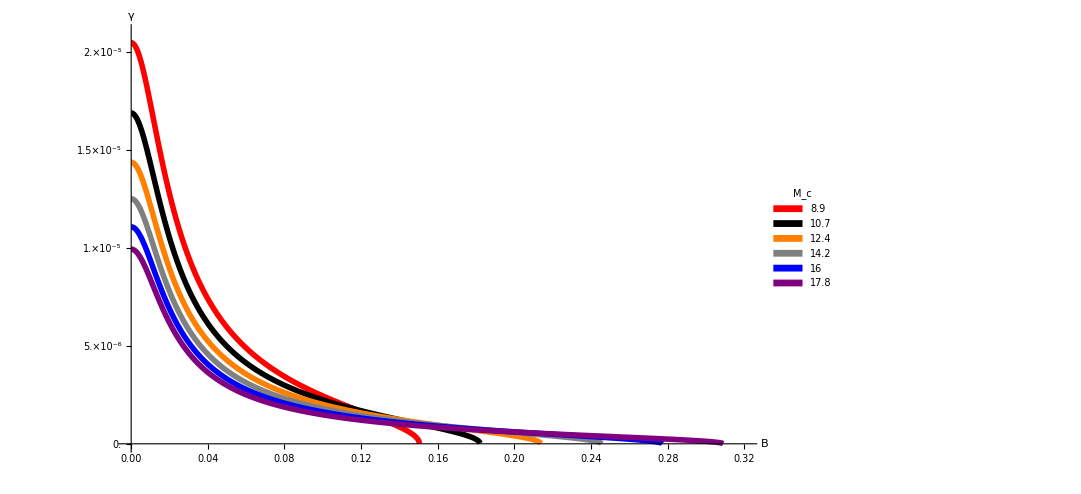

```mathematica
khplot1=ListPlot[{bdata500,bdata600,bdata700,bdata800,bdata900,bdata1000},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000025],{#,ScientificForm@#}&/@Range[0,0.00002,0.000005]]},
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[B,Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.025,0.05,0.075,0.10,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3},{2.5*10^-6,5*10^-6,7.5*10^-6,1*10^-5,1.25*10^-5,1.5*10^-5,1.75*10^-5,2*10^-5}},
PlotRange->{{0.000001,0.32},{0,0.000021}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
khplot1=ListPlot[{bdata500,bdata600,bdata700,bdata800,bdata900,bdata1000},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000025],{#,ScientificForm@#}&/@Range[0,0.00002,0.000005]]},
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[B,Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
PlotRange->{{0.000001,0.32},{0,0.000021}},
ImageSize->800,
MaxPlotPoints->1000]
```

-Graphics-

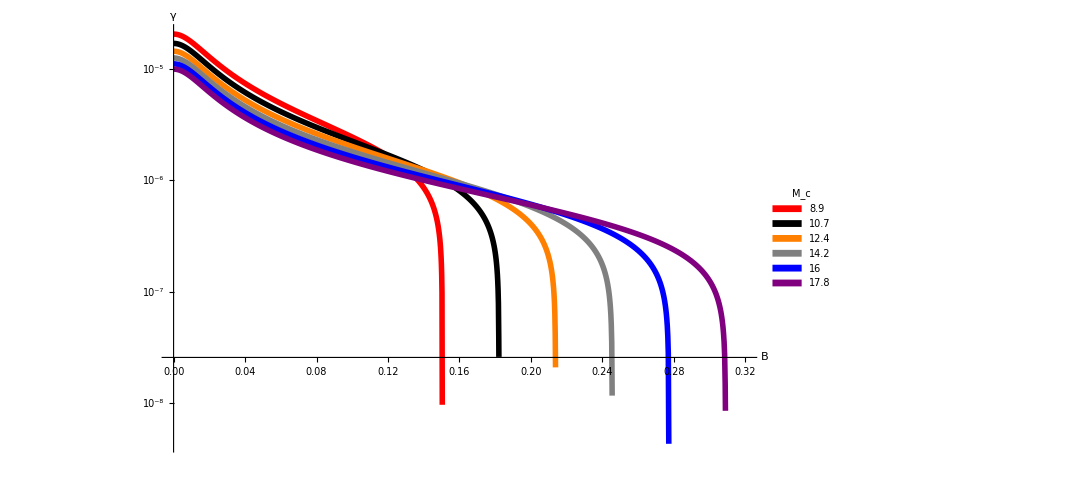

```mathematica
khplot1=ListLogPlot[{bdata500,bdata600,bdata700,bdata800,bdata900,bdata1000},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000025],{#,ScientificForm@#}&/@Range[0,0.00002,0.000005]]},
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[B,Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
PlotRange->{{0.000001,0.32},{0,0.000021}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["KH_multiplot_B.eps",khplot1,"EPS"]
```

KH_multiplot_B.eps

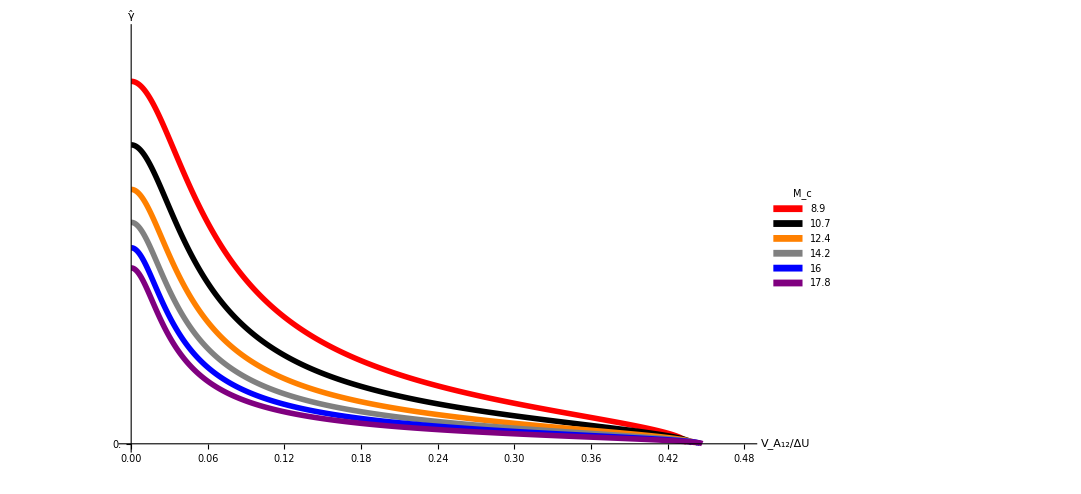

```mathematica
khplot2=ListPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000005],{#,ScientificForm@#}&/@Range[0,0.00002,0.0000015]]},
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.10,0.2,0.3,0.4,0.5},{1.5*10^-10,3*10^-10,4.5*10^-10,6*10^-10}},
PlotRange->{{0.000001,0.48},{0,0.0000000009}},
ImageSize->800,
MaxPlotPoints->1000]
```

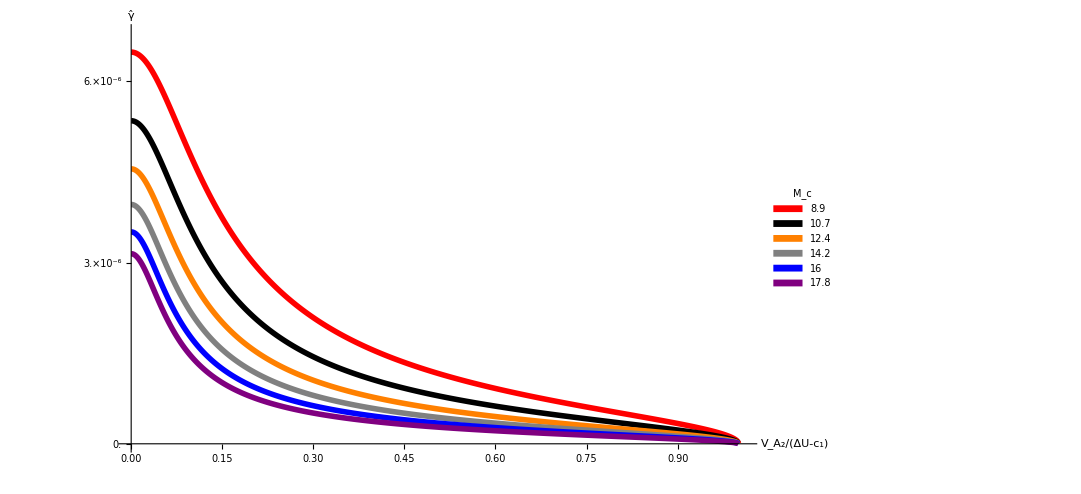

```mathematica
khplot2=ListPlot[{bdata500norm2,bdata600norm2,bdata700norm2,bdata800norm2,bdata900norm2,bdata1000norm2},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000005],{#,ScientificForm@#}&/@Range[0,0.00002,0.0000015]]},
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 2]]/(ΔU-Subscript[c, 1]),Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.10,0.2,0.3,0.4,0.5},{1.5*10^-6,3*10^-6,4.5*10^-6,6*10^-6}},
PlotRange->{{0.000001,1.01},{0,0.0000068}},
ImageSize->800,
MaxPlotPoints->1000]
```

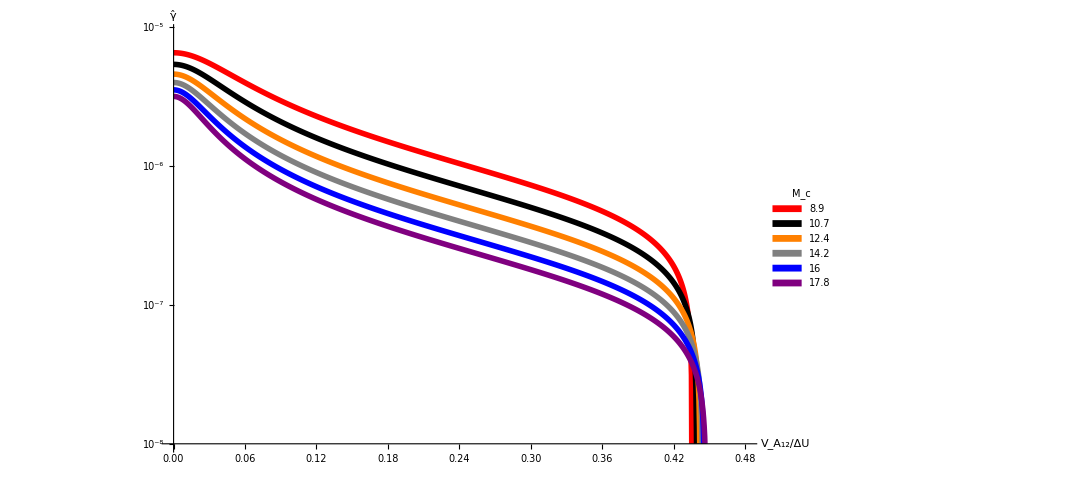

```mathematica
khplot35=ListLogPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.05,0.05},{0.05,0.05}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotRange->{{0.00005,.48},{10^-8,0.9*10^-5}},
ImageSize->800,
MaxPlotPoints->1000]
```

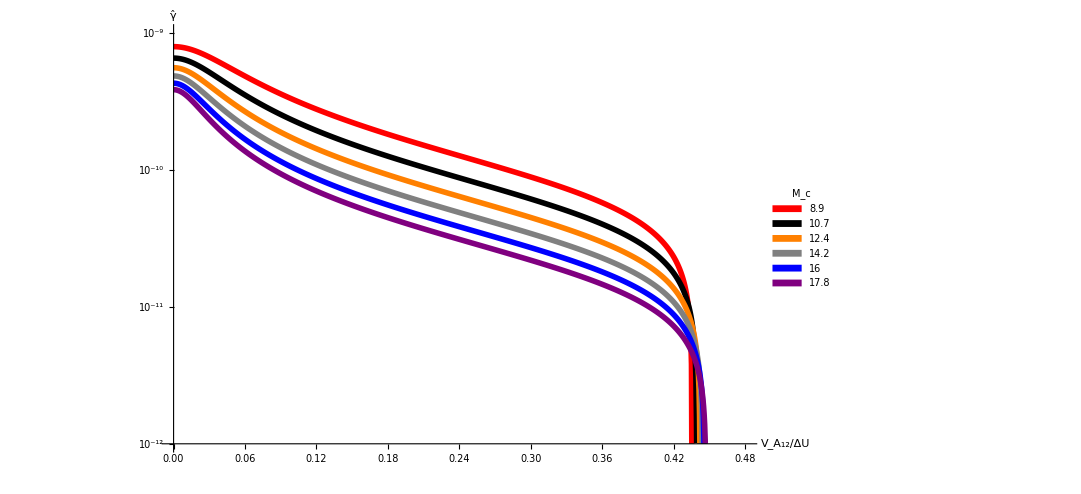

```mathematica
khplot35=ListLogPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.05,0.05},{0.05,0.05}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotRange->{{0.00005,.48},{10^-12,10^-9}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
khplot35=ListPlot[{bdata500norm2,bdata600norm2,bdata700norm2,bdata800norm2,bdata900norm2,bdata1000norm2},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.05,0.05},{0.05,0.05}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 2]]/(ΔU-Subscript[c, 1]),Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotRange->{{0.00005,1.01},{10^-12,10^-9}},
ImageSize->800,
MaxPlotPoints->1000]
```

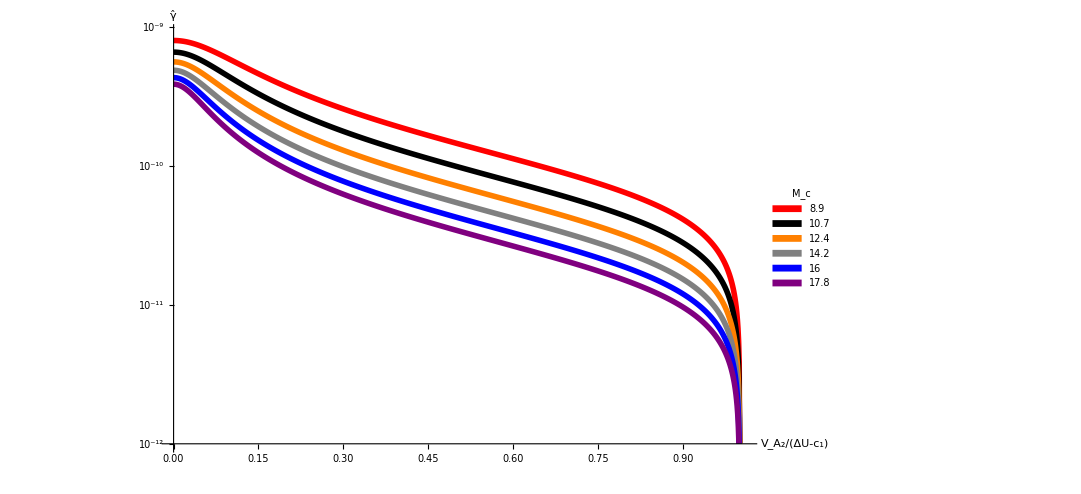

```mathematica
khplot35=ListLogPlot[{bdata500norm2,bdata600norm2,bdata700norm2,bdata800norm2,bdata900norm2,bdata1000norm2},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,28],Style[10.7,Bold,28],Style[12.4,Bold,28],Style[14.2,Bold,28],Style[16,Bold,28],Style[17.8,Bold,28]},LegendLabel->Style["M_c","Title",30,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.05,0.05},{0.05,0.05}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 2]]/(ΔU-Subscript[c, 1]),Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotRange->{{0.00005,1.01},{10^-12,9*10^-10}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["KH_multiplot_Va2.eps",khplot35,"EPS"]
```

KH_multiplot_Va2.eps

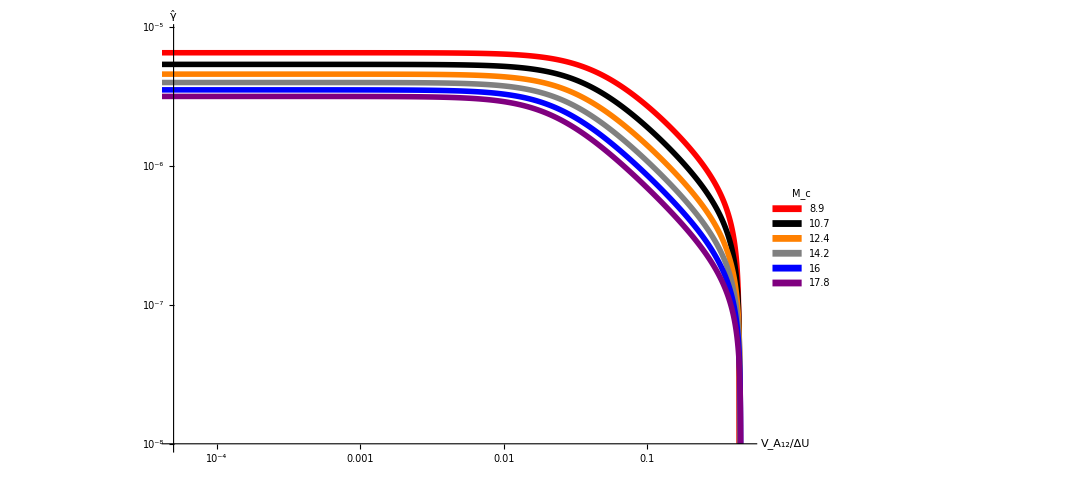

```mathematica
khplot3=ListLogLogPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.05,0.05},{0.05,0.05}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotRange->{{0.00005,0.48},{10^-8,0.9*10^-5}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["KH_multiplot_Mc_3.eps",khplot3,"EPS"]
```

```mathematica
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00002,0.0000025],{#,ScientificForm@#}&/@Range[0,0.00002,0.000005]]},
```

```mathematica
khbetaplot=ListLogPlot[{betadata500,betadata600,betadata700,betadata800,betadata900,betadata1000},

PlotStyle->{{Red,PointSize[0.005]},{Black,PointSize[0.005]},{Orange,PointSize[0.005]},{Gray,PointSize[0.005]},{Blue,PointSize[0.005]},{Purple,PointSize[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[5*10^6,Bold,30],Style[6*10^6,Bold,30],Style[7*10^6,Bold,30],Style[8*10^6,Bold,30],Style[9*10^6,Bold,30],Style[1*10^7,Bold,30]},LegendLabel->Style["Value of U_2-U_1","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[β,Large,Bold,Blue],Style[γ/Sqrt[gk],Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.025,0.05,0.075,0.10,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3},{10^-10,10^-9,10^-8,10^-7,10^-6}},
PlotRange->{{0.000001,0.32},{1*10^-11,2.5*10^-6}},
ImageSize->800]
```

```mathematica
Export["KH_multiplot_beta.eps",khbetaplot,"EPS"]
```

```mathematica
Length[bdata500]
```

```mathematica
bdata500[[1048]]
```

```mathematica
bdata500 =Drop[bdata500,-1];
```

```mathematica
bdata500norm = Drop[bdata500norm,-1];
```

```mathematica
bdata500norm[[-1]]
```

```mathematica
bdata600norm[[-2]]
```

```mathematica
bdata700norm[[-2]]
```

```mathematica
bdata800norm[[-1]]
```

```mathematica
bdata900norm[[-2]]
```

```mathematica
bdata500norm[[-1]]
```

```mathematica
Last[bdata1000norm]
```

### Now the RT plot

```mathematica
rtplot=ListPlot[{bdata500,bdata600,bdata700,bdata800,bdata900,bdata1000},
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.0001,0.000025],{#,ScientificForm@#}&/@Range[0,0.0001,0.000025]]},
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.025,0.05,0.075,0.10,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3},{1.25*10^-5,2.5*10^-5,3.75*10^-5,5*10^-5,6.25*10^-5,7.5*10^-5,8.75*10^-5,1*10^-4}},
PlotRange->{{0.000001,0.22},{0,0.000095}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["RT_multiplot_Mc.eps",rtplot,"EPS"]
```

```mathematica
rtplot2=ListPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.0001,0.0000025],{#,ScientificForm@#}&/@Range[0,0.0001,0.0000075]]},
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.05,0.10,0.15,0.2,0.25,0.3},{7.5*10^-6,1.5*10^-5,2.25*10^-5,3*10^-5}},
PlotRange->{{0.000001,0.305},{0,0.000031}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["RT_multiplot_Mc_2.eps",rtplot2,"EPS"]
```

```mathematica
rtplot3=ListLogPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Joined->True,
Ticks->Automatic,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.33,0.58},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.05,0.10,0.15,0.2,0.25,0.3},{1*10^-8,1*10^-7,1*10^-6,1*10^-5}},
PlotRange->{{0.000001,0.305},{0.000000001,0.0002}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["RT_multiplot_Mc_3.eps",rtplot3,"EPS"]
```

```mathematica
rtplot4=ListLogLogPlot[{bdata500norm,bdata600norm,bdata700norm,bdata800norm,bdata900norm,bdata1000norm},
Joined->True,
Ticks->Automatic,
PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Orange,Thickness[0.005]},{Gray,Thickness[0.005]},{Blue,Thickness[0.005]},{Purple,Thickness[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[8.9,Bold,30],Style[10.7,Bold,30],Style[12.4,Bold,30],Style[14.2,Bold,30],Style[16,Bold,30],Style[17.8,Bold,30]},LegendLabel->Style["M_c","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.05,0.10,0.15,0.2,0.25,0.3},{1*10^-8,1*10^-7,1*10^-6,1*10^-5}},
PlotRange->{{0.00005,0.305},{0.000000001,0.00012}},
ImageSize->800,
MaxPlotPoints->1000]
```

```mathematica
Export["RT_multiplot_Mc_4.eps",rtplot4,"EPS"]
```

```mathematica
rtbetaplot=ListLogPlot[{betadata500,betadata600,betadata700,betadata800,betadata900,betadata1000},

PlotStyle->{{Red,PointSize[0.005]},{Black,PointSize[0.005]},{Orange,PointSize[0.005]},{Gray,PointSize[0.005]},{Blue,PointSize[0.005]},{Purple,PointSize[0.005]}},
PlotLegends->Placed[SwatchLegend[{Style[5*10^6,Bold,30],Style[6*10^6,Bold,30],Style[7*10^6,Bold,30],Style[8*10^6,Bold,30],Style[9*10^6,Bold,30],Style[1*10^7,Bold,30]},LegendLabel->Style["Value of U_2-U_1","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[β,Large,Bold,Blue],Style[γ/Sqrt[gk],Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->{{0.025,0.05,0.075,0.10,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3},{10^-10,10^-9,10^-8,10^-7,10^-6,10^-5}},
PlotRange->{{0.000001,0.32},{1*10^-9,2.5*10^-5}},
ImageSize->800]
```

```mathematica
Export["RT_multiplot_beta.eps",rtbetaplot,"EPS"]
```

### Now we plot the comparison between the inc and comp cases

```mathematica
gammaincomp[ρ1_,ρ2_,U1_,U2_,kx_,g_,B_]:= -kx(ρ1/(ρ1+ρ2)U1+ρ2/(ρ1+ρ2)U2)*I+√(g *kx*(ρ1-ρ2)/(ρ1+ρ2)-kx^2 *(2*B^2)/(4*π*10^-7*(ρ1+ρ2))+kx^2*(ρ1*ρ2)/(ρ1+ρ2)^2(U1-U2)^2)
```

```mathematica
Solve[g *kx*(ρ1-ρ2)/(ρ1+ρ2)-kx^2 *(2*B^2)/(μ0*(ρ1+ρ2))+kx^2*(ρ1*ρ2)/(ρ1+ρ2)^2(U1-U2)^2==0,B]//Simplify
```

```mathematica
incdatag = Table[Re[gammaincomp[Last[plotdatakh500][[1]],Last[plotdatakh500][[2]],0,500000,1,10,B]],{B,0,0.15,0.0001}];
incVdata = Table[(B/√(4*π*10^-7*(Last[plotdatakh500][[1]]+Last[plotdatakh500][[2]])))/500000,{B,0,0.15,0.0001}];
normincdatag = Rescale[incdatag];
incdata = Thread[{incVdata,normincdatag}];
```

```mathematica
N[Re[gammaincomp[Last[plotdatakh500][[1]],Last[plotdatakh500][[2]],0,500000,1,10,0]]]
```

```mathematica
inc
```

```mathematica
incplot=Plot[Re[gammaincomp[Last[plotdatakh500][[1]],Last[plotdatakh500][[2]],0,500000,1,10,B]]/Re[gammaincomp[Last[plotdatakh500][[1]],Last[plotdatakh500][[2]],0,500000,1,10,0]],{B,0,0.15}]
```

```mathematica
plotb500comp = plotdatakh500[[;;,12]]/√(4*π*10^-7*(Last[plotdatakh500][[1]]+Last[plotdatakh500][[2]]))*(1/500000);
plotgamma500comp = Rescale[Abs[plotdatakh500[[;;,14]]]];
bdata500comp = Thread[{plotb500comp,plotgamma500comp}];
```

```mathematica
khcompplot = ListPlot[{bdata500comp, incdata},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Blue,Thickness[0.007]},{Orange,Thickness[0.007]}},
PlotLegends->Placed[SwatchLegend[{Style["Compressible",Bold,26],Style["Incompressible",Bold,26]},LegendLabel->Style["Instability","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.7,0.8},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ/Subscript[γ, max],Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->Automatic,
PlotRange->{Automatic,{0,1.1}},
ImageSize->800]
```

```mathematica
Export["KH_comp_compare_1.eps",khcompplot,"EPS"]
```

```mathematica
incdatatest = incdata;
```

```mathematica
Length[incdatatest]
```

```mathematica
incdatatest[[997]]
```

```mathematica
incdatatest = Drop[incdatatest,-1];
```

```mathematica
khcompplot2 = ListPlot[{bdata500comp, incdatatest,listdatacomp,listdatainc},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Blue,Thickness[0.007]},{Orange,Thickness[0.015]},{RGBColor["#0C7BDC"],Thickness[0.007]},{Black,Thickness[0.004],Dashed}},
PlotLegends->Placed[SwatchLegend[{Style["Comp. High Shear",Bold,26],Style["Incomp. High Shear",Bold,26],Style["Comp. Low Shear",Bold,26],Style["Incomp. Low Shear",Bold,26]},
LegendLabel->Style["Instability","Title",32,Bold,Black],
LegendMarkerSize->20,
LegendMarkers->"Bubble",
LegendFunction->"Panel"],{{0.75,0.95},{0.5,1}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ/Subscript[γ, max],Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->Automatic,
PlotRange->{{0,0.45},{0,1.1}},
ImageSize->800]
```

```mathematica
Export["KH_comp_compare_2.eps",khcompplot2,"EPS"]
```

## With and without RT

### A=0.9

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
drange=Range[107178,1500492,1340];
```

```mathematica
a =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange}];
```

```mathematica
(*khroot = Flatten[Append[a[[1;;1516,1]],a[[1517;;All,3]]]];*)
khroot = Flatten[Append[a[[1;;34,1]],a[[35;;All,3]]]];
dvals = Table[d/(c1+c2),{d,drange}];
khrootdata = khroot[[All,2]]/(c1*kx);
data = Thread[{dvals,Abs[Re[khrootdata]]}];
```

### Plot KH

```mathematica
ListLogPlot[data]
```

#### Now we look at the case without RT

```mathematica
c2=20000;
c1=87178;
```

```mathematica
b =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange}];
```

```mathematica
khrootnort = Flatten[Append[b[[1;;497,1]],b[[503;;All,1]]]];
dvalsnort=Flatten[Append[dvals[[1;;497]],dvals[[503;;All]]]];
```

```mathematica
khrootnort = Flatten[Append[b[[1;;497,1]],b[[503;;All,1]]]];
(*khrootnort = Flatten[b[[;;,;;,1]]];*)
khrootdatanort = khrootnort[[All,2]]/(c1*kx);
dvalsnort=Flatten[Append[dvals[[1;;497]],dvals[[503;;All]]]];
datanort = Thread[{dvalsnort,Abs[Re[khrootdatanort]]}];
```

```mathematica
ListLogPlot[datanort]
```

```mathematica
p1 =ListLogPlot[{data},
Joined->True,
ImageSize->800,
PlotStyle->{Directive[Blue,Thickness[0.008]]},
PlotRange->{{2,14},{9*10^-12,6*10^-9}},
PlotLegends->SwatchLegend[{Style["A = 0.9",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"],
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}]
```

```mathematica
p2 = ListLogPlot[datanort,
Joined->True,
ImageSize->800,
PlotStyle->{Directive[Orange,Thickness[0.008]]},
PlotRange->{{2,14},{9*10^-12,6*10^-9}},
PlotLegends->SwatchLegend[{Style["A = -0.9",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"],
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}]
```

```mathematica
Show[{p2,p1}]
```

### With RT and A=0.1

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=22110.8;
```

```mathematica
N[590000/(c1+c2)]
```

```mathematica
N[274/2]
```

```mathematica
drange2 =Range[42000.,590000.,137];
```

```mathematica
c =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange2}];
```

```mathematica
(*TableForm[a]*)
```

```mathematica
khroot2 = Flatten[Append[c[[1;;33,1]],c[[34;;All,3]]]];
dvals2 = Table[d/(c1+c2),{d,drange2}];
khrootdata2 = khroot2[[All,2]]/(c1*kx);
data2 = Thread[{dvals2,Abs[Re[khrootdata2]]}];
```

```mathematica
p3 =ListLogPlot[{data2},
Joined->True,
ImageSize->800,
PlotStyle->{Directive[Red,Thickness[0.008]]},
PlotRange->{{2,14},{9*10^-12,6*10^-9}},
PlotMarkers->{Automatic, Small},
PlotLegends->SwatchLegend[{Style["A = 0.1",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"],
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}]
```

#### Without RT and A=0.1

```mathematica
c2=20000;
c1=22110.8;
d =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange2}];
```

```mathematica
N[c1/c2]
```

```mathematica
N[c2/c1]
```

```mathematica
khrootnort2 = Flatten[d[[;;,1]]];
khrootdatanort2 = khrootnort2[[All,2]]/(c1*kx);
data2nort = Thread[{dvals2,Abs[Re[khrootdatanort2]]}];
```

```mathematica
p4 =ListLogPlot[{data2nort},
Joined->True,
ImageSize->800,
PlotStyle->{Directive[Black,Thickness[0.008]]},
PlotRange->{{2,14},{9*10^-12,5*10^-9}},
PlotMarkers->{Automatic, Small},
PlotLegends->SwatchLegend[{Style["A = -0.1",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"],
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}
]
```

```mathematica
withandwithoutrtplot=Show[p1,p2,p3,p4]
```

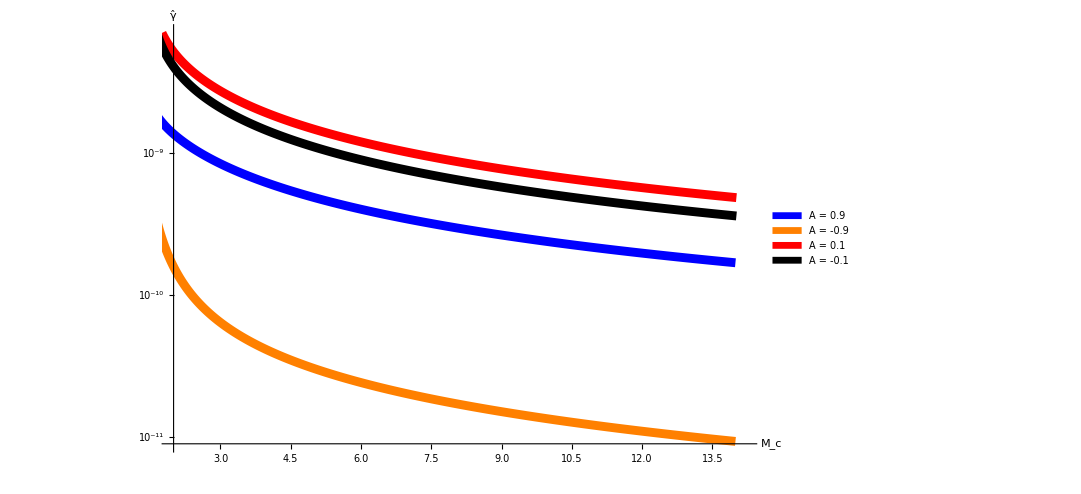

```mathematica
withwithout2 = ListLogPlot[{data,datanort,data2,data2nort},
Joined->True,
ImageSize->800,
PlotStyle->{Directive[Blue,Thickness[0.008]],Directive[Orange,Thickness[0.008]],Directive[Red,Thickness[0.008]],Directive[Black,Thickness[0.008]]},
PlotRange->{{2,14.2},{9*10^-12,7*10^-9}},
PlotLegends->{SwatchLegend[{Style["A = 0.9",Bold,20],Style["A = -0.9",Bold,20],Style["A = 0.1",Bold,20],Style["A = -0.1",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"]},
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}
]
```

```mathematica
Export["wwrtplot_3.eps",withandwithoutrtplot,"EPS"]
```

```mathematica
Export["wwrtplot_3.eps",withwithout2,"EPS"]
```

wwrtplot_3.eps

## Re Im plot of RT root

### Calculate Numerical roots for A = 0.9

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
d2range =Range[107178,1500492,1340];
```

```mathematica
N[1340/(c1+c2)]
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

```mathematica
(*TableForm[a2]*)
```

```mathematica
rtroot2=  Flatten[Append[a2[[1;;34,3]],a2[[35;;All,1]]]];
rtrootdata2 = rtroot2[[All,2]]/Sqrt[g*kx];
```

```mathematica
plotdata=Abs[Re[rtrootdata2]]+Im[rtrootdata2]*I;
plotdata2= -Abs[Re[rtrootdata2]]+Im[rtrootdata2]*I;
```

```mathematica
reimplot=ComplexListPlot[{plotdata,plotdata2},
PlotRange->Automatic,
AspectRatio->Full,
Joined->False,
PlotStyle->{{Blue,PointSize[0.008]},{ Orange,PointSize[0.008]}},
AxesStyle->{{Thick,Black},{Thick,Black}},
AxesLabel->{Style[" Re(γ̂)",Large,Bold,Blue],Style["Im(γ̂)",Large,Bold,Blue]},
TicksStyle->{{Directive[Black,Thick,22,Bold]},{Directive[Black,Thick,22,Bold]}},
Ticks->{Join[{#,"",{0.006,0.}}&/@Range[-0.00006,0.00006,0.000005],{#,ScientificForm@#}&/@Range[-0.00006,0.00006,0.00002]],Automatic},
ImageSize->1000,
Epilog->{{Arrow[{{0.00002,-25000},{0.00004,-50000}}],Text[Style["M_c",Bold,22],{0.00004,-50000},{1,1}],Arrow[{{-0.00002,-25000},{-0.00004,-50000}}],Text[Style["M_c",Bold,22],{-0.00004,-50000},{-1,1}]}}
]
```

```mathematica
reimplot=ComplexListPlot[{plotdata,plotdata2},
PlotRange->Automatic,
AspectRatio->Full,
Joined->True,
PlotStyle->{{Blue,Thickness[0.004]},{ Orange,Thickness[0.004]}},
AxesStyle->{{Thick,Black},{Thick,Black}},
AxesLabel->{Style[" Re(γ̂)",Large,Bold,Blue],Style["Im(γ̂)",Large,Bold,Blue]},
TicksStyle->{{Directive[Black,Thick,22,Bold]},{Directive[Black,Thick,22,Bold]}},
Ticks->{Join[{#,"",{0.006,0.}}&/@Range[-0.00006,0.00006,0.000005],{#,ScientificForm@#}&/@Range[-0.00006,0.00006,0.00002]],Automatic},
ImageSize->1000,
Epilog->{{Arrow[BezierCurve[{{0.00002,-20000},{0.00004,-20000},{0.000055,-30000},{0.000056,-70000}}]],Text[Style["Increasing M_c",Bold,22],{0.000056,-70000},{1,1}],Arrow[BezierCurve[{{-0.00002,-20000},{-0.00004,-20000},{-0.000055,-30000},{-0.000056,-70000}}]],Text[Style["Increasing M_c",Bold,22],{-0.000056,-70000},{-1,1}]}}
]
```

```mathematica
Export["ReImplot_4.eps",reimplot,"EPS"]
```

```mathematica
ListPlot[{data7,data8},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00006,0.000005],{#,ScientificForm@#}&/@Range[0,0.00006,0.00001]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotLegends->{Style[Numerical,Bold],Style[Analytic,Bold]},
PlotStyle->{Blue, Orange},AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ/√(gk),Large,Bold,Blue]},
ImageSize->800]
```

```mathematica
Plot[Sin[x],{x,0,2 Pi},Epilog->{Arrow[{{3 Pi/2,1/2},{Pi,0}}],Text["Zero",{3 Pi/2,1/2},{-1,-1}]}]
```

## Compressible KH w/ and w/o g

### A = 0.9

```mathematica
kx=1;
ky=0;
g=10;
g0 = 0;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
N[Solve[200==ρ1*20000^2]]
```

```mathematica
N[Solve[200==ρ2*87178^2]]
```

```mathematica
d2range =Range[0,240000,1000];
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

```mathematica
khroot2 = Flatten[Append[a2[[1;;152,1]],a2[[153;;All,3]]]];
rtroot2=  Flatten[Append[a2[[109;;152,3]],a2[[153;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,d2range}];
khrootdata2=khroot2[[All,2]];
rtrootdata2 = rtroot2[[All,2]];
normkhdata = Rescale[Abs[Re[khrootdata2]]];
normrtdata = Rescale[Abs[Re[rtrootdata2]]];
data5=Thread[{dvals2,normkhdata}];
data7 = Thread[{dvals2[[109;;All]],normrtdata}];
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+√(1+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1)))+2 p0 (ⅈ k U1+γ)^2 (1+√(1+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/(g^2 ρ2)))-g^2 (-1+√(1+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (1+√(1+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/(g^2 ρ2))) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+√(1/g^2(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1)))+2 p0 (ⅈ k U1+γ)^2 (1+√(1/g^2(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)))-g^2 (-1+√(1/g^2(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1)))) (1+√(1/g^2(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+1/g √(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (1+1/g √(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))-g^2 (-1+1/g √(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (1+1/g √(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2) ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-g+√(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (g+√(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))- g(-g+√(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (g+√(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)) (ρ1-ρ2)) ρ2
```

Set g=0

```mathematica
1/(4 p0^2) ρ1 (-2 p0 (k U2-ⅈ γ)^2 (√((4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (√((4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))) ρ2
```

```mathematica
(-(k U2-ⅈ γ)^2 (√(4  c1^2((ⅈ k U1+γ)^2+k^2 c1^2)))+(ⅈ k U1+γ)^2 (√(4 c2^2((ⅈ k U2+γ)^2+k^2 c2^2))))
```

```mathematica
-(k U2-ⅈ γ)^2 (2 c1 √((ⅈ k U1+γ)^2+k^2 c1^2))+(ⅈ k U1+γ)^2 (2 c2 √((ⅈ k U2+γ)^2+k^2 c2^2)) 
-c1(k U2-ⅈ γ)^2  √((ⅈ k U1+γ)^2+k^2 c1^2)+c2(ⅈ k U1+γ)^2  √((ⅈ k U2+γ)^2+k^2 c2^2)
 c1^2(ⅈ k U2+ γ)^4  ((ⅈ k U1+γ)^2+k^2 c1^2)-c2^2(ⅈ k U1+γ)^4  ((ⅈ k U2+γ)^2+k^2 c2^2)
```

```mathematica
testdata = Thread[{dvals2,Abs[Re[test]]}];
```

```mathematica
N[kx*(c1+c2)/(c1^2+c2^2) c1 c2*√(-1-(d/(c1+c2))^2+√(1+4(d/(c1+c2))^2))]
```

```mathematica
Solve[k* c11 c22*√(-1-Mc^2+√(1+4Mc^2))==0,Mc]
```

```mathematica
Manipulate[{NSolve[-(kx (d+U1)-ⅈ γ)^2 (√(4  c1^2((ⅈ kx U1+γ)^2+kx^2 c1^2)))+(ⅈ kx U1+γ)^2 (√(4 c2^2((ⅈ kx (d+U1)+γ)^2+kx^2 c2^2)))==0],d},{d,0,140522.3461650872}]
```

```mathematica
dt=140522.3461650885103145;
FindRoot[-(SetPrecision[kx,64]*(SetPrecision[dt,64]+SetPrecision[U1,64])-ⅈ γ)^2 (√(SetPrecision[4,64]  SetPrecision[c1,64]^2((ⅈ SetPrecision[kx,64] SetPrecision[U1,64]+γ)^2+SetPrecision[kx,64]^2 SetPrecision[c1,64]^2)))+(ⅈ SetPrecision[kx,64] SetPrecision[U1,64]+γ)^2 (√(SetPrecision[4,64] SetPrecision[c2,64]^2((ⅈ SetPrecision[kx,64] (SetPrecision[dt,64]+SetPrecision[U1,64])+γ)^2+SetPrecision[kx,64]^2 SetPrecision[c2,64]^2)))==0,{γ,0.01-53306*I},PrecisionGoal->8,AccuracyGoal->8,WorkingPrecision->60,MaxIterations->10000]
```

```mathematica
140522.3461650872
```

```mathematica
140522.3461650875
```

```mathematica
140522.346
```

```mathematica
140522.34616000002
```

```mathematica
140522.346165
```

```mathematica
140522.346165084
```

```mathematica
140522.34616508702
```

```mathematica
140522.34616508716
```

```mathematica
d22range = Range[0,140000,1000];
d23range = Range[140000,140500,100];
d24range = Range[140500,140522,1];
d25range = Range[140522,140522.34,0.01];
d26range = Range[140522.34,140522.345,0.001];
d2nogrange = Flatten[Append[Append[Append[Append[d22range,d23range],d24range],d25range],d26range]];
```

```mathematica
a22nog = ParallelTable[NSolve[-(kx (d+U1)-ⅈ γ)^2 (√(4  c1^2((ⅈ kx U1+γ)^2+kx^2 c1^2)))+(ⅈ kx U1+γ)^2 (√(4 c2^2((ⅈ kx (d+U1)+γ)^2+kx^2 c2^2)))==0],{d,d2nogrange}];
```

```mathematica
dvalextra={140522.3461650885/(c1+c2),140522.3461650885102/(c1+c2),140522.3461650885103145/(c1+c2)};
khextra = {0.00043508984982895904772041967411094799097687570695158815941555217935336217655`60.-53306.14613807765356389615328291548165144863713365812041521263133824012089910551387`60. ⅈ,0.00004717691446651267431065305082518887571963579042339905027736169851710004517`60.-53306.14613807765834480765014339037926108684405918647884201768890475141840908414182`60. ⅈ,9.93541618824217721137522472564194144480473444881694062021126299178152099`60.*^-6-53306.1461380776583991794064808303133749849407162204834760927499072434312836234617`60. ⅈ};
dvals22 = Table[d/(c1+c2),{d,d2nogrange}];
dvals222 = Flatten[Append[dvals22,dvalextra]];
khrootdata22=Flatten[Append[a22nog[[All,2,1,2]],khextra]];
normkhnogdata = Rescale[Abs[Re[khrootdata22]]];
dvals222[[1]] = 0;
normkhnogdata[[1]] = 5*10^-10
data55=Thread[{dvals222,normkhnogdata}];
```

1/2000000000

```mathematica
dvals222[[1]] = 2
```

```mathematica
data55[[3]]
```

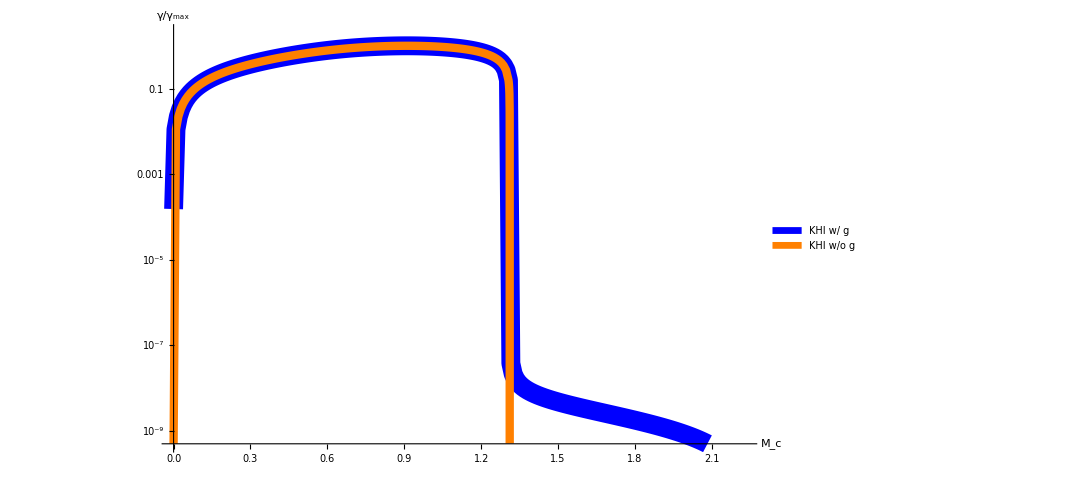

```mathematica
combinedplot1=ListLogPlot[{data5,data55},
Joined->True,
PlotLegends->SwatchLegend[{Style["KHI w/ g",Bold,30],Style["KHI w/o g",Bold, 30],Style["KHI No g",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Directive[Thickness[0.017],Blue], Directive[Thickness[0.0075],Orange],Directive[Thickness[0.005],Red]},
AxesStyle->Directive[24,Bold,Thick],
PlotRange->{Automatic,{5*10^-10,2}},
AxesLabel->{Style["M_c",Large,Bold,Blue],Style[γ/Subscript[γ, max],Large,Bold,Blue]},
GridLinesStyle->Directive[Black, Thick,Bold],
Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,-11,4}]},
ImageSize->800]
```

```mathematica
Export["combined_plot1_2.eps",combinedplot1,"EPS"]
```

```mathematica
ListLogPlot[{data5,testdata,data55},
PlotMarkers->{{●,20},{Automatic,10},{•,7}},
PlotLegends->SwatchLegend[{Style["KHRTI",Bold,30],Style["RTI-Like",Bold, 30],Style["KHI No g",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Blue, Orange,Red},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
GridLines->{{1.312},{}},
GridLinesStyle->Directive[Black, Thick,Bold],
Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,-5,4}]},
ImageSize->800]
```

## Testing

A=0

```mathematica
kx=1;
ky=0;
k=1;
g=10;
U1 = 15000;
c1=20000;
c2=20000;
```

```mathematica
N[Solve[Mc/40000==2√2]]
```

```mathematica
Manipulate[{NSolve[-(kx (d+U1)-ⅈ γ)^2 (√(4  c1^2((ⅈ kx U1+γ)^2+kx^2 c1^2)))+(ⅈ kx U1+γ)^2 (√(4 c2^2((ⅈ kx (d+U1)+γ)^2+kx^2 c2^2)))==0],d/40000},{d,0,113138}]
```

```mathematica
Manipulate[{NSolve[(c1^2 k^2+(n+I*k*U1)^2)(n+I*k*U2)^4-(c1^2 k^2+(n+I*k*U2)^2)(n+I*k*U1)^4==0,n],(U2-U1)/40000},{U2,0,133138}]
```

```mathematica
d2range =Range[0,113137.08498984762,1000];
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

A=0.1

```mathematica
ReplaceAll[(ρ2-ρ1)/(ρ1+ρ2),{ρ1->1/c11^2,ρ2->1/c22^2}]//Simplify
```

```mathematica
Solve[(-c22^2+c1^2)/(c22^2+c1^2)==0.1]
```

```mathematica
Manipulate[{NSolve[c1^2(c1^2 k^2+(n+I*k*U1)^2)(n+I*k*U2)^4-c2^2(c2^2 k^2+(n+I*k*U2)^2)(n+I*k*U1)^4==0,n],(U2-U1)/(c1+c2),(c1^2-c2^2)/(c2^2+c1^2)},{U2,0,133138},{c2,20000,0}]
```

## Testing h +-

```mathematica
ReplaceAll[(L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)) u[z]+L (γ̄)^2 (c^2 (γ̄)^6+c^4 (γ̄)^4 Subscript[k, x]^2+2 c^2 V^2 (γ̄)^4 Subscript[k, x]^2+c^4 K^2 V^4 Subscript[k, x]^4+2 c^4 V^2 (γ̄)^2 Subscript[k, x]^4+c^2 V^4 (γ̄)^2 Subscript[k, x]^4+c^4 (γ̄)^4 Subscript[k, y]^2+3 c^2 V^2 (γ̄)^4 Subscript[k, y]^2+2 V^4 (γ̄)^4 Subscript[k, y]^2+2 c^4 V^2 (γ̄)^2 Subscript[k, x]^2 Subscript[k, y]^2+3 c^2 V^4 (γ̄)^2 Subscript[k, x]^2 Subscript[k, y]^2) u'[z]-L^2 ((γ̄)^2+V^2 Subscript[k, x]^2) (c^2 (γ̄)^2+V^2 (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (c^2 K^2 (γ̄)^2+K^2 V^2 (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) u''[z],V->0]
```

(L^2 (γ̄)^10+L^2 (γ̄)^8 (2 c^2 k_x^2+2 c^2 k_y^2)+K^2 L^2 (γ̄)^6 (c^4 k_x^2+c^4 k_y^2)) u[z]+L (γ̄)^2 (c^2 (γ̄)^6+c^4 (γ̄)^4 k_x^2+c^4 (γ̄)^4 k_y^2) u'[z]-c^2 L^2 (γ̄)^4 (c^2 K^2 (γ̄)^2+(γ̄)^4) u''[z]

```mathematica
Simplify[(L^2 (γ̄)^10+L^2 (γ̄)^8 (2 c^2 Subscript[k, x]^2+2 c^2 Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 (c^4 Subscript[k, x]^2+c^4 Subscript[k, y]^2)) u[z]+L (γ̄)^2 (c^2 (γ̄)^6+c^4 (γ̄)^4 Subscript[k, x]^2+c^4 (γ̄)^4 Subscript[k, y]^2) u'[z]-c^2 L^2 (γ̄)^4 (c^2 K^2 (γ̄)^2+(γ̄)^4) u''[z]]//Simplify
```

L (γ̄)^6 (L (γ̄)^4 u[z]+c^2 (γ̄)^2 (2 L k_x^2 u[z]+2 L k_y^2 u[z]+u'[z]-L u''[z])+c^4 (k_x^2 (K^2 L u[z]+u'[z])+k_y^2 (K^2 L u[z]+u'[z])-K^2 L u''[z]))

```mathematica
Simplify[(L^2 (γ̄)^10+L^2 (γ̄)^8 (2 c^2 Subscript[k, x]^2+2 c^2 Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 (c^4 Subscript[k, x]^2+c^4 Subscript[k, y]^2)) ]
```

L^2 (γ̄)^6 ((γ̄)^4+c^4 K^2 (k_x^2+k_y^2)+2 c^2 (γ̄)^2 (k_x^2+k_y^2))

```mathematica
Simplify[L (γ̄)^2 (c^2 (γ̄)^6+c^4 (γ̄)^4 Subscript[k, x]^2+c^4 (γ̄)^4 Subscript[k, y]^2)]
```

c^2 L (γ̄)^6 ((γ̄)^2+c^2 (k_x^2+k_y^2))

```mathematica
Simplify[c^2 L^2 (γ̄)^4 (c^2 K^2 (γ̄)^2+(γ̄)^4) ]
```

c^2 L^2 (γ̄)^6 (c^2 K^2+(γ̄)^2)

```mathematica
Simplify[- L ((γ̄)^4+c^4 K^4 +2 c^2 (γ̄)^2 K^2)u[z]-c^2  ((γ̄)^2+c^2 K^2)u'[z]+c^2 L  (c^2 K^2+(γ̄)^2)u''[z]==0]
```

(c^2 K^2+(γ̄)^2) (L (c^2 K^2+(γ̄)^2) u[z]+c^2 (u'[z]-L u''[z]))==0

```mathematica
DSolve[L (c^2 K^2+(γ̄)^2) u[z]+c^2 (u'[z]-L u''[z])==0,u[z],z]//Simplify
```

{{u[z]→ⅇ^(1/2 z (1/L-√(4 K^2+1/L^2+(4 (γ̄)^2)/c^2))) C[1]+ⅇ^(1/2 z (1/L+√(4 K^2+1/L^2+(4 (γ̄)^2)/c^2))) C[2]}}

```mathematica
ReplaceAll[1/L-√(4 K^2+1/L^2+(4 (γ̄)^2)/c^2),L->c^2/g]//Simplify
```

g/c^2-√(g^2/c^4+4 K^2+(4 (γ̄)^2)/c^2)

```mathematica
Together[g^2/c^4+4 K^2+(4 (γ̄)^2)/c^2]
```

(g^2+4 c^4 K^2+4 c^2 (γ̄)^2)/c^4

```mathematica
(g-√(g^2+4 c1^4 K^2+4 c1^2 (γ+I*kx*U1)^2))
(g+√(g^2+4 c2^4 K^2+4 c2^2 (γ+I*kx*U2)^2))
```

```mathematica
ScientificForm[{100000.}]
```

{1.×10^5}

```mathematica
ScientificForm[{123450000.0,0.000012345,123.45},3]
```

{1.23×10^8,1.23×10^-5,1.23×10^2}

```mathematica
list=ScientificForm[Table[1.*10^-(i*10),{i,0,20,5}],3]
```

{1.,1.×10^-50,1.×10^-100,1.×10^-150,1.×10^-200}

### A = 0

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c=20000;
hplus[g_,c2_,kx_,U2_,γ_]:=g/(2 c^2)+1/2 √(4 kx^2+(g^2+4 c^2 (γ+I*kx*U2)^2)/c^4);
hminus[g_,c1_,kx_,U1_,γ_]:=g/(2 c^2)-1/2 √(4 kx^2+(g^2+4 c^2 (γ+I*kx*U1)^2)/c^4);
hplusog[c2_,kx_,U2_,γ_]:=√(kx^2+ (γ+I*kx*U2)^2/c^2)
hminusnog[c1_,kx_,U1_,γ_]:=-√(kx^2+ (γ+I*kx*U1)^2/c^2)
gammanog[c_,kx_,U1_,U2_]:=1/-2*I*kx*(U1+U2)-I*kx*c*√((U1-U2)^2/(4 c^2)+1-√(1+(U1-U2)^2/c^2));
gamma[g_,c_,kx_,U1_,U2_]:=  ⅈ  c kx (-(U1+U2)/(2 c)+ √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1-(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/c)^2)));
```

```mathematica
gamma2[g_,c_,kx_,U1_,U2_]:=  ⅈ  c kx (-(U1+U2)/(2 c)+ √((ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1+(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/(2c))^2)));
```

```mathematica
ClearAll[c,kx,g]
```

```mathematica
Solve[(U2-U1)/(2c)==√2,U2]
```

{{U2→5000 (3+8 √2)}}

```mathematica
N[%]
```

{{U2→71568.5}}

```mathematica
N[gammanog[c,kx,U1,71000]]
```

2299.02-43000. ⅈ

```mathematica
N[gamma[g,c,kx,U1,71000]]
```

2299.02-43000. ⅈ

```mathematica
Manipulate[Re[N[hminus[g*1000,c,kx,U1,gamma[g*1000,c,kx,U1,U2]]]],{U2,10000,80000}]
```

```mathematica
Manipulate[Re[N[hminusnog[c,kx,U1,gammanog[c,kx,U1,U2]]]],{U2,10000,80000}]
```

ⅇ^(-0.269064 z)

```mathematica
Manipulate[Exp[z*Re[N[hminusnog[c,kx,U1,gammanog[c,kx,U1,70000]]]]]-Exp[z*Re[N[hminus[g*100,c,kx,U1,gamma2[g*100,c,kx,U1,70000]]]]],{z,0,10}]
```

```mathematica
LogLogPlot[{N[Exp[z*Re[N[hminusnog[c,kx,U1,gammanog[c,kx,U1,70000]]]]]-Exp[z*Re[N[hminus[g*10000,c,kx,U1,gamma2[g,c,kx,U1,70000]]]]]]},{z,0.1,10},PlotRange->Full,Ticks->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
Re[N[hminusnog[c,kx,75000,gamma[g,c,kx,U1,43284]]]]
```

-0.532123

```mathematica
Re[N[hminus[g,c,kx,U1,gamma2[g,c,kx,U1,400000]]]]
```

-0.0317781

```mathematica
Manipulate[LogLogPlot[Exp[z*Re[N[hminus[g,c,kx,U1,gamma2[g,c,kx,U1,U2]]]]],{z,0.1,10},PlotRange->Full,Ticks->Automatic,ImageSize->Large],{U2,400000,40000}]
```

```mathematica
Re[N[hminus[g,c,kx,U1,gamma2[g,c,kx,U1,43284.27]]]]
```

-7.44484×10^8

```mathematica
N[Exp[1/2*-7.444838874072348*^8],10]
```

General::munfl: Exp[-3.72242×10^8] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Manipulate[LogLogPlot[Re[1/Exp[1/2 z*hplus[g,c,kx,U1,gamma2[g,c,kx,U1,U2]]]],{z,0.1,10},PlotRange->Full],{U2,75000,750000}]
```

```mathematica
Manipulate[N[Exp[1/2 z*hminus[g,c,kx,U1,gamma2[g,c,kx,U1,U2]]],128],{U2,75000,150000},{z,0.1,10}]
```

```mathematica
Manipulate[N[Exp[1/2 z*hplus[g,c,kx,U2,gamma2[g,c,kx,U1,U2]]],128],{U2,75000,150000},{z,0,-10}]
```

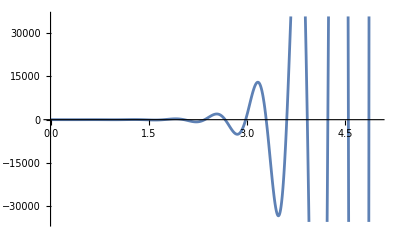

```mathematica
Plot[Re[Exp[x(3+10I)]],{x,0,5}]
```

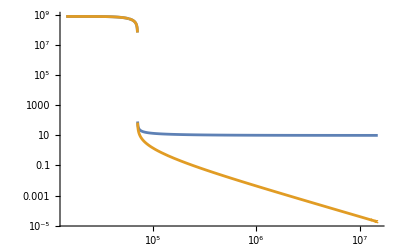

```mathematica
LogLogPlot[{Re[hplus[g,c,kx,U2,gamma[g,c,kx,U1,U2]]],-Re[hminus[g,c,kx,U1,gamma[g,c,kx,U1,U2]]]},{U2,0,15000000},PlotRange->Automatic]
```

### A = 0.1

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=22110.8;
hplus[g_,c2_,kx_,U2_,γ_]:=(g+√(g^2+4 c2^4 kx^2+4 c2^2 (γ+I*kx*U2)^2));
hminus[g_,c1_,kx_,U1_,γ_]:=(g-√(g^2+4 c1^4 kx^2+4 c1^2 (γ+I*kx*U1)^2));
```

```mathematica
drange =Range[42000.,590000.,548];
a =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange}];
```

```mathematica
khroot = Flatten[Append[a[[1;;33,1]],a[[34;;All,3]]]];
rtroot=  Flatten[Append[a[[2;;33,3]],a[[34;;All,1]]]];
dvals = Table[d/(c1+c2),{d,drange}];
khrootdata = khroot[[All,2]]/Sqrt[g*kx];
rtrootdata = rtroot[[All,2]]/Sqrt[g*kx];
khapprox = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,drange}];
rtapprox = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,drange}];
data = Thread[{dvals,Abs[Re[khrootdata]]}];
data2 = Thread[{dvals,khapprox}];
data3 = Thread[{dvals[[2;;All]],Abs[Re[rtrootdata]]}];
data4 = Thread[{dvals,rtapprox}];
```

```mathematica
Length[drange]
```

1001

```mathematica
khroot[[1001,2]]
```

-9.71045×10^-6-35015.1 ⅈ

```mathematica
rtroot[[1,2]]
```

-3.41255×10^-6-35207.6 ⅈ

```mathematica
√(10^2+4 *20000^4 +4* 20000^2 (3.4125546740035015*^-6-35207.64269498561 ⅈ+I*15000)^2)
```

0.954647-1.15577×10^8 ⅈ

```mathematica
1/(2*c1)√(1/2(√(35207.64269498561^4+4*(3.4125546740035015*^-6*-35207.64269498561)^2)-35207.64269498561^2))
```

0.

```mathematica
g^2/(4*c1^2)+1+(3.4125546740035015*^-6)^2
```

1.

```mathematica
hpluskhlist = ParallelTable[N[hplus[g,c2,kx,drange[[i]]+U1,Abs[Re[khroot[[i,2]]]]+I*Im[khroot[[i,2]]]]],{i,Length[khroot]}];
hminuskhlist = ParallelTable[N[hminus[g,c1,kx,U1,Abs[Re[khroot[[i,2]]]]+I*Im[khroot[[i,2]]]]],{i,Length[khroot]}];
hplusrtlist = ParallelTable[N[hplus[g,c2,kx,drange[[i]]+U1,Abs[Re[rtroot[[i,2]]]]+I*Im[rtroot[[i,2]]]]],{i,Length[rtroot]}];
hminusrtlist = ParallelTable[N[hminus[g,c1,kx,U1,Abs[Re[rtroot[[i,2]]]]+I*Im[rtroot[[i,2]]]]],{i,Length[rtroot]}];
```

```mathematica
Re[hpluslist]
```

{7.49486×10^8,7.40511×10^8,7.31246×10^8,7.2168×10^8,7.11798×10^8,7.01588×10^8,6.91034×10^8,6.8012×10^8,6.68827×10^8,6.57135×10^8,6.45023×10^8,6.32465×10^8,6.19434×10^8,6.05899×10^8,5.91824×10^8,5.77171×10^8,5.61892×10^8,5.45935×10^8,5.29239×10^8,5.1173×10^8,4.93321×10^8,4.73907×10^8,4.53358×10^8,4.31513×10^8,4.08161×10^8,3.83027×10^8,3.55734×10^8,3.25737×10^8,2.92206×10^8,2.53741×10^8,2.07619×10^8,1.46788×10^8,402.121,52.4771,39.4209,33.6272,30.1796,27.8329,26.1055,24.7668,23.6907,22.8017,22.0516,21.4079,20.8477,20.3546,19.9163,19.5234,19.1686,18.8463,18.5517,18.2812,18.0316,17.8004,17.5856,17.3852,17.1977,17.0218,16.8564,16.7005,16.5532,16.4137,16.2814,16.1557,16.0361,15.922,15.8132,15.7091,15.6095,15.5141,15.4225,15.3346,15.2501,15.1687,15.0903,15.0147,14.9418,14.8714,14.8033,14.7375,14.6738,14.6121,14.5522,14.4942,14.438,14.3833,14.3302,14.2786,14.2284,14.1796,14.1321,14.0858,14.0407,13.9968,13.9539,13.9121,13.8713,13.8315,13.7926,13.7546,13.7175,13.6812,13.6457,13.6109,13.5769,13.5437,13.5111,13.4792,13.448,13.4173,13.3873,13.3579,13.3291,13.3008,13.273,13.2457,13.219,13.1927,13.167,13.1416,13.1168,13.0923,13.0683,13.0447,13.0215,12.9987,12.9763,12.9542,12.9325,12.9111,12.8901,12.8694,12.849,12.829,12.8092,12.7898,12.7706,12.7518,12.7332,12.7149,12.6968,12.679,12.6615,12.6442,12.6272,12.6103,12.5938,12.5774,12.5613,12.5454,12.5297,12.5142,12.4989,12.4838,12.4689,12.4542,12.4397,12.4254,12.4112,12.3972,12.3834,12.3698,12.3563,12.343,12.3299,12.3169,12.3041,12.2914,12.2789,12.2665,12.2542,12.2421,12.2301,12.2183,12.2066,12.195,12.1836,12.1723,12.1611,12.15,12.1391,12.1282,12.1175,12.1069,12.0964,12.0861,12.0758,12.0656,12.0556,12.0456,12.0357,12.026,12.0163,12.0068,11.9973,11.9879,11.9786,11.9694,11.9603,11.9513,11.9424,11.9335,11.9248,11.9161,11.9075,11.899,11.8906,11.8822,11.8739,11.8657,11.8576,11.8495,11.8416,11.8337,11.8258,11.818,11.8103,11.8027,11.7951,11.7876,11.7802,11.7728,11.7655,11.7583,11.7511,11.744,11.7369,11.7299,11.723,11.7161,11.7092,11.7025,11.6957,11.6891,11.6825,11.6759,11.6694,11.663,11.6566,11.6502,11.6439,11.6377,11.6315,11.6253,11.6192,11.6131,11.6071,11.6012,11.5953,11.5894,11.5836,11.5778,11.572,11.5663,11.5607,11.5551,11.5495,11.544,11.5385,11.533,11.5276,11.5222,11.5169,11.5116,11.5063,11.5011,11.4959,11.4908,11.4857,11.4806,11.4756,11.4706,11.4656,11.4607,11.4558,11.4509,11.4461,11.4413,11.4365,11.4318,11.4271,11.4224,11.4178,11.4132,11.4086,11.404,11.3995,11.395,11.3906,11.3861,11.3817,11.3774,11.373,11.3687,11.3644,11.3602,11.3559,11.3517,11.3476,11.3434,11.3393,11.3352,11.3311,11.327,11.323,11.319,11.315,11.3111,11.3072,11.3033,11.2994,11.2955,11.2917,11.2879,11.2841,11.2803,11.2766,11.2729,11.2692,11.2655,11.2619,11.2582,11.2546,11.251,11.2475,11.2439,11.2404,11.2369,11.2334,11.2299,11.2265,11.223,11.2196,11.2162,11.2129,11.2095,11.2062,11.2029,11.1996,11.1963,11.1931,11.1898,11.1866,11.1834,11.1802,11.177,11.1739,11.1707,11.1676,11.1645,11.1614,11.1584,11.1553,11.1523,11.1493,11.1463,11.1433,11.1403,11.1374,11.1344,11.1315,11.1286,11.1257,11.1228,11.1199,11.1171,11.1143,11.1114,11.1086,11.1058,11.1031,11.1003,11.0976,11.0948,11.0921,11.0894,11.0867,11.084,11.0814,11.0787,11.0761,11.0734,11.0708,11.0682,11.0656,11.0631,11.0605,11.0579,11.0554,11.0529,11.0504,11.0479,11.0454,11.0429,11.0404,11.038,11.0355,11.0331,11.0307,11.0283,11.0259,11.0235,11.0211,11.0188,11.0164,11.0141,11.0117,11.0094,11.0071,11.0048,11.0025,11.0003,10.998,10.9957,10.9935,10.9913,10.989,10.9868,10.9846,10.9824,10.9802,10.9781,10.9759,10.9737,10.9716,10.9695,10.9673,10.9652,10.9631,10.961,10.9589,10.9568,10.9548,10.9527,10.9506,10.9486,10.9466,10.9445,10.9425,10.9405,10.9385,10.9365,10.9345,10.9326,10.9306,10.9286,10.9267,10.9247,10.9228,10.9209,10.919,10.9171,10.9152,10.9133,10.9114,10.9095,10.9076,10.9058,10.9039,10.9021,10.9002,10.8984,10.8966,10.8948,10.893,10.8912,10.8894,10.8876,10.8858,10.884,10.8823,10.8805,10.8787,10.877,10.8753,10.8735,10.8718,10.8701,10.8684,10.8667,10.865,10.8633,10.8616,10.8599,10.8583,10.8566,10.8549,10.8533,10.8517,10.85,10.8484,10.8468,10.8451,10.8435,10.8419,10.8403,10.8387,10.8371,10.8356,10.834,10.8324,10.8309,10.8293,10.8277,10.8262,10.8247,10.8231,10.8216,10.8201,10.8186,10.817,10.8155,10.814,10.8125,10.8111,10.8096,10.8081,10.8066,10.8051,10.8037,10.8022,10.8008,10.7993,10.7979,10.7965,10.795,10.7936,10.7922,10.7908,10.7894,10.7879,10.7865,10.7852,10.7838,10.7824,10.781,10.7796,10.7783,10.7769,10.7755,10.7742,10.7728,10.7715,10.7701,10.7688,10.7675,10.7661,10.7648,10.7635,10.7622,10.7609,10.7596,10.7583,10.757,10.7557,10.7544,10.7531,10.7518,10.7506,10.7493,10.748,10.7468,10.7455,10.7443,10.743,10.7418,10.7405,10.7393,10.7381,10.7368,10.7356,10.7344,10.7332,10.732,10.7308,10.7296,10.7284,10.7272,10.726,10.7248,10.7236,10.7224,10.7212,10.7201,10.7189,10.7177,10.7166,10.7154,10.7143,10.7131,10.712,10.7108,10.7097,10.7086,10.7074,10.7063,10.7052,10.7041,10.7029,10.7018,10.7007,10.6996,10.6985,10.6974,10.6963,10.6952,10.6941,10.6931,10.692,10.6909,10.6898,10.6888,10.6877,10.6866,10.6856,10.6845,10.6834,10.6824,10.6813,10.6803,10.6793,10.6782,10.6772,10.6762,10.6751,10.6741,10.6731,10.6721,10.671,10.67,10.669,10.668,10.667,10.666,10.665,10.664,10.663,10.662,10.661,10.6601,10.6591,10.6581,10.6571,10.6562,10.6552,10.6542,10.6533,10.6523,10.6513,10.6504,10.6494,10.6485,10.6475,10.6466,10.6457,10.6447,10.6438,10.6429,10.6419,10.641,10.6401,10.6391,10.6382,10.6373,10.6364,10.6355,10.6346,10.6337,10.6328,10.6319,10.631,10.6301,10.6292,10.6283,10.6274,10.6265,10.6256,10.6248,10.6239,10.623,10.6221,10.6213,10.6204,10.6195,10.6187,10.6178,10.6169,10.6161,10.6152,10.6144,10.6135,10.6127,10.6118,10.611,10.6102,10.6093,10.6085,10.6077,10.6068,10.606,10.6052,10.6044,10.6035,10.6027,10.6019,10.6011,10.6003,10.5995,10.5986,10.5978,10.597,10.5962,10.5954,10.5946,10.5938,10.5931,10.5923,10.5915,10.5907,10.5899,10.5891,10.5883,10.5876,10.5868,10.586,10.5852,10.5845,10.5837,10.5829,10.5822,10.5814,10.5807,10.5799,10.5791,10.5784,10.5776,10.5769,10.5761,10.5754,10.5746,10.5739,10.5732,10.5724,10.5717,10.571,10.5702,10.5695,10.5688,10.568,10.5673,10.5666,10.5659,10.5651,10.5644,10.5637,10.563,10.5623,10.5616,10.5609,10.5602,10.5595,10.5587,10.558,10.5573,10.5566,10.556,10.5553,10.5546,10.5539,10.5532,10.5525,10.5518,10.5511,10.5504,10.5498,10.5491,10.5484,10.5477,10.5471,10.5464,10.5457,10.545,10.5444,10.5437,10.543,10.5424,10.5417,10.5411,10.5404,10.5398,10.5391,10.5384,10.5378,10.5371,10.5365,10.5358,10.5352,10.5346,10.5339,10.5333,10.5326,10.532,10.5314,10.5307,10.5301,10.5295,10.5288,10.5282,10.5276,10.527,10.5263,10.5257,10.5251,10.5245,10.5239,10.5232,10.5226,10.522,10.5214,10.5208,10.5202,10.5196,10.519,10.5184,10.5178,10.5171,10.5165,10.5159,10.5154,10.5148,10.5142,10.5136,10.513,10.5124,10.5118,10.5112,10.5106,10.51,10.5094,10.5089,10.5083,10.5077,10.5071,10.5065,10.506,10.5054,10.5048,10.5042,10.5037,10.5031,10.5025,10.502,10.5014,10.5008,10.5003,10.4997,10.4992,10.4986,10.498,10.4975,10.4969,10.4964,10.4958,10.4953,10.4947,10.4942,10.4936,10.4931,10.4925,10.492,10.4914,10.4909,10.4904,10.4898,10.4893,10.4887,10.4882,10.4877,10.4871,10.4866,10.4861,10.4855,10.485,10.4845,10.4839,10.4834,10.4829,10.4824,10.4819,10.4813,10.4808,10.4803,10.4798,10.4793,10.4787,10.4782,10.4777,10.4772,10.4767,10.4762,10.4757,10.4752,10.4747,10.4741,10.4736,10.4731,10.4726,10.4721,10.4716,10.4711,10.4706,10.4701,10.4696,10.4691,10.4687,10.4682,10.4677,10.4672,10.4667,10.4662,10.4657,10.4652,10.4647,10.4643,10.4638,10.4633,10.4628,10.4623,10.4618,10.4614,10.4609,10.4604,10.4599,10.4595,10.459,10.4585,10.458,10.4576,10.4571,10.4566,10.4562,10.4557,10.4552,10.4548,10.4543,10.4538,10.4534,10.4529,10.4525,10.452,10.4515,10.4511,10.4506,10.4502,10.4497,10.4493,10.4488,10.4483,10.4479,10.4474,10.447,10.4466,10.4461,10.4457,10.4452,10.4448,10.4443,10.4439,10.4434,10.443,10.4426,10.4421,10.4417,10.4412,10.4408,10.4404,10.4399,10.4395,10.4391,10.4386,10.4382,10.4378,10.4373,10.4369,10.4365,10.436,10.4356,10.4352,10.4348,10.4343,10.4339,10.4335,10.4331,10.4327,10.4322,10.4318,10.4314,10.431,10.4306,10.4302,10.4297}

```mathematica
Re[hminusrtlist[[1]]]
```

9.04535

```mathematica
hpkhdata=Thread[{Abs[Re[khrootdata]],Re[hpluskhlist]}];
hmkhdata=Thread[{Abs[Re[khrootdata]],Re[hminuskhlist]}];
hprtdata=Thread[{Abs[Re[rtrootdata]],Re[hplusrtlist]}];
hmrtdata=Thread[{Abs[Re[rtrootdata]],Re[hminusrtlist]}];
```

```mathematica
hpdata[[1]]
```

{3233.84,7.49486×10^8}

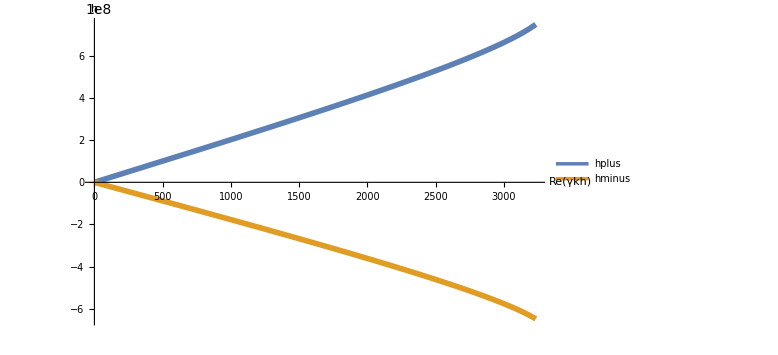

```mathematica
ListPlot[{hpkhdata,hmkhdata},
Joined->True,
ImageSize->Large,
PlotStyle->Thickness[0.007],
AxesLabel->{"Re(γkh)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

```mathematica
Re[hplusrtlist]
```

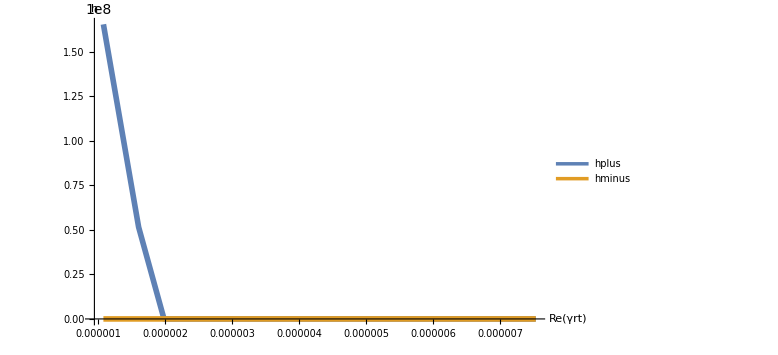

```mathematica
ListPlot[{hprtdata,hmrtdata},
Joined->True,
ImageSize->Large,
PlotStyle->Thickness[0.007],
AxesLabel->{"Re(γrt)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

```mathematica
hplusneglist = ParallelTable[N[hplus[g,c2,kx,drange[[i]]+U1,-Abs[Re[khroot[[i,2]]]]+I*Im[khroot[[i,2]]]]],{i,1001}];
hminusneglist = ParallelTable[N[hminus[g,c1,kx,U1,-Abs[Re[khroot[[i,2]]]]+I*Im[khroot[[i,2]]]]],{i,1001}];
```

```mathematica
Re[hplusneglist]
```

{7.49486×10^8,7.40511×10^8,7.31246×10^8,7.2168×10^8,7.11798×10^8,7.01588×10^8,6.91034×10^8,6.8012×10^8,6.68827×10^8,6.57135×10^8,6.45023×10^8,6.32465×10^8,6.19434×10^8,6.05899×10^8,5.91824×10^8,5.77171×10^8,5.61892×10^8,5.45935×10^8,5.29239×10^8,5.1173×10^8,4.93321×10^8,4.73907×10^8,4.53358×10^8,4.31513×10^8,4.08161×10^8,3.83027×10^8,3.55734×10^8,3.25737×10^8,2.92206×10^8,2.53741×10^8,2.07619×10^8,1.46788×10^8,402.121,52.4771,39.4209,33.6272,30.1796,27.8329,26.1055,24.7668,23.6907,22.8017,22.0516,21.4079,20.8477,20.3546,19.9163,19.5234,19.1686,18.8463,18.5517,18.2812,18.0316,17.8004,17.5856,17.3852,17.1977,17.0218,16.8564,16.7005,16.5532,16.4137,16.2814,16.1557,16.0361,15.922,15.8132,15.7091,15.6095,15.5141,15.4225,15.3346,15.2501,15.1687,15.0903,15.0147,14.9418,14.8714,14.8033,14.7375,14.6738,14.6121,14.5522,14.4942,14.438,14.3833,14.3302,14.2786,14.2284,14.1796,14.1321,14.0858,14.0407,13.9968,13.9539,13.9121,13.8713,13.8315,13.7926,13.7546,13.7175,13.6812,13.6457,13.6109,13.5769,13.5437,13.5111,13.4792,13.448,13.4173,13.3873,13.3579,13.3291,13.3008,13.273,13.2457,13.219,13.1927,13.167,13.1416,13.1168,13.0923,13.0683,13.0447,13.0215,12.9987,12.9763,12.9542,12.9325,12.9111,12.8901,12.8694,12.849,12.829,12.8092,12.7898,12.7706,12.7518,12.7332,12.7149,12.6968,12.679,12.6615,12.6442,12.6272,12.6103,12.5938,12.5774,12.5613,12.5454,12.5297,12.5142,12.4989,12.4838,12.4689,12.4542,12.4397,12.4254,12.4112,12.3972,12.3834,12.3698,12.3563,12.343,12.3299,12.3169,12.3041,12.2914,12.2789,12.2665,12.2542,12.2421,12.2301,12.2183,12.2066,12.195,12.1836,12.1723,12.1611,12.15,12.1391,12.1282,12.1175,12.1069,12.0964,12.0861,12.0758,12.0656,12.0556,12.0456,12.0357,12.026,12.0163,12.0068,11.9973,11.9879,11.9786,11.9694,11.9603,11.9513,11.9424,11.9335,11.9248,11.9161,11.9075,11.899,11.8906,11.8822,11.8739,11.8657,11.8576,11.8495,11.8416,11.8337,11.8258,11.818,11.8103,11.8027,11.7951,11.7876,11.7802,11.7728,11.7655,11.7583,11.7511,11.744,11.7369,11.7299,11.723,11.7161,11.7092,11.7025,11.6957,11.6891,11.6825,11.6759,11.6694,11.663,11.6566,11.6502,11.6439,11.6377,11.6315,11.6253,11.6192,11.6131,11.6071,11.6012,11.5953,11.5894,11.5836,11.5778,11.572,11.5663,11.5607,11.5551,11.5495,11.544,11.5385,11.533,11.5276,11.5222,11.5169,11.5116,11.5063,11.5011,11.4959,11.4908,11.4857,11.4806,11.4756,11.4706,11.4656,11.4607,11.4558,11.4509,11.4461,11.4413,11.4365,11.4318,11.4271,11.4224,11.4178,11.4132,11.4086,11.404,11.3995,11.395,11.3906,11.3861,11.3817,11.3774,11.373,11.3687,11.3644,11.3602,11.3559,11.3517,11.3476,11.3434,11.3393,11.3352,11.3311,11.327,11.323,11.319,11.315,11.3111,11.3072,11.3033,11.2994,11.2955,11.2917,11.2879,11.2841,11.2803,11.2766,11.2729,11.2692,11.2655,11.2619,11.2582,11.2546,11.251,11.2475,11.2439,11.2404,11.2369,11.2334,11.2299,11.2265,11.223,11.2196,11.2162,11.2129,11.2095,11.2062,11.2029,11.1996,11.1963,11.1931,11.1898,11.1866,11.1834,11.1802,11.177,11.1739,11.1707,11.1676,11.1645,11.1614,11.1584,11.1553,11.1523,11.1493,11.1463,11.1433,11.1403,11.1374,11.1344,11.1315,11.1286,11.1257,11.1228,11.1199,11.1171,11.1143,11.1114,11.1086,11.1058,11.1031,11.1003,11.0976,11.0948,11.0921,11.0894,11.0867,11.084,11.0814,11.0787,11.0761,11.0734,11.0708,11.0682,11.0656,11.0631,11.0605,11.0579,11.0554,11.0529,11.0504,11.0479,11.0454,11.0429,11.0404,11.038,11.0355,11.0331,11.0307,11.0283,11.0259,11.0235,11.0211,11.0188,11.0164,11.0141,11.0117,11.0094,11.0071,11.0048,11.0025,11.0003,10.998,10.9957,10.9935,10.9913,10.989,10.9868,10.9846,10.9824,10.9802,10.9781,10.9759,10.9737,10.9716,10.9695,10.9673,10.9652,10.9631,10.961,10.9589,10.9568,10.9548,10.9527,10.9506,10.9486,10.9466,10.9445,10.9425,10.9405,10.9385,10.9365,10.9345,10.9326,10.9306,10.9286,10.9267,10.9247,10.9228,10.9209,10.919,10.9171,10.9152,10.9133,10.9114,10.9095,10.9076,10.9058,10.9039,10.9021,10.9002,10.8984,10.8966,10.8948,10.893,10.8912,10.8894,10.8876,10.8858,10.884,10.8823,10.8805,10.8787,10.877,10.8753,10.8735,10.8718,10.8701,10.8684,10.8667,10.865,10.8633,10.8616,10.8599,10.8583,10.8566,10.8549,10.8533,10.8517,10.85,10.8484,10.8468,10.8451,10.8435,10.8419,10.8403,10.8387,10.8371,10.8356,10.834,10.8324,10.8309,10.8293,10.8277,10.8262,10.8247,10.8231,10.8216,10.8201,10.8186,10.817,10.8155,10.814,10.8125,10.8111,10.8096,10.8081,10.8066,10.8051,10.8037,10.8022,10.8008,10.7993,10.7979,10.7965,10.795,10.7936,10.7922,10.7908,10.7894,10.7879,10.7865,10.7852,10.7838,10.7824,10.781,10.7796,10.7783,10.7769,10.7755,10.7742,10.7728,10.7715,10.7701,10.7688,10.7675,10.7661,10.7648,10.7635,10.7622,10.7609,10.7596,10.7583,10.757,10.7557,10.7544,10.7531,10.7518,10.7506,10.7493,10.748,10.7468,10.7455,10.7443,10.743,10.7418,10.7405,10.7393,10.7381,10.7368,10.7356,10.7344,10.7332,10.732,10.7308,10.7296,10.7284,10.7272,10.726,10.7248,10.7236,10.7224,10.7212,10.7201,10.7189,10.7177,10.7166,10.7154,10.7143,10.7131,10.712,10.7108,10.7097,10.7086,10.7074,10.7063,10.7052,10.7041,10.7029,10.7018,10.7007,10.6996,10.6985,10.6974,10.6963,10.6952,10.6941,10.6931,10.692,10.6909,10.6898,10.6888,10.6877,10.6866,10.6856,10.6845,10.6834,10.6824,10.6813,10.6803,10.6793,10.6782,10.6772,10.6762,10.6751,10.6741,10.6731,10.6721,10.671,10.67,10.669,10.668,10.667,10.666,10.665,10.664,10.663,10.662,10.661,10.6601,10.6591,10.6581,10.6571,10.6562,10.6552,10.6542,10.6533,10.6523,10.6513,10.6504,10.6494,10.6485,10.6475,10.6466,10.6457,10.6447,10.6438,10.6429,10.6419,10.641,10.6401,10.6391,10.6382,10.6373,10.6364,10.6355,10.6346,10.6337,10.6328,10.6319,10.631,10.6301,10.6292,10.6283,10.6274,10.6265,10.6256,10.6248,10.6239,10.623,10.6221,10.6213,10.6204,10.6195,10.6187,10.6178,10.6169,10.6161,10.6152,10.6144,10.6135,10.6127,10.6118,10.611,10.6102,10.6093,10.6085,10.6077,10.6068,10.606,10.6052,10.6044,10.6035,10.6027,10.6019,10.6011,10.6003,10.5995,10.5986,10.5978,10.597,10.5962,10.5954,10.5946,10.5938,10.5931,10.5923,10.5915,10.5907,10.5899,10.5891,10.5883,10.5876,10.5868,10.586,10.5852,10.5845,10.5837,10.5829,10.5822,10.5814,10.5807,10.5799,10.5791,10.5784,10.5776,10.5769,10.5761,10.5754,10.5746,10.5739,10.5732,10.5724,10.5717,10.571,10.5702,10.5695,10.5688,10.568,10.5673,10.5666,10.5659,10.5651,10.5644,10.5637,10.563,10.5623,10.5616,10.5609,10.5602,10.5595,10.5587,10.558,10.5573,10.5566,10.556,10.5553,10.5546,10.5539,10.5532,10.5525,10.5518,10.5511,10.5504,10.5498,10.5491,10.5484,10.5477,10.5471,10.5464,10.5457,10.545,10.5444,10.5437,10.543,10.5424,10.5417,10.5411,10.5404,10.5398,10.5391,10.5384,10.5378,10.5371,10.5365,10.5358,10.5352,10.5346,10.5339,10.5333,10.5326,10.532,10.5314,10.5307,10.5301,10.5295,10.5288,10.5282,10.5276,10.527,10.5263,10.5257,10.5251,10.5245,10.5239,10.5232,10.5226,10.522,10.5214,10.5208,10.5202,10.5196,10.519,10.5184,10.5178,10.5171,10.5165,10.5159,10.5154,10.5148,10.5142,10.5136,10.513,10.5124,10.5118,10.5112,10.5106,10.51,10.5094,10.5089,10.5083,10.5077,10.5071,10.5065,10.506,10.5054,10.5048,10.5042,10.5037,10.5031,10.5025,10.502,10.5014,10.5008,10.5003,10.4997,10.4992,10.4986,10.498,10.4975,10.4969,10.4964,10.4958,10.4953,10.4947,10.4942,10.4936,10.4931,10.4925,10.492,10.4914,10.4909,10.4904,10.4898,10.4893,10.4887,10.4882,10.4877,10.4871,10.4866,10.4861,10.4855,10.485,10.4845,10.4839,10.4834,10.4829,10.4824,10.4819,10.4813,10.4808,10.4803,10.4798,10.4793,10.4787,10.4782,10.4777,10.4772,10.4767,10.4762,10.4757,10.4752,10.4747,10.4741,10.4736,10.4731,10.4726,10.4721,10.4716,10.4711,10.4706,10.4701,10.4696,10.4691,10.4687,10.4682,10.4677,10.4672,10.4667,10.4662,10.4657,10.4652,10.4647,10.4643,10.4638,10.4633,10.4628,10.4623,10.4618,10.4614,10.4609,10.4604,10.4599,10.4595,10.459,10.4585,10.458,10.4576,10.4571,10.4566,10.4562,10.4557,10.4552,10.4548,10.4543,10.4538,10.4534,10.4529,10.4525,10.452,10.4515,10.4511,10.4506,10.4502,10.4497,10.4493,10.4488,10.4483,10.4479,10.4474,10.447,10.4466,10.4461,10.4457,10.4452,10.4448,10.4443,10.4439,10.4434,10.443,10.4426,10.4421,10.4417,10.4412,10.4408,10.4404,10.4399,10.4395,10.4391,10.4386,10.4382,10.4378,10.4373,10.4369,10.4365,10.436,10.4356,10.4352,10.4348,10.4343,10.4339,10.4335,10.4331,10.4327,10.4322,10.4318,10.4314,10.431,10.4306,10.4302,10.4297}

```mathematica
Re[hminusneglist[[1]]]
```

-6.4813×10^8

```mathematica
hpnegdata=Thread[{Abs[Re[khrootdata]],Re[hplusneglist]}];
hmnegdata=Thread[{Abs[Re[khrootdata]],Re[hminusneglist]}];
```

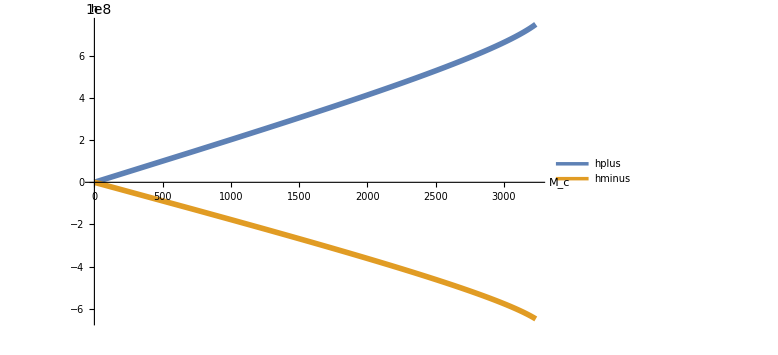

```mathematica
ListPlot[{hpnegdata,hmnegdata},
Joined->True,
ImageSize->Large,
PlotStyle->Thickness[0.007],
AxesLabel->{"M_c","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

### A=0.9

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
d2range =Range[107178,1500492,1340];
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

```mathematica
(*TableForm[a2]*)
```

```mathematica
khroot2 = Flatten[Append[a2[[1;;34,1]],a2[[35;;All,3]]]];
rtroot2=  Flatten[Append[a2[[1;;34,3]],a2[[35;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,d2range}];
```

```mathematica
khrootdata2 = khroot2[[All,2]]/Sqrt[g*kx];
rtrootdata2 = rtroot2[[All,2]]/Sqrt[g*kx];
khapprox2 = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,d2range}];
rtapprox2 = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,d2range}];
```

```mathematica
data5 = Thread[{dvals2,Abs[Re[khrootdata2]]}];
data6 = Thread[{dvals2,khapprox2}];
data7 = Thread[{dvals2,Abs[Re[rtrootdata2]]}];
data8 = Thread[{dvals2,rtapprox2}];
```

```mathematica
Length[d2range]
```

1040

```mathematica
hpluslist2 = ParallelTable[N[hplus[g,c2,kx,d2range[[i]]+U1,Abs[Re[khroot2[[i,2]]]]+I*Im[khroot2[[i,2]]]]],{i,1040}];
hminuslist2 = ParallelTable[N[hminus[g,c1,kx,U1,Abs[Re[khroot2[[i,2]]]]+I*Im[khroot2[[i,2]]]]],{i,1040}];
hplusrtlist2 = ParallelTable[N[hplus[g,c2,kx,d2range[[i]]+U1,Abs[Re[rtroot2[[i,2]]]]+I*Im[rtroot2[[i,2]]]]],{i,Length[rtroot2]}];
hminusrtlist2= ParallelTable[N[hminus[g,c1,kx,U1,Abs[Re[rtroot2[[i,2]]]]+I*Im[rtroot2[[i,2]]]]],{i,Length[rtroot2]}];
```

```mathematica
Re[hminusrtlist2]
```

```mathematica
Re[hpluslist2]
```

{8.00249×10^9,7.84935×10^9,7.6927×10^9,7.53225×10^9,7.36771×10^9,7.19874×10^9,7.02498×10^9,6.846×10^9,6.66135×10^9,6.47047×10^9,6.27276×10^9,6.06751×10^9,5.85387×10^9,5.63084×10^9,5.39722×10^9,5.15151×10^9,4.89185×10^9,4.61584×10^9,4.3203×10^9,4.00086×10^9,3.65118×10^9,3.26152×10^9,2.81525×10^9,2.2793×10^9,1.56394×10^9,462.313,161.437,121.99,103.472,92.1371,84.2663,78.3786,73.7514,69.9846,66.8363,64.1505,61.8215,59.7746,57.9556,56.3238,54.8481,53.5043,52.2731,51.139,50.0894,49.1138,48.2036,47.3515,46.5513,45.7977,45.0861,44.4125,43.7737,43.1664,42.5882,42.0366,41.5096,41.0053,40.522,40.0583,39.6128,39.1843,38.7717,38.374,37.9902,37.6196,37.2614,36.9149,36.5794,36.2543,35.9391,35.6333,35.3364,35.0479,34.7675,34.4948,34.2293,33.9709,33.7191,33.4737,33.2344,33.001,32.7732,32.5507,32.3335,32.1212,31.9136,31.7107,31.5122,31.318,31.1278,30.9417,30.7593,30.5807,30.4056,30.2339,30.0656,29.9006,29.7386,29.5797,29.4237,29.2706,29.1202,28.9725,28.8274,28.6848,28.5447,28.4069,28.2715,28.1383,28.0073,27.8784,27.7516,27.6268,27.5039,27.383,27.264,27.1467,27.0313,26.9175,26.8055,26.6951,26.5863,26.479,26.3733,26.2691,26.1664,26.065,25.9651,25.8665,25.7693,25.6734,25.5787,25.4853,25.3932,25.3022,25.2124,25.1237,25.0362,24.9497,24.8644,24.7801,24.6968,24.6146,24.5333,24.453,24.3737,24.2953,24.2178,24.1413,24.0656,23.9908,23.9168,23.8437,23.7714,23.7,23.6293,23.5594,23.4902,23.4218,23.3542,23.2873,23.2211,23.1556,23.0908,23.0266,22.9632,22.9004,22.8382,22.7767,22.7158,22.6555,22.5958,22.5367,22.4782,22.4203,22.363,22.3062,22.2499,22.1942,22.1391,22.0844,22.0303,21.9767,21.9236,21.871,21.8188,21.7672,21.716,21.6653,21.6151,21.5653,21.516,21.4671,21.4186,21.3706,21.323,21.2758,21.229,21.1826,21.1366,21.091,21.0458,21.001,20.9566,20.9126,20.8689,20.8256,20.7826,20.74,20.6977,20.6558,20.6143,20.573,20.5321,20.4916,20.4513,20.4114,20.3718,20.3325,20.2935,20.2548,20.2164,20.1784,20.1406,20.1031,20.0659,20.029,19.9923,19.9559,19.9198,19.884,19.8485,19.8132,19.7782,19.7434,19.7089,19.6746,19.6406,19.6068,19.5733,19.54,19.507,19.4742,19.4416,19.4093,19.3771,19.3453,19.3136,19.2821,19.2509,19.2199,19.1891,19.1585,19.1282,19.098,19.068,19.0383,19.0087,18.9794,18.9502,18.9212,18.8925,18.8639,18.8355,18.8073,18.7792,18.7514,18.7237,18.6963,18.669,18.6418,18.6149,18.5881,18.5615,18.535,18.5088,18.4827,18.4567,18.4309,18.4053,18.3798,18.3545,18.3294,18.3044,18.2796,18.2549,18.2303,18.2059,18.1817,18.1576,18.1337,18.1099,18.0862,18.0627,18.0393,18.016,17.9929,17.97,17.9471,17.9244,17.9019,17.8794,17.8571,17.8349,17.8129,17.791,17.7692,17.7475,17.7259,17.7045,17.6832,17.662,17.6409,17.62,17.5991,17.5784,17.5578,17.5373,17.517,17.4967,17.4765,17.4565,17.4366,17.4167,17.397,17.3774,17.3579,17.3385,17.3192,17.3,17.2809,17.2619,17.2431,17.2243,17.2056,17.187,17.1685,17.1501,17.1318,17.1136,17.0955,17.0775,17.0595,17.0417,17.024,17.0063,16.9888,16.9713,16.9539,16.9366,16.9194,16.9023,16.8852,16.8683,16.8514,16.8347,16.818,16.8013,16.7848,16.7684,16.752,16.7357,16.7195,16.7034,16.6873,16.6713,16.6554,16.6396,16.6239,16.6082,16.5926,16.5771,16.5617,16.5463,16.531,16.5158,16.5006,16.4855,16.4705,16.4556,16.4407,16.4259,16.4112,16.3965,16.3819,16.3674,16.3529,16.3385,16.3242,16.3099,16.2957,16.2816,16.2675,16.2535,16.2396,16.2257,16.2119,16.1981,16.1844,16.1708,16.1572,16.1437,16.1303,16.1169,16.1036,16.0903,16.0771,16.0639,16.0508,16.0378,16.0248,16.0119,15.999,15.9862,15.9734,15.9607,15.948,15.9354,15.9229,15.9104,15.898,15.8856,15.8733,15.861,15.8487,15.8366,15.8244,15.8124,15.8003,15.7884,15.7764,15.7646,15.7527,15.741,15.7292,15.7176,15.7059,15.6944,15.6828,15.6713,15.6599,15.6485,15.6371,15.6258,15.6146,15.6034,15.5922,15.5811,15.57,15.559,15.548,15.537,15.5261,15.5153,15.5045,15.4937,15.483,15.4723,15.4616,15.451,15.4405,15.43,15.4195,15.409,15.3986,15.3883,15.378,15.3677,15.3575,15.3473,15.3371,15.327,15.3169,15.3068,15.2968,15.2869,15.2769,15.2671,15.2572,15.2474,15.2376,15.2279,15.2181,15.2085,15.1988,15.1892,15.1797,15.1702,15.1607,15.1512,15.1418,15.1324,15.123,15.1137,15.1044,15.0952,15.086,15.0768,15.0676,15.0585,15.0494,15.0404,15.0314,15.0224,15.0134,15.0045,14.9956,14.9868,14.9779,14.9691,14.9604,14.9517,14.943,14.9343,14.9256,14.917,14.9085,14.8999,14.8914,14.8829,14.8744,14.866,14.8576,14.8492,14.8409,14.8326,14.8243,14.816,14.8078,14.7996,14.7914,14.7833,14.7752,14.7671,14.759,14.751,14.743,14.735,14.7271,14.7191,14.7113,14.7034,14.6955,14.6877,14.6799,14.6722,14.6644,14.6567,14.649,14.6414,14.6337,14.6261,14.6185,14.611,14.6034,14.5959,14.5884,14.581,14.5735,14.5661,14.5587,14.5513,14.544,14.5367,14.5294,14.5221,14.5149,14.5076,14.5004,14.4933,14.4861,14.479,14.4719,14.4648,14.4577,14.4507,14.4437,14.4367,14.4297,14.4227,14.4158,14.4089,14.402,14.3951,14.3883,14.3815,14.3747,14.3679,14.3611,14.3544,14.3477,14.341,14.3343,14.3277,14.321,14.3144,14.3078,14.3012,14.2947,14.2882,14.2816,14.2751,14.2687,14.2622,14.2558,14.2494,14.243,14.2366,14.2302,14.2239,14.2176,14.2113,14.205,14.1987,14.1925,14.1863,14.1801,14.1739,14.1677,14.1616,14.1554,14.1493,14.1432,14.1371,14.1311,14.125,14.119,14.113,14.107,14.101,14.0951,14.0892,14.0832,14.0773,14.0715,14.0656,14.0597,14.0539,14.0481,14.0423,14.0365,14.0307,14.025,14.0192,14.0135,14.0078,14.0021,13.9965,13.9908,13.9852,13.9796,13.9739,13.9684,13.9628,13.9572,13.9517,13.9462,13.9406,13.9352,13.9297,13.9242,13.9188,13.9133,13.9079,13.9025,13.8971,13.8917,13.8864,13.881,13.8757,13.8704,13.8651,13.8598,13.8545,13.8493,13.844,13.8388,13.8336,13.8284,13.8232,13.818,13.8129,13.8077,13.8026,13.7975,13.7924,13.7873,13.7822,13.7772,13.7721,13.7671,13.7621,13.757,13.7521,13.7471,13.7421,13.7372,13.7322,13.7273,13.7224,13.7175,13.7126,13.7077,13.7028,13.698,13.6932,13.6883,13.6835,13.6787,13.6739,13.6692,13.6644,13.6597,13.6549,13.6502,13.6455,13.6408,13.6361,13.6314,13.6267,13.6221,13.6175,13.6128,13.6082,13.6036,13.599,13.5944,13.5899,13.5853,13.5808,13.5762,13.5717,13.5672,13.5627,13.5582,13.5537,13.5493,13.5448,13.5404,13.5359,13.5315,13.5271,13.5227,13.5183,13.5139,13.5096,13.5052,13.5009,13.4965,13.4922,13.4879,13.4836,13.4793,13.475,13.4708,13.4665,13.4623,13.458,13.4538,13.4496,13.4454,13.4412,13.437,13.4328,13.4286,13.4245,13.4203,13.4162,13.4121,13.408,13.4039,13.3998,13.3957,13.3916,13.3875,13.3835,13.3794,13.3754,13.3714,13.3674,13.3633,13.3593,13.3554,13.3514,13.3474,13.3434,13.3395,13.3356,13.3316,13.3277,13.3238,13.3199,13.316,13.3121,13.3082,13.3043,13.3005,13.2966,13.2928,13.289,13.2851,13.2813,13.2775,13.2737,13.2699,13.2662,13.2624,13.2586,13.2549,13.2511,13.2474,13.2437,13.24,13.2362,13.2325,13.2288,13.2252,13.2215,13.2178,13.2142,13.2105,13.2069,13.2032,13.1996,13.196,13.1924,13.1888,13.1852,13.1816,13.178,13.1745,13.1709,13.1673,13.1638,13.1603,13.1567,13.1532,13.1497,13.1462,13.1427,13.1392,13.1357,13.1322,13.1288,13.1253,13.1219,13.1184,13.115,13.1116,13.1081,13.1047,13.1013,13.0979,13.0945,13.0912,13.0878,13.0844,13.081,13.0777,13.0743,13.071,13.0677,13.0643,13.061,13.0577,13.0544,13.0511,13.0478,13.0446,13.0413,13.038,13.0347,13.0315,13.0282,13.025,13.0218,13.0186,13.0153,13.0121,13.0089,13.0057,13.0025,12.9993,12.9962,12.993,12.9898,12.9867,12.9835,12.9804,12.9772,12.9741,12.971,12.9679,12.9648,12.9616,12.9585,12.9555,12.9524,12.9493,12.9462,12.9432,12.9401,12.937,12.934,12.931,12.9279,12.9249,12.9219,12.9189,12.9158,12.9128,12.9098,12.9069,12.9039,12.9009,12.8979,12.895,12.892,12.889,12.8861,12.8831,12.8802,12.8773,12.8744,12.8714,12.8685,12.8656,12.8627,12.8598,12.8569,12.8541,12.8512,12.8483,12.8454,12.8426,12.8397,12.8369,12.834,12.8312,12.8284,12.8255,12.8227,12.8199,12.8171,12.8143,12.8115,12.8087,12.8059,12.8031,12.8004,12.7976,12.7948,12.7921,12.7893,12.7866,12.7838,12.7811,12.7784,12.7756,12.7729,12.7702,12.7675,12.7648,12.7621,12.7594,12.7567,12.754,12.7513,12.7487,12.746,12.7433,12.7407,12.738,12.7354,12.7327,12.7301,12.7275,12.7249,12.7222,12.7196,12.717,12.7144,12.7118,12.7092,12.7066,12.704,12.7014,12.6989,12.6963,12.6937,12.6912,12.6886,12.686,12.6835,12.681,12.6784,12.6759,12.6734,12.6708,12.6683,12.6658,12.6633,12.6608,12.6583,12.6558,12.6533,12.6508,12.6483,12.6459,12.6434,12.6409,12.6385,12.636,12.6335,12.6311,12.6287,12.6262,12.6238,12.6214,12.6189,12.6165,12.6141,12.6117,12.6093,12.6069,12.6045,12.6021,12.5997,12.5973,12.5949,12.5925,12.5902,12.5878,12.5854,12.5831,12.5807,12.5784,12.576,12.5737}

```mathematica
Re[hminuslist2]
```

{-9.58774×10^8,-9.48195×10^8,-9.3677×10^8,-9.24463×10^8,-9.11234×10^8,-8.97039×10^8,-8.81827×10^8,-8.65541×10^8,-8.48116×10^8,-8.29478×10^8,-8.09539×10^8,-7.882×10^8,-7.65339×10^8,-7.40814×10^8,-7.14451×10^8,-6.86037×10^8,-6.55302×10^8,-6.21901×10^8,-5.85376×10^8,-5.45097×10^8,-5.00156×10^8,-4.49155×10^8,-3.89719×10^8,-3.17138×10^8,-2.18694×10^8,-57.5015,-15.6219,-10.2923,-7.85518,-6.40114,-5.41679,-4.69866,-4.14808,-3.71069,-3.35384,-3.05659,-2.80482,-2.58862,-2.40084,-2.23616,-2.09052,-1.96077,-1.84446,-1.73959,-1.64456,-1.55807,-1.47901,-1.4065,-1.33975,-1.27812,-1.22106,-1.16808,-1.11879,-1.07281,-1.02983,-0.989579,-0.951817,-0.916325,-0.882914,-0.851413,-0.82167,-0.793549,-0.766926,-0.741692,-0.717745,-0.694995,-0.673359,-0.652762,-0.633135,-0.614414,-0.596543,-0.579468,-0.563141,-0.547517,-0.532553,-0.518213,-0.504459,-0.491261,-0.478586,-0.466407,-0.454697,-0.443432,-0.432588,-0.422144,-0.412081,-0.402378,-0.39302,-0.383988,-0.375269,-0.366846,-0.358707,-0.350838,-0.343228,-0.335864,-0.328737,-0.321835,-0.31515,-0.308672,-0.302393,-0.296303,-0.290397,-0.284665,-0.279102,-0.2737,-0.268453,-0.263356,-0.258403,-0.253587,-0.248905,-0.24435,-0.239919,-0.235607,-0.23141,-0.227323,-0.223343,-0.219466,-0.215688,-0.212007,-0.208418,-0.204919,-0.201506,-0.198177,-0.194929,-0.19176,-0.188667,-0.185647,-0.182698,-0.179818,-0.177005,-0.174257,-0.171571,-0.168947,-0.166381,-0.163873,-0.16142,-0.159021,-0.156674,-0.154379,-0.152132,-0.149934,-0.147782,-0.145676,-0.143613,-0.141594,-0.139616,-0.137678,-0.13578,-0.13392,-0.132098,-0.130312,-0.128561,-0.126845,-0.125162,-0.123512,-0.121894,-0.120307,-0.11875,-0.117223,-0.115724,-0.114254,-0.11281,-0.111394,-0.110003,-0.108638,-0.107298,-0.105981,-0.104689,-0.103419,-0.102172,-0.100947,-0.0997435,-0.0985608,-0.0973987,-0.0962566,-0.095134,-0.0940306,-0.0929459,-0.0918794,-0.0908309,-0.0897998,-0.0887858,-0.0877885,-0.0868076,-0.0858427,-0.0848935,-0.0839596,-0.0830407,-0.0821365,-0.0812466,-0.0803709,-0.0795089,-0.0786604,-0.0778251,-0.0770028,-0.0761932,-0.075396,-0.074611,-0.0738379,-0.0730765,-0.0723265,-0.0715878,-0.0708601,-0.0701432,-0.0694369,-0.068741,-0.0680552,-0.0673794,-0.0667135,-0.0660571,-0.0654101,-0.0647724,-0.0641438,-0.0635241,-0.0629131,-0.0623107,-0.0617167,-0.061131,-0.0605534,-0.0599838,-0.0594219,-0.0588678,-0.0583212,-0.057782,-0.0572501,-0.0567253,-0.0562075,-0.0556967,-0.0551926,-0.0546952,-0.0542043,-0.0537199,-0.0532417,-0.0527698,-0.052304,-0.0518442,-0.0513903,-0.0509422,-0.0504998,-0.050063,-0.0496317,-0.0492058,-0.0487853,-0.04837,-0.0479599,-0.0475548,-0.0471548,-0.0467597,-0.0463694,-0.0459838,-0.0456029,-0.0452267,-0.0448549,-0.0444877,-0.0441248,-0.0437662,-0.0434119,-0.0430618,-0.0427158,-0.0423739,-0.042036,-0.041702,-0.0413719,-0.0410455,-0.040723,-0.0404042,-0.040089,-0.0397773,-0.0394693,-0.0391647,-0.0388635,-0.0385658,-0.0382713,-0.0379802,-0.0376923,-0.0374075,-0.0371259,-0.0368475,-0.036572,-0.0362996,-0.0360301,-0.0357636,-0.0354999,-0.0352391,-0.0349811,-0.0347258,-0.0344733,-0.0342234,-0.0339762,-0.0337316,-0.0334896,-0.0332501,-0.0330131,-0.0327786,-0.0325465,-0.0323169,-0.0320896,-0.0318646,-0.0316419,-0.0314215,-0.0312034,-0.0309875,-0.0307737,-0.0305621,-0.0303527,-0.0301453,-0.02994,-0.0297368,-0.0295355,-0.0293363,-0.029139,-0.0289437,-0.0287503,-0.0285588,-0.0283691,-0.0281813,-0.0279953,-0.0278111,-0.0276287,-0.027448,-0.027269,-0.0270918,-0.0269162,-0.0267423,-0.0265701,-0.0263995,-0.0262305,-0.026063,-0.0258971,-0.0257328,-0.02557,-0.0254087,-0.0252489,-0.0250906,-0.0249337,-0.0247783,-0.0246242,-0.0244716,-0.0243204,-0.0241705,-0.024022,-0.0238748,-0.0237289,-0.0235844,-0.0234411,-0.0232991,-0.0231584,-0.0230189,-0.0228807,-0.0227436,-0.0226078,-0.0224731,-0.0223397,-0.0222073,-0.0220762,-0.0219461,-0.0218172,-0.0216894,-0.0215627,-0.0214371,-0.0213126,-0.0211891,-0.0210666,-0.0209452,-0.0208249,-0.0207055,-0.0205872,-0.0204698,-0.0203534,-0.020238,-0.0201235,-0.02001,-0.0198975,-0.0197858,-0.0196751,-0.0195653,-0.0194564,-0.0193483,-0.0192412,-0.0191349,-0.0190295,-0.0189249,-0.0188212,-0.0187183,-0.0186163,-0.018515,-0.0184146,-0.0183149,-0.0182161,-0.018118,-0.0180207,-0.0179242,-0.0178284,-0.0177334,-0.0176391,-0.0175456,-0.0174528,-0.0173607,-0.0172693,-0.0171787,-0.0170887,-0.0169994,-0.0169108,-0.0168229,-0.0167356,-0.0166491,-0.0165631,-0.0164779,-0.0163932,-0.0163092,-0.0162259,-0.0161431,-0.016061,-0.0159795,-0.0158986,-0.0158183,-0.0157386,-0.0156595,-0.015581,-0.015503,-0.0154257,-0.0153489,-0.0152726,-0.0151969,-0.0151218,-0.0150472,-0.0149731,-0.0148996,-0.0148266,-0.0147542,-0.0146822,-0.0146108,-0.0145399,-0.0144695,-0.0143996,-0.0143302,-0.0142612,-0.0141928,-0.0141249,-0.0140574,-0.0139904,-0.0139239,-0.0138578,-0.0137922,-0.013727,-0.0136623,-0.0135981,-0.0135343,-0.0134709,-0.013408,-0.0133455,-0.0132834,-0.0132218,-0.0131606,-0.0130998,-0.0130394,-0.0129794,-0.0129198,-0.0128606,-0.0128019,-0.0127435,-0.0126855,-0.0126279,-0.0125707,-0.0125138,-0.0124574,-0.0124013,-0.0123456,-0.0122902,-0.0122353,-0.0121806,-0.0121264,-0.0120725,-0.0120189,-0.0119657,-0.0119129,-0.0118604,-0.0118082,-0.0117564,-0.0117049,-0.0116537,-0.0116029,-0.0115524,-0.0115022,-0.0114523,-0.0114028,-0.0113535,-0.0113046,-0.011256,-0.0112077,-0.0111597,-0.011112,-0.0110646,-0.0110175,-0.0109707,-0.0109242,-0.010878,-0.0108321,-0.0107864,-0.0107411,-0.010696,-0.0106512,-0.0106067,-0.0105624,-0.0105184,-0.0104747,-0.0104313,-0.0103881,-0.0103452,-0.0103025,-0.0102601,-0.010218,-0.0101761,-0.0101345,-0.0100931,-0.010052,-0.0100111,-0.00997046,-0.00993007,-0.00988992,-0.00985,-0.00981033,-0.00977089,-0.00973168,-0.0096927,-0.00965396,-0.00961544,-0.00957715,-0.00953908,-0.00950124,-0.00946362,-0.00942622,-0.00938903,-0.00935207,-0.00931531,-0.00927877,-0.00924244,-0.00920632,-0.00917041,-0.00913471,-0.00909921,-0.00906391,-0.00902881,-0.00899392,-0.00895922,-0.00892473,-0.00889042,-0.00885631,-0.0088224,-0.00878868,-0.00875514,-0.0087218,-0.00868864,-0.00865567,-0.00862288,-0.00859028,-0.00855786,-0.00852561,-0.00849355,-0.00846167,-0.00842996,-0.00839843,-0.00836707,-0.00833588,-0.00830487,-0.00827402,-0.00824335,-0.00821284,-0.0081825,-0.00815232,-0.00812231,-0.00809246,-0.00806278,-0.00803325,-0.00800388,-0.00797468,-0.00794563,-0.00791673,-0.00788799,-0.00785941,-0.00783097,-0.00780269,-0.00777456,-0.00774658,-0.00771875,-0.00769107,-0.00766353,-0.00763614,-0.00760889,-0.00758179,-0.00755483,-0.00752801,-0.00750133,-0.00747479,-0.00744839,-0.00742212,-0.007396,-0.00737001,-0.00734415,-0.00731843,-0.00729284,-0.00726738,-0.00724206,-0.00721686,-0.0071918,-0.00716686,-0.00714205,-0.00711737,-0.00709281,-0.00706838,-0.00704407,-0.00701989,-0.00699582,-0.00697189,-0.00694807,-0.00692437,-0.00690079,-0.00687733,-0.00685399,-0.00683076,-0.00680765,-0.00678466,-0.00676178,-0.00673902,-0.00671636,-0.00669382,-0.0066714,-0.00664908,-0.00662687,-0.00660478,-0.00658279,-0.00656091,-0.00653914,-0.00651747,-0.00649592,-0.00647446,-0.00645311,-0.00643187,-0.00641073,-0.00638969,-0.00636875,-0.00634791,-0.00632718,-0.00630655,-0.00628601,-0.00626557,-0.00624524,-0.006225,-0.00620485,-0.00618481,-0.00616485,-0.006145,-0.00612524,-0.00610557,-0.00608599,-0.00606651,-0.00604712,-0.00602783,-0.00600862,-0.0059895,-0.00597048,-0.00595154,-0.00593269,-0.00591393,-0.00589526,-0.00587667,-0.00585818,-0.00583976,-0.00582144,-0.0058032,-0.00578504,-0.00576697,-0.00574898,-0.00573107,-0.00571325,-0.00569551,-0.00567784,-0.00566027,-0.00564277,-0.00562535,-0.00560801,-0.00559075,-0.00557357,-0.00555646,-0.00553944,-0.00552249,-0.00550562,-0.00548882,-0.0054721,-0.00545546,-0.00543889,-0.00542239,-0.00540597,-0.00538962,-0.00537335,-0.00535715,-0.00534102,-0.00532496,-0.00530897,-0.00529306,-0.00527721,-0.00526144,-0.00524574,-0.0052301,-0.00521453,-0.00519904,-0.00518361,-0.00516825,-0.00515295,-0.00513772,-0.00512256,-0.00510747,-0.00509244,-0.00507748,-0.00506258,-0.00504775,-0.00503298,-0.00501827,-0.00500363,-0.00498905,-0.00497454,-0.00496009,-0.0049457,-0.00493137,-0.0049171,-0.00490289,-0.00488875,-0.00487466,-0.00486064,-0.00484667,-0.00483277,-0.00481892,-0.00480513,-0.0047914,-0.00477773,-0.00476412,-0.00475056,-0.00473706,-0.00472362,-0.00471024,-0.00469691,-0.00468363,-0.00467041,-0.00465725,-0.00464414,-0.00463109,-0.00461809,-0.00460515,-0.00459226,-0.00457942,-0.00456663,-0.0045539,-0.00454122,-0.0045286,-0.00451602,-0.0045035,-0.00449103,-0.00447861,-0.00446624,-0.00445392,-0.00444165,-0.00442943,-0.00441726,-0.00440514,-0.00439307,-0.00438105,-0.00436908,-0.00435716,-0.00434528,-0.00433345,-0.00432168,-0.00430994,-0.00429826,-0.00428662,-0.00427503,-0.00426348,-0.00425198,-0.00424053,-0.00422912,-0.00421776,-0.00420645,-0.00419518,-0.00418395,-0.00417277,-0.00416163,-0.00415054,-0.00413949,-0.00412848,-0.00411752,-0.0041066,-0.00409572,-0.00408489,-0.00407409,-0.00406335,-0.00405264,-0.00404197,-0.00403135,-0.00402077,-0.00401022,-0.00399972,-0.00398926,-0.00397885,-0.00396847,-0.00395813,-0.00394783,-0.00393757,-0.00392735,-0.00391717,-0.00390703,-0.00389693,-0.00388687,-0.00387684,-0.00386686,-0.00385691,-0.003847,-0.00383712,-0.00382729,-0.00381749,-0.00380773,-0.00379801,-0.00378832,-0.00377867,-0.00376906,-0.00375948,-0.00374994,-0.00374044,-0.00373097,-0.00372153,-0.00371213,-0.00370277,-0.00369344,-0.00368415,-0.00367489,-0.00366567,-0.00365648,-0.00364732,-0.0036382,-0.00362911,-0.00362006,-0.00361104,-0.00360205,-0.0035931,-0.00358418,-0.00357529,-0.00356643,-0.00355761,-0.00354882,-0.00354006,-0.00353134,-0.00352264,-0.00351398,-0.00350535,-0.00349675,-0.00348818,-0.00347964,-0.00347114,-0.00346266,-0.00345422,-0.0034458,-0.00343742,-0.00342907,-0.00342074,-0.00341245,-0.00340419,-0.00339595,-0.00338775,-0.00337958,-0.00337143,-0.00336331,-0.00335523,-0.00334717,-0.00333914,-0.00333114,-0.00332317,-0.00331522,-0.00330731,-0.00329942,-0.00329156,-0.00328373,-0.00327592,-0.00326814,-0.00326039,-0.00325267,-0.00324498,-0.00323731,-0.00322967,-0.00322205,-0.00321447,-0.0032069,-0.00319937,-0.00319186,-0.00318438,-0.00317692,-0.00316949,-0.00316209,-0.00315471,-0.00314735,-0.00314003,-0.00313272,-0.00312545,-0.00311819,-0.00311097,-0.00310376,-0.00309659,-0.00308943,-0.0030823,-0.0030752,-0.00306812,-0.00306107,-0.00305403,-0.00304703,-0.00304004,-0.00303308,-0.00302615,-0.00301923,-0.00301234,-0.00300548,-0.00299864,-0.00299182,-0.00298502,-0.00297825,-0.0029715,-0.00296477,-0.00295806,-0.00295138,-0.00294472,-0.00293808,-0.00293147,-0.00292487,-0.0029183,-0.00291175,-0.00290522,-0.00289872,-0.00289223,-0.00288577,-0.00287933,-0.00287291,-0.00286651,-0.00286013,-0.00285377,-0.00284744,-0.00284112,-0.00283483,-0.00282856,-0.0028223,-0.00281607,-0.00280986,-0.00280367,-0.0027975,-0.00279135,-0.00278522,-0.00277911,-0.00277302,-0.00276695,-0.00276089,-0.00275486,-0.00274885,-0.00274286,-0.00273689,-0.00273093,-0.002725,-0.00271908,-0.00271319,-0.00270731,-0.00270145,-0.00269561,-0.00268979,-0.00268399,-0.0026782,-0.00267244,-0.00266669,-0.00266096,-0.00265525,-0.00264956,-0.00264389,-0.00263823,-0.0026326,-0.00262698,-0.00262138,-0.00261579,-0.00261023,-0.00260468,-0.00259915,-0.00259363,-0.00258814,-0.00258266,-0.0025772,-0.00257175,-0.00256632,-0.00256091,-0.00255552,-0.00255014,-0.00254478,-0.00253944,-0.00253411,-0.0025288,-0.00252351,-0.00251823,-0.00251297,-0.00250773,-0.0025025,-0.00249729,-0.00249209,-0.00248692,-0.00248175,-0.0024766,-0.00247147,-0.00246636,-0.00246126,-0.00245617,-0.0024511,-0.00244605,-0.00244101,-0.00243599,-0.00243098,-0.00242599,-0.00242102,-0.00241606,-0.00241111,-0.00240618,-0.00240126,-0.00239636,-0.00239148,-0.0023866,-0.00238175,-0.00237691,-0.00237208,-0.00236727,-0.00236247,-0.00235768,-0.00235291,-0.00234816,-0.00234342,-0.00233869,-0.00233398,-0.00232928,-0.0023246,-0.00231993,-0.00231527,-0.00231063,-0.002306}

```mathematica
hpdata2=Thread[{Abs[Re[khrootdata2]],Re[hpluslist2]}];
hmdata2=Thread[{Abs[Re[khrootdata2]],Re[hminuslist2]}];
hprtdata2=Thread[{Abs[Re[rtrootdata2]],Re[hplusrtlist2]}];
hmrtdata2=Thread[{Abs[Re[rtrootdata2]],Re[hminusrtlist2]}];
```

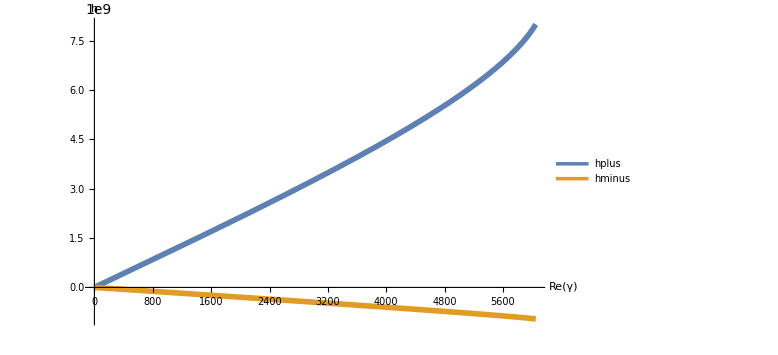

```mathematica
ListPlot[{hpdata2,hmdata2},
Joined->True,
ImageSize->Large,
PlotStyle->Thickness[0.007],
AxesLabel->{"Re(γ)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

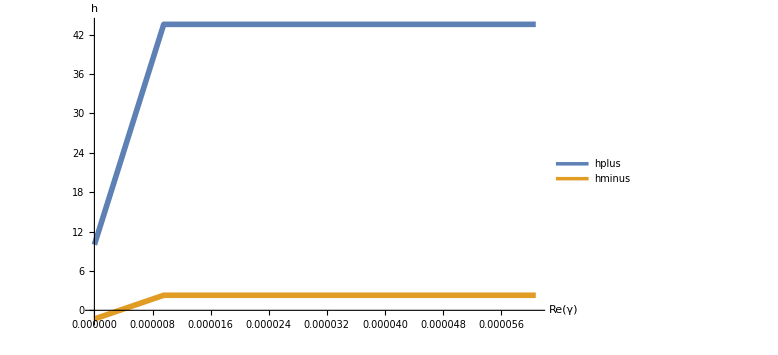

```mathematica
ListPlot[{hprtdata2,hmrtdata2},
Joined->True,
ImageSize->Large,
PlotStyle->Thickness[0.007],
AxesLabel->{"Re(γ)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

## Testing h+- with B

```mathematica
ClearAll[ρ1,ρ2,P,U1,U2,g,kx,ky,B,μ,K]
```

```mathematica
ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}]
```

1/2 ((g ((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1) ρ1)/(P ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1)^2+4 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (ⅈ kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (ⅈ kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (ⅈ kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2)))

```mathematica
hminus[ρ1_,P_,U1_,g_,kx_,ky_,B_,μ_,γ_]:=1/2 ((g ((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1) ρ1)/(P ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1)^2+4 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (ⅈ kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (ⅈ kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (ⅈ kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2)));
```

```mathematica
ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}]
```

1/2 ((g ((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2) ρ2)/(P ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2)^2+4 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (ⅈ kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (ⅈ kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (ⅈ kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2)))

```mathematica
hplus[ρ2_,P_,U2_,g_,kx_,ky_,B_,μ_,γ_]:=1/2 ((g ((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2) ρ2)/(P ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2)^2+4 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (ⅈ kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (ⅈ kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (ⅈ kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2)));
```

#### KH

Data  should  have  the  form  of[ρ1, ρ2, P, c1, c2, U1, d, Mc (8), g, kx, ky, B (12), β (13), Re (γ), Im (γ)]  (15  items)

```mathematica
plotdatakh600 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotb600 = plotdatakh600[[;;,12]];
plotbeta600=plotdatakh600[[;;,13]];
plotgamma600 =Abs[ plotdatakh600[[;;,14]]];
plotgammaim600=plotdatakh600[[;;,15]];
plotgammanorm600=Abs[plotdatakh600[[;;,14]]/Sqrt[10]];
betadata600=Thread[{plotbeta600,plotgammanorm600}];
bdata600 = Thread[{plotb600,plotgamma600}];
bdataim600 = Thread[{plotb600,plotgammaim600}];
plotb600norm  = plotdatakh600[[;;,12]]/√(4*π*10^-7*(plotdatakh600[[1]][[1]]+plotdatakh600[[1]][[2]]))*(1/600000);
plotgammanorm600=Abs[plotdatakh600[[;;,14]]/Sqrt[10]];
bdata600norm = Thread[{plotb600norm,plotgammanorm600}];
```

```mathematica
wp=850;
hpluskhblist = 
ParallelTable[
N[
SetPrecision[
hplus[
SetPrecision[plotdatakh600[[i,2]],wp],
SetPrecision[plotdatakh600[[i,3]],wp],
SetPrecision[plotdatakh600[[i,7]]+plotdatakh600[[i,6]],wp],
SetPrecision[plotdatakh600[[i,9]],wp],
SetPrecision[plotdatakh600[[i,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatakh600[[i,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[plotdatakh600[[i,14]]]+I*plotdatakh600[[i,15]],wp]
],
wp],
wp],
{i,Length[plotdatakh600]}];
hminuskhblist = ParallelTable[
N[
SetPrecision[
hminus[
SetPrecision[plotdatakh600[[i,1]],wp],
SetPrecision[plotdatakh600[[i,3]],wp],
SetPrecision[plotdatakh600[[i,6]],wp],
SetPrecision[plotdatakh600[[i,9]],wp],
SetPrecision[plotdatakh600[[i,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatakh600[[i,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[plotdatakh600[[i,14]]]+I*plotdatakh600[[i,15]],wp]
],
wp],
wp],
{i,Length[plotdatakh600]}];
```

```mathematica
hpkhbdata=Thread[{plotgamma600,Re[hpluskhblist]}];
hmkhbdata=Thread[{plotgamma600,Abs[Re[hminuskhblist]]}];
```

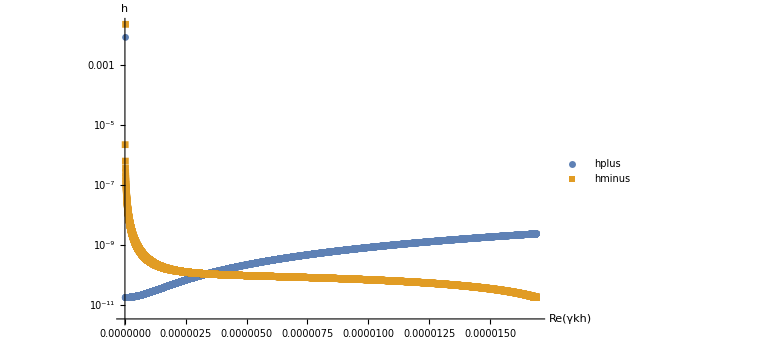

```mathematica
ListLogPlot[{hpkhbdata,hmkhbdata},
Joined->False,
ImageSize->Large,
PlotMarkers->{Automatic,Small},
AxesLabel->{"Re(γkh)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

```mathematica
AnyTrue[Re[hminuskhblist],#>0&]   (*Should Return Flase*)
AnyTrue[Re[hminuskhblist],#<0&]   (*Should Returns True*)
```

False

True

```mathematica
Select[Re[hminuskhblist],#>0&]   (*Positive elements*)
```

{4.50867×10^-12,1.39559×10^-10,4.57565×10^-10,2.0942×10^-9,2.79534×10^-9,1.5997×10^-10,7.19406×10^-10,2.1909×10^-10,3.29729×10^-10,2.65968×10^-10,3.51846×10^-10,2.82033×10^-11}

```mathematica
Position[Re[hminuskhblist],x_/;x>0]   (*Positions of positive elements*)
```

{{1568},{1569},{1573},{1575},{1577},{1592},{1597},{1599},{1601},{1602},{1604},{1606}}

```mathematica
Re[hminuskhblist[[1567]]]
```

-1.47393×10^-10

```mathematica
wp =850;
N[
SetPrecision[
hminus[SetPrecision[plotdatakh600[[1567,1]],wp],
SetPrecision[plotdatakh600[[1567,3]],wp],
SetPrecision[plotdatakh600[[1567,6]],wp],
SetPrecision[plotdatakh600[[1567,9]],wp],
SetPrecision[plotdatakh600[[1567,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatakh600[[1567,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[ plotdatakh600[[1567,14]]]+I* plotdatakh600[[1567,15]],wp]
],
wp],
wp]
```

-5.6844419946504784601449477955453185016813978010503950027047507214699254414391909348699895790445747653547039439897819441737584224788834320965627589661923423504667180301769665878316836540820217434029022557147811764676834500365626930636954235812345638426188357783960120098826529153481543237199871132094929772932947265407974242942745278950123109392409767317302030259082713255464308947765744800825134141666593673115942385168125318565816838630523623079484686106652616627436683868873656867366092168884767494574798165333374316161127162376457085407159248938019282319968568191466062052109976996335082458073268757907734583011089302587329316565100779705438555808151235000314297743500940154408409216418768956267946886908294518907159797163154175022748672070769430142160284648817226459419093408168979892226846224928866919036557635005921395326451770623815325×10^-11+0.001432013489903723398378512674927568624616092826198539589333889967608289189675962434218158338103762115988122299852275610808170810888097932084582024770491414356559470345227678945064350223148121580134730087157767976923329264663237275588018076024340996570481719525003493745432143234110925942313449933865200162396766604160499246744975999950194738189500779928403765169527149328572860534028843964242321729270222406948409438215058795377480929538194621532328649784242567600888274297486205233827928701644607785585862274082922625791077476585546429405172160912919588158951050495906162588208364495908504383777855001260228550222375024151761441749166808489750086264029863372456422842004380484464250117829943431106968699662063772063535563844067120146300247715499508835551350189200707981931925272616809061789264187190125749914836442586259639938027559719663698850272521 ⅈ

```mathematica
Re[hminuskhblist[[1568]]]
```

4.50867×10^-12

```mathematica
wp =850;
N[
SetPrecision[
hminus[SetPrecision[plotdatakh600[[1568,1]],wp],
SetPrecision[plotdatakh600[[1568,3]],wp],
SetPrecision[plotdatakh600[[1568,6]],wp],
SetPrecision[plotdatakh600[[1568,9]],wp],
SetPrecision[plotdatakh600[[1568,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatakh600[[1568,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[ plotdatakh600[[1568,14]]]+I* plotdatakh600[[1568,15]],wp]
],
wp],
wp]
```

-5.6869806917415064268856257480216563156681561980775184044976141161648076325995177219060212969556256635637855235509393259153862776309000592115814921376532805320952566899650723746813900271423304798500935897890238313233109072935914262055457139229227654148636047836508301171849382600022956145027743213309757446562383548798261353865003944097151129945584978682899995326321413948175219561591248974288186262243565705410437629524153311829128621674177218837144455721293585564808393334490961015331709753196268661868510388415018841068436633951965439782568126270907350339593870933716855659524669508339078844831039429027645599381946777974538660970694700067688413255549977115012737537790646277685325028542448632272407944829165941164082770501707316292860582153681987505042310616635428071034896601249658429546863576748114775565104238389056780483040467461191678×10^-11+0.00135390047554806267786766173213673498056550918492371730094914008943173552402083590470016135489654307924376693706702353326106394189515489623342056862131775132008282503923333239454930702524099492129666801851724521079847009872441363020174974362386982873553437039580563549162349371113692855782328903482292748369072252693575740169277547825460917079792585932007155270919376977509362113623095258338803582905205269060935364081880826462883288179293419597872534989685813590638787117113879905863871142985648654050549594531948871289090368307608379874482971448740993225983386010792327099577457054997763401507074783576741856710754540944360004441354152394492604263017257252852409333753629764351317828999745472945716490258711549372154747234688026461322306265096472999555985609307826002810901132770466032778524925273022376860156276861710694510497547835690926731625876 ⅈ

#### RT

```mathematica
plotdatart600 = Import[SystemDialogInput["FileOpen"]];
```

```mathematica
plotbrt600 = plotdatart600[[;;,12]];
plotbetart600=plotdatart600[[;;,13]];
plotgammart600 =Abs[ plotdatart600[[;;,14]]];
plotgammaimrt600=plotdatart600[[;;,15]];
plotgammanormrt600=Abs[plotdatart600[[;;,14]]/Sqrt[10]];
betadatart600=Thread[{plotbeta600,plotgammanorm600}];
bdatart600 = Thread[{plotb600,plotgamma600}];
bdataimrt600 = Thread[{plotb600,plotgammaim600}];
plotbrt600norm  = plotdatart600[[;;,12]]/√(4*π*10^-7*(plotdatart600[[1]][[1]]+plotdatart600[[1]][[2]]))*(1/600000);
plotgammanormrt600=Abs[plotdatart600[[;;,14]]/Sqrt[10]];
bdatart600norm = Thread[{plotb600norm,plotgammanorm600}];
```

```mathematica
wp=850;
hplusrtblist = 
ParallelTable[
N[
SetPrecision[
hplus[
SetPrecision[plotdatart600[[i,2]],wp],
SetPrecision[plotdatart600[[i,3]],wp],
SetPrecision[plotdatart600[[i,7]]+plotdatakh600[[i,6]],wp],
SetPrecision[plotdatart600[[i,9]],wp],
SetPrecision[plotdatart600[[i,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatart600[[i,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[plotdatart600[[i,14]]]+I*plotdatart600[[i,15]],wp]
],
wp],
wp],
{i,Length[plotdatart600]}];
hminusrtblist = ParallelTable[
N[
SetPrecision[
hminus[
SetPrecision[plotdatart600[[i,1]],wp],
SetPrecision[plotdatart600[[i,3]],wp],
SetPrecision[plotdatart600[[i,6]],wp],
SetPrecision[plotdatart600[[i,9]],wp],
SetPrecision[plotdatart600[[i,10]],wp],
SetPrecision[0,wp],
SetPrecision[plotdatart600[[i,12]],wp],
SetPrecision[4*π*10^-7,wp],
SetPrecision[Abs[plotdatart600[[i,14]]]+I*plotdatart600[[i,15]],wp]
],
wp],
wp],
{i,Length[plotdatart600]}];
```

```mathematica
hprtbdata=Thread[{plotgammart600,Re[hplusrtblist]}];
hmrtbdata=Thread[{plotgammart600,Re[hminusrtblist]}];
hmabsrtbdata=Thread[{plotgammart600,Abs[Re[hminusrtblist]]}];
```

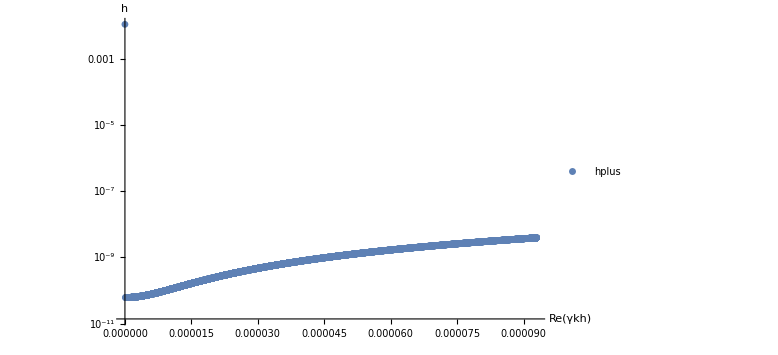

```mathematica
ListLogPlot[{hprtbdata},
Joined->False,
ImageSize->Large,
PlotMarkers->{Automatic,Small},
AxesLabel->{"Re(γkh)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

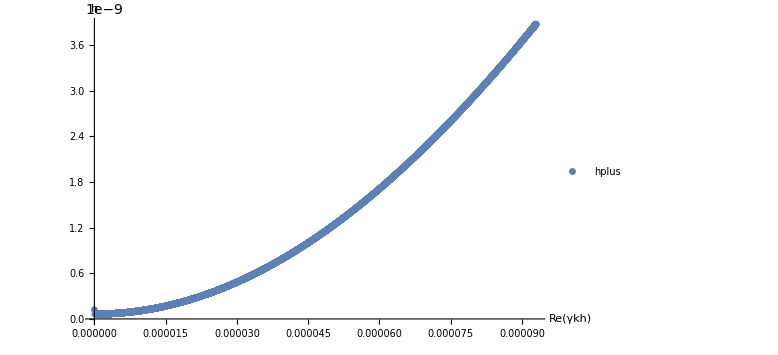

```mathematica
ListPlot[{hmrtbdata},
Joined->False,
ImageSize->Large,
PlotMarkers->{Automatic,Small},
AxesLabel->{"Re(γkh)","h"},
PlotLegends->{"hplus","hminus"},
PlotRange->Full]
```

```mathematica
AnyTrue[Re[hminusrtblist],#>0&]   (*Should Return Flase*)
AnyTrue[Re[hminusrtblist],#<0&]   (*Should Returns True*)
```

True

False

## Testing peak

```mathematica
ReplaceAll[-g(1/Subscript[c, 2]^2-1/Subscript[c, 1]^2)(g+√(g^2+4  Subscript[c, 2]^2(K^2 Subscript[c, 2]^2+ Subscript[γ̄, 2]^2)))(g-√(g^2+4 Subscript[c, 1]^2 (K^2 Subscript[c, 1]^2+ Subscript[γ̄, 1]^2)))+2  Subscript[γ̄, 1]^2 (g^2+√(g+4  Subscript[c, 2]^2(K^2 Subscript[c, 2]^2+ Subscript[γ̄, 2]^2)))-2  Subscript[γ̄, 2]^2 (g-√(g^2+4 Subscript[c, 1]^2 (K^2 Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))),{Subscript[γ̄, 1]->γ+I*kx*U1,Subscript[γ̄, 2]->γ+I*kx*U2}]
```

-2 (ⅈ kx U2+γ)^2 (g-√(g^2+4 c_1^2 ((ⅈ kx U1+γ)^2+K^2 c_1^2)))+2 (ⅈ kx U1+γ)^2 (g^2+√(g+4 c_2^2 ((ⅈ kx U2+γ)^2+K^2 c_2^2)))-g (g-√(g^2+4 c_1^2 ((ⅈ kx U1+γ)^2+K^2 c_1^2))) (-1/c_1^2+1/c_2^2) (g+√(g^2+4 c_2^2 ((ⅈ kx U2+γ)^2+K^2 c_2^2)))

```mathematica
D[-2 (ⅈ kx U2+γ)^2 (g-√(g^2+4 Subscript[c, 1]^2 ((ⅈ kx U1+γ)^2+K^2 Subscript[c, 1]^2)))+2 (ⅈ kx U1+γ)^2 (g^2+√(g+4 Subscript[c, 2]^2 ((ⅈ kx U2+γ)^2+K^2 Subscript[c, 2]^2)))-g (g-√(g^2+4 Subscript[c, 1]^2 ((ⅈ kx U1+γ)^2+K^2 Subscript[c, 1]^2))) (-1/Subscript[c, 1]^2+1/Subscript[c, 2]^2) (g+√(g^2+4 Subscript[c, 2]^2 ((ⅈ kx U2+γ)^2+K^2 Subscript[c, 2]^2))),U2]
```

-4 ⅈ kx (ⅈ kx U2+γ) (g-√(g^2+4 c_1^2 ((ⅈ kx U1+γ)^2+K^2 c_1^2)))+(8 ⅈ kx (ⅈ kx U1+γ)^2 (ⅈ kx U2+γ) c_2^2)/(√(g+4 c_2^2 ((ⅈ kx U2+γ)^2+K^2 c_2^2)))-(4 ⅈ g kx (ⅈ kx U2+γ) (g-√(g^2+4 c_1^2 ((ⅈ kx U1+γ)^2+K^2 c_1^2))) (-1/c_1^2+1/c_2^2) c_2^2)/(√(g^2+4 c_2^2 ((ⅈ kx U2+γ)^2+K^2 c_2^2)))

```mathematica
ReplaceAll[-4 ⅈ kx (ⅈ kx U2+γ) (g-√(g^2+4 Subscript[c, 1]^2 ((ⅈ kx U1+γ)^2+K^2 Subscript[c, 1]^2)))+(8 ⅈ kx (ⅈ kx U1+γ)^2 (ⅈ kx U2+γ) Subscript[c, 2]^2)/(√(g+4 Subscript[c, 2]^2 ((ⅈ kx U2+γ)^2+K^2 Subscript[c, 2]^2)))-(4 ⅈ g kx (ⅈ kx U2+γ) (g-√(g^2+4 Subscript[c, 1]^2 ((ⅈ kx U1+γ)^2+K^2 Subscript[c, 1]^2))) (-1/Subscript[c, 1]^2+1/Subscript[c, 2]^2) Subscript[c, 2]^2)/(√(g^2+4 Subscript[c, 2]^2 ((ⅈ kx U2+γ)^2+K^2 Subscript[c, 2]^2))),g->0]//Simplify
```

4 ⅈ kx (ⅈ kx U2+γ) (2 √(c_1^2 (-(kx U1-ⅈ γ)^2+K^2 c_1^2))+((ⅈ kx U1+γ)^2 c_2^2)/(√(c_2^2 ((ⅈ kx U2+γ)^2+K^2 c_2^2))))

```mathematica
Solve[2 Subscript[c, 1] √(-(-kx U2-ⅈ γ)^2+K^2 Subscript[c, 1]^2)+((-ⅈ kx U2+γ)^2 Subscript[c, 2])/(√((ⅈ kx U2+γ)^2+K^2 Subscript[c, 2]^2))==0,U2]//Simplify
```

$Aborted

## Compressible KH w/ and w/o g varying k

### A = 0.9

```mathematica
ky=0;
g=10;
g0 = 0;
U1 = 0;
c1=87178;
c2=20000;
```

```mathematica
N[Solve[200==ρ1*20000^2]]
```

```mathematica
N[Solve[200==ρ2*87178^2]]
```

```mathematica
krange =Range[0.1,5,0.25];
```

```mathematica
krange
```

{0.1,0.35,0.6,0.85,1.1,1.35,1.6,1.85,2.1,2.35,2.6,2.85,3.1,3.35,3.6,3.85,4.1,4.35,4.6,4.85}

```mathematica
U2=2000;
a1 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))==0],{kx,krange}];
khrootk1 = Flatten[a1[[;;,-1]]];
khrootkdata1 = Abs[Re[khrootk1[[All,2]]]];
plotdata1 = Thread[{krange,khrootkdata1}];
```

```mathematica
plotdata1
```

{{0.1,43.5854},{0.35,152.575},{0.6,261.564},{0.85,370.553},{1.1,479.543},{1.35,588.532},{1.6,697.521},{1.85,806.511},{2.1,915.5},{2.35,1024.49},{2.6,1133.48},{2.85,1242.47},{3.1,1351.46},{3.35,1460.45},{3.6,1569.44},{3.85,1678.43},{4.1,1787.41},{4.35,1896.4},{4.6,2005.39},{4.85,2114.38}}

```mathematica
N[2000/(c1+c2)]
```

0.0186605

```mathematica
U2=20000;
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))==0],{kx,krange}];
khrootk2 = Flatten[a2[[;;,1]]];
khrootkdata2 = Abs[Re[khrootk2[[All,2]]]];
plotdata2 = Thread[{krange,khrootkdata2}];
```

```mathematica
N[20000/(c1+c2)]
```

0.186605

```mathematica
U2=70000;
a3 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))==0],{kx,krange}];
khrootk3 = Flatten[a3[[;;,1]]];
khrootkdata3 = Abs[Re[khrootk3[[All,2]]]];
plotdata3 = Thread[{krange,khrootkdata3}];
```

```mathematica
N[70000/(c1+c2)]
```

0.653119

```mathematica
U2=130000;
a4 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))==0],{kx,krange}];
khrootk4 = Flatten[a4[[;;,1]]];
khrootkdata4 = Abs[Re[khrootk4[[All,2]]]];
plotdata4 = Thread[{krange,khrootkdata4}];
```

```mathematica
N[130000/(c1+c2)]
```

1.21294

```mathematica
U2=175000;
a5 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (U2)+γ)^2))==0],{kx,krange}];
khrootk5 = Flatten[a5[[;;,-1]]];
khrootkdata5 = Abs[Re[khrootk5[[All,2]]]];
plotdata5 = Thread[{krange,khrootkdata5}];
```

```mathematica
N[175000/(c1+c2)]
```

1.6328

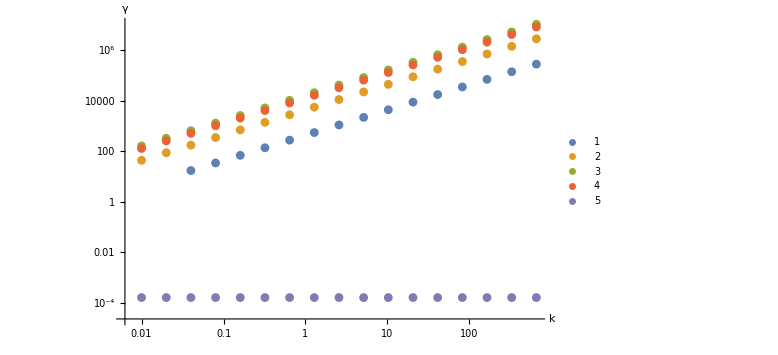

```mathematica
ListLogLogPlot[{plotdata1,plotdata2,plotdata3,plotdata4,plotdata5},
Joined->False,
PlotStyle->Thickness[0.007],
AxesStyle->{Thick,Bold},
AxesLabel->{Style[k,Bold,24],Style[γ,Bold,24]},
PlotLegends->Automatic,
ImageSize->Large]
```

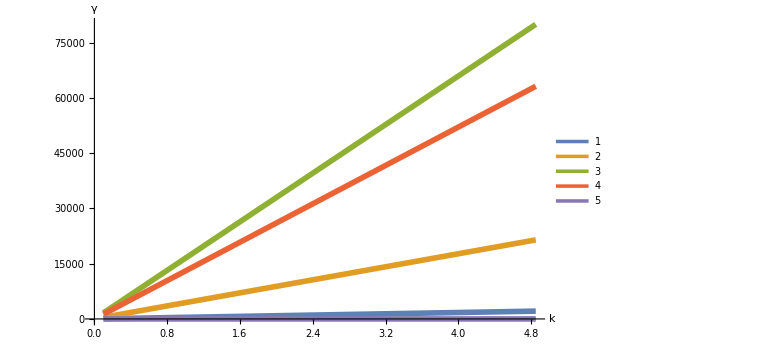

```mathematica
ListPlot[{plotdata1,plotdata2,plotdata3,plotdata4,plotdata5},
Joined->True,
PlotStyle->Thickness[0.007],
AxesStyle->{Thick,Bold},
AxesLabel->{Style[k,Bold,24],Style[γ,Bold,24]},
PlotLegends->Automatic,
ImageSize->Large]
```

```mathematica
khrootk[[All,2]]
```

{79.6493-172.748 ⅈ,-79.6493-172.748 ⅈ,-79.6482-172.748 ⅈ,79.6482-172.748 ⅈ,159.298-345.496 ⅈ,-159.298-345.496 ⅈ,-159.297-345.496 ⅈ,159.297-345.496 ⅈ,318.596-690.993 ⅈ,-318.596-690.993 ⅈ,637.191-1381.99 ⅈ,-637.191-1381.99 ⅈ,-1274.38-2763.97 ⅈ,1274.38-2763.97 ⅈ,2548.76-5527.94 ⅈ,-2548.76-5527.94 ⅈ,-5097.52-11055.9 ⅈ,5097.52-11055.9 ⅈ,10195.-22111.8 ⅈ,-10195.-22111.8 ⅈ,-20390.1-44223.5 ⅈ,20390.1-44223.5 ⅈ,-40780.2-88447.1 ⅈ,40780.2-88447.1 ⅈ,-81560.3-176894. ⅈ,81560.3-176894. ⅈ,-163121.-353788. ⅈ,163121.-353788. ⅈ,326241.-707577. ⅈ,-326241.-707577. ⅈ,-652483.-1.41515×10^6 ⅈ,652483.-1.41515×10^6 ⅈ,-1.30497×10^6-2.83031×10^6 ⅈ,1.30497×10^6-2.83031×10^6 ⅈ,2.60993×10^6-5.66061×10^6 ⅈ,-2.60993×10^6-5.66061×10^6 ⅈ,-5.21986×10^6-1.13212×10^7 ⅈ,5.21986×10^6-1.13212×10^7 ⅈ}

```mathematica
khroot2 = Flatten[Append[a2[[1;;152,1]],a2[[153;;All,3]]]];
rtroot2=  Flatten[Append[a2[[109;;152,3]],a2[[153;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,d2range}];
khrootdata2=khroot2[[All,2]];
rtrootdata2 = rtroot2[[All,2]];
normkhdata = Rescale[Abs[Re[khrootdata2]]];
normrtdata = Rescale[Abs[Re[rtrootdata2]]];
data5=Thread[{dvals2,normkhdata}];
data7 = Thread[{dvals2[[109;;All]],normrtdata}];
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+√(1+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1)))+2 p0 (ⅈ k U1+γ)^2 (1+√(1+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/(g^2 ρ2)))-g^2 (-1+√(1+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (1+√(1+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/(g^2 ρ2))) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+√(1/g^2(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1)))+2 p0 (ⅈ k U1+γ)^2 (1+√(1/g^2(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)))-g^2 (-1+√(1/g^2(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1)))) (1+√(1/g^2(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2)g ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-1+1/g √(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (1+1/g √(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))-g^2 (-1+1/g √(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (1+1/g √(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)) (ρ1-ρ2)) ρ2
```

```mathematica
1/(4 p0^2) ρ1 (-2 p0 (k U2-ⅈ γ)^2 (-g+√(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (g+√(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))- g(-g+√(g^2+(4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/(g^2 ρ1))) (g+√(g^2+(4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2)) (ρ1-ρ2)) ρ2
```

Set g=0

```mathematica
1/(4 p0^2) ρ1 (-2 p0 (k U2-ⅈ γ)^2 (√((4 p0 ((ⅈ k U1+γ)^2+(k^2 p0)/ρ1))/ρ1))+2 p0 (ⅈ k U1+γ)^2 (√((4 p0 ((ⅈ k U2+γ)^2+(k^2 p0)/ρ2))/ρ2))) ρ2
```

```mathematica
(-(k U2-ⅈ γ)^2 (√(4  c1^2((ⅈ k U1+γ)^2+k^2 c1^2)))+(ⅈ k U1+γ)^2 (√(4 c2^2((ⅈ k U2+γ)^2+k^2 c2^2))))
```

```mathematica
-(k U2-ⅈ γ)^2 (2 c1 √((ⅈ k U1+γ)^2+k^2 c1^2))+(ⅈ k U1+γ)^2 (2 c2 √((ⅈ k U2+γ)^2+k^2 c2^2)) 
-c1(k U2-ⅈ γ)^2  √((ⅈ k U1+γ)^2+k^2 c1^2)+c2(ⅈ k U1+γ)^2  √((ⅈ k U2+γ)^2+k^2 c2^2)
 c1^2(ⅈ k U2+ γ)^4  ((ⅈ k U1+γ)^2+k^2 c1^2)-c2^2(ⅈ k U1+γ)^4  ((ⅈ k U2+γ)^2+k^2 c2^2)
```

```mathematica
testdata = Thread[{dvals2,Abs[Re[test]]}];
```

```mathematica
N[kx*(c1+c2)/(c1^2+c2^2) c1 c2*√(-1-(d/(c1+c2))^2+√(1+4(d/(c1+c2))^2))]
```

```mathematica
Solve[k* c11 c22*√(-1-Mc^2+√(1+4Mc^2))==0,Mc]
```

```mathematica
Manipulate[{NSolve[-(kx (d+U1)-ⅈ γ)^2 (√(4  c1^2((ⅈ kx U1+γ)^2+kx^2 c1^2)))+(ⅈ kx U1+γ)^2 (√(4 c2^2((ⅈ kx (d+U1)+γ)^2+kx^2 c2^2)))==0],d},{d,0,140522.3461650872}]
```

```mathematica
dt=140522.3461650885103145;
FindRoot[-(SetPrecision[kx,64]*(SetPrecision[dt,64]+SetPrecision[U1,64])-ⅈ γ)^2 (√(SetPrecision[4,64]  SetPrecision[c1,64]^2((ⅈ SetPrecision[kx,64] SetPrecision[U1,64]+γ)^2+SetPrecision[kx,64]^2 SetPrecision[c1,64]^2)))+(ⅈ SetPrecision[kx,64] SetPrecision[U1,64]+γ)^2 (√(SetPrecision[4,64] SetPrecision[c2,64]^2((ⅈ SetPrecision[kx,64] (SetPrecision[dt,64]+SetPrecision[U1,64])+γ)^2+SetPrecision[kx,64]^2 SetPrecision[c2,64]^2)))==0,{γ,0.01-53306*I},PrecisionGoal->8,AccuracyGoal->8,WorkingPrecision->60,MaxIterations->10000]
```

```mathematica
140522.3461650872
```

```mathematica
140522.3461650875
```

```mathematica
140522.346
```

```mathematica
140522.34616000002
```

```mathematica
140522.346165
```

```mathematica
140522.346165084
```

```mathematica
140522.34616508702
```

```mathematica
140522.34616508716
```

```mathematica
d22range = Range[0,140000,1000];
d23range = Range[140000,140500,100];
d24range = Range[140500,140522,1];
d25range = Range[140522,140522.34,0.01];
d26range = Range[140522.34,140522.345,0.001];
d2nogrange = Flatten[Append[Append[Append[Append[d22range,d23range],d24range],d25range],d26range]];
```

```mathematica
a22nog = ParallelTable[NSolve[-(kx (d+U1)-ⅈ γ)^2 (√(4  c1^2((ⅈ kx U1+γ)^2+kx^2 c1^2)))+(ⅈ kx U1+γ)^2 (√(4 c2^2((ⅈ kx (d+U1)+γ)^2+kx^2 c2^2)))==0],{d,d2nogrange}];
```

```mathematica
dvalextra={140522.3461650885/(c1+c2),140522.3461650885102/(c1+c2),140522.3461650885103145/(c1+c2)};
khextra = {0.00043508984982895904772041967411094799097687570695158815941555217935336217655`60.-53306.14613807765356389615328291548165144863713365812041521263133824012089910551387`60. ⅈ,0.00004717691446651267431065305082518887571963579042339905027736169851710004517`60.-53306.14613807765834480765014339037926108684405918647884201768890475141840908414182`60. ⅈ,9.93541618824217721137522472564194144480473444881694062021126299178152099`60.*^-6-53306.1461380776583991794064808303133749849407162204834760927499072434312836234617`60. ⅈ};
dvals22 = Table[d/(c1+c2),{d,d2nogrange}];
dvals222 = Flatten[Append[dvals22,dvalextra]];
khrootdata22=Flatten[Append[a22nog[[All,2,1,2]],khextra]];
normkhnogdata = Rescale[Abs[Re[khrootdata22]]];
dvals222[[1]] = 0;
normkhnogdata[[1]] = 5*10^-10
data55=Thread[{dvals222,normkhnogdata}];
```

```mathematica
dvals222[[1]] = 2
```

```mathematica
data55[[3]]
```

```mathematica
combinedplot1=ListLogPlot[{data5,data55},
Joined->True,
PlotLegends->SwatchLegend[{Style["KHI w/ g",Bold,30],Style["KHI w/o g",Bold, 30],Style["KHI No g",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Directive[Thickness[0.017],Blue], Directive[Thickness[0.0075],Orange],Directive[Thickness[0.005],Red]},
AxesStyle->Directive[24,Bold,Thick],
PlotRange->{Automatic,{5*10^-10,2}},
AxesLabel->{Style["M_c",Large,Bold,Blue],Style[γ/Subscript[γ, max],Large,Bold,Blue]},
GridLinesStyle->Directive[Black, Thick,Bold],
Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,-11,4}]},
ImageSize->800]
```

```mathematica
Export["combined_plot1_2.eps",combinedplot1,"EPS"]
```

```mathematica
ListLogPlot[{data5,testdata,data55},
PlotMarkers->{{●,20},{Automatic,10},{•,7}},
PlotLegends->SwatchLegend[{Style["KHRTI",Bold,30],Style["RTI-Like",Bold, 30],Style["KHI No g",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
PlotStyle->{Blue, Orange,Red},
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[M,c],Large,Bold,Blue],Style[γ,Large,Bold,Blue]},
GridLines->{{1.312},{}},
GridLinesStyle->Directive[Black, Thick,Bold],
Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,-5,4}]},
ImageSize->800]
```

## Calculate Numerical Roots for A=0.1

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=22110.8;
```

```mathematica
N[(c2^2-c1^2)/(c1^2+c2^2)]
```

```mathematica
hplus[g_,c2_,kx_,U2_,γ_]:=(g+√(g^2+4 c2^4 kx^2+4 c2^2 (γ+I*kx*U2)^2));
hminus[g_,c1_,kx_,U1_,γ_]:=(g-√(g^2+4 c1^4 K^2+4 c1^2 (γ+I*kx*U1)^2));
```

```mathematica
drange =Range[-590000,590000,548];
```

```mathematica
a =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,drange}];
```

```mathematica
a =ParallelTable[NSolve[-1/c1^2+1/c2^2+((-ⅈ kx d+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(-ⅈ kx d+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(-ⅈ kx d+γ)^2))+((ⅈ kx (d)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx d+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx d+γ)^2))==0,WorkingPrecision->64],{d,drange}];
```

```mathematica
TableForm[a[[1;;10]]]
```

γ→0.000023850962488106179724879272079369435119674360999834319-29573.69605896824566601511980514453492272912672125152963389383 ⅈ | γ→-0.000023850962488106179724879272079369435119674360999834319-29573.69605896824566601511980514453492272912672125152963389383 ⅈ
γ→-0.000023850934199175188385135344019828405991227921460317601-29546.22760906940736324293537522361660773281548346000956010759 ⅈ | γ→0.000023850934199175188385135344019828405991227921460317601-29546.22760906940736324293537522361660773281548346000956010759 ⅈ
γ→-0.00002385090583120163701772746273016331447148078033539342-29518.75915917056906047073419998034605972363186425781209605904 ⅈ | γ→0.00002385090583120163701772746273016331447148078033539342-29518.75915917056906047073419998034605972363186425781209605904 ⅈ
γ→0.000023850877383890747429861232865421765689543969117418636-29491.29070927173075769851623262569755356236972877888180767803 ⅈ | γ→-0.000023850877383890747429861232865421765689543969117418636-29491.29070927173075769851623262569755356236972877888180767803 ⅈ
γ→0.00002385084885694636583112202806248233629461609752293943-29463.8222593728924549262814261961695960773865848193184398826 ⅈ | γ→-0.00002385084885694636583112202806248233629461609752293943-29463.8222593728924549262814261961695960773865848193184398826 ⅈ
γ→-0.000023850820250070955122292750811505298279499275772976982-29436.35380947405415215402973355297089963075507682440694828538 ⅈ | γ→0.000023850820250070955122292750811505298279499275772976982-29436.35380947405415215402973355297089963075507682440694828538 ⅈ
γ→-0.000023850791562965587133688017753546382017014197284422101-29408.88535957521584938176110738120179399436991979584954133499 ⅈ | γ→0.000023850791562965587133688017753546382017014197284422101-29408.88535957521584938176110738120179399436991979584954133499 ⅈ
γ→-0.000023850762795329934812626654869746388336019851204847062-29381.41690967637754660947550018903104668473926643473212942523 ⅈ | γ→0.000023850762795329934812626654869746388336019851204847062-29381.41690967637754660947550018903104668473926643473212942523 ⅈ
γ→-0.000023850733946862264359661197654117507958146926856848702-29353.94845977753924383717286430686806168173186478205107044607 ⅈ | γ→0.000023850733946862264359661197654117507958146926856848702-29353.94845977753924383717286430686806168173186478205107044607 ⅈ
γ→0.000023850705017259427313179872066035137907709805535773387-29326.4800098787009410648531518865304262312101485705807234547 ⅈ | γ→-0.000023850705017259427313179872066035137907709805535773387-29326.4800098787009410648531518865304262312101485705807234547 ⅈ

```mathematica
N[29573.696058968246/(20000+22110.8)]
```

0.702283

```mathematica
N[29573.696058968246/20000]
```

1.47868

```mathematica
data3[[1]]
```

0.702283

```mathematica
(*TableForm[a]*)
```

```mathematica
a[[All,1,1,2]]
```

```mathematica
data1[[1]]
```

{γ→0.000023851-29573.7 ⅈ}

```mathematica
data1 = a[[All,1,1,2]];
data2 = Abs[Re[data1]]/(kx);
data3 = Im[data1]/(kx*c1);
dvals = Table[d/c1,{d,drange}];
plotdata = Thread[{dvals,data2}];
plotdata2 = Thread[{dvals,data3}];
```

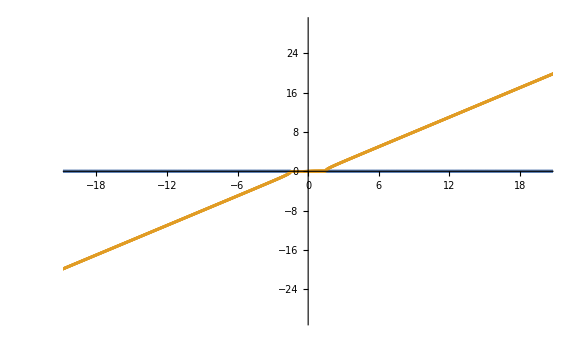

```mathematica
ListPlot[{plotdata,plotdata2},PlotRange->{{-20,20},{-30,30}},ImageSize->Large]
```

```mathematica
khroot = Flatten[Append[a[[1;;33,1]],a[[34;;All,3]]]];
rtroot=  Flatten[Append[a[[2;;33,3]],a[[34;;All,1]]]];
dvals = Table[d/(c1+c2),{d,drange}];
```

```mathematica
khrootdata = khroot[[All,2]]/Sqrt[g*kx];
rtrootdata = rtroot[[All,2]]/Sqrt[g*kx];
khapprox = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,drange}];
rtapprox = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,drange}];
```

```mathematica
data = Thread[{dvals,Abs[Re[khrootdata]]}];
data2 = Thread[{dvals,khapprox}];
data3 = Thread[{dvals[[2;;All]],Abs[Re[rtrootdata]]}];
data4 = Thread[{dvals,rtapprox}];
```

### Plot KH

```mathematica
KHA001=ListPlot[{data,data2},
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00003,0.000001],{#,ScientificForm@#}&/@Range[0,0.00003,0.000005]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue, Orange},AxesStyle->Directive[24,Bold,Thick],ImageSize->800]
```

### Plot RT?

```mathematica
RTA001=ListPlot[{data3,data4}, 
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00008,0.0000005],{#,ScientificForm@#}&/@Range[0,0.000008,0.0000015]]},
AxesOrigin->{0,0},PlotRange->{0,0.0000085},
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style[Subscript[M, c],Large,Bold,Blue],Style[γ̂,Large,Bold,Blue]},
PlotStyle->{Blue,Orange},
ImageSize->800,
AxesStyle->Directive[24,Thick,Bold]]
```

### Plot Relative Error KH

```mathematica
kherror = Abs[Abs[Re[khrootdata]]-khapprox]/Abs[Re[khrootdata]]*100;
kherrordata = Thread[{dvals,kherror}];
```

```mathematica
KHERA001=ListPlot[{kherrordata},
Joined->True,
AxesStyle->Directive[Bold,26,Thick],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
PlotStyle->{Directive[Black,Thickness[0.01]]},
Ticks->{Automatic,{10,20,30,40}},
GridLines->{{2,4,6,8,10,12,14},{5,10,15,20,25,30,35}},
GridLinesStyle->Directive[Blue,Dashed],
ImageSize->800];
```

### Plot Relative Error RT?

```mathematica
rterror = Abs[Abs[Re[rtrootdata]]-rtapprox[[2;;All]]]/Abs[Re[rtrootdata]]*100;
rterrordata = Thread[{dvals[[2;;All]],rterror}];
```

```mathematica
RTERA001=ListPlot[{rterrordata},
Joined->True,
AxesStyle->Directive[Bold,26,Thick],
AxesLabel->{Style["M_c",34,Bold,Blue],Style["Relative Error %",Large,Bold,Blue]},
PlotStyle->{Directive[Black,Thickness[0.01]]},
GridLines->{{2,4,6,8,10,12,14},{2,4,6,8,10,12}},
GridLinesStyle->Directive[Blue,Dashed],
ImageSize->800];
```

### Getting plot insert

```mathematica
KHA001=ListPlot[{data,data2},
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00003,0.000001],{#,ScientificForm@#}&/@Range[0,0.00003,0.000005]]},PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
AxesStyle->Directive[24,Bold,Thick],
ImageSize->800,
Epilog->Inset[KHERA001,Scaled[{1,1}],{Right,Top},Scaled[{0.75,0.75}]]]
```

```mathematica
Export["KH_A_0.1_Full_3.eps",KHA001,"EPS"]
```

```mathematica
RTA001=ListPlot[{data3,data4}, 
Joined->True,
Ticks->{Automatic,Join[{#,"",{0.006,0.}}&/@Range[0,0.00008,0.0000005],{#,ScientificForm@#}&/@Range[0,0.000008,0.0000015]]},
AxesOrigin->{0,8.25*10^-6},
PlotRange->{0,0.0000085},
PlotLegends->SwatchLegend[{Style["Numerical",Bold,30],Style["Analytic",Bold, 30]},LegendMarkerSize->24,LegendMarkers->"Bubble"],
AxesLabel->{Style["M_c",Large,Bold,Blue],Style["γ̂",Large,Bold,Blue]},
PlotStyle->{Directive[Blue,Thickness[0.008]], Directive[Orange,Thickness[0.008]]},
ImageSize->800,
AxesStyle->Directive[24,Thick,Bold],
Epilog->Inset[RTERA001,Scaled[{0.17,0.05}],{Left,Bottom},Scaled[{0.76,0.76}]]
]
```

```mathematica
Export["RT_A_0.1_Full_3.eps",RTA001,"EPS"]
```

### Getting More Data for Absolute Error With log spacing

```mathematica
lnspace[a_,b_,n_]:=N[Exp[1]^Range[a,b,(b-a)/(n-1)]];
```

```mathematica
logrange = lnspace[13.29,16,1000];
fullrange = Join[drange,logrange];
```

```mathematica
a =ParallelTable[NSolve[SetPrecision[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0,200],WorkingPrecision->200],{d,fullrange}];
```

```mathematica
khroot = Flatten[Append[a[[1;;33,1]],a[[34;;All,3]]]];
rtroot=  Flatten[Append[a[[2;;33,3]],a[[34;;All,1]]]];
dvals = Table[d/(c1+c2),{d,fullrange}];
```

```mathematica
khrootdata = khroot[[All,2]]/Sqrt[g*kx];
rtrootdata = rtroot[[All,2]]/Sqrt[g*kx];
khapprox = Table[N[(g*c2)/(2*c1*d)/Sqrt[g*kx]],{d,fullrange}];
rtapprox = Table[N[g/2(1/c1-1/c2)/Sqrt[g*kx]],{d,fullrange}];
```

```mathematica
khabserror = Abs[Abs[Re[khrootdata]]-khapprox];
rtabserror=Abs[Abs[Re[rtrootdata]]-rtapprox[[2;;All]]];
```

```mathematica
khabserrordata = Thread[{1/dvals,khabserror}];
rtabserrordata= Thread[{1/dvals[[2;;All]],rtabserror}];
```

#### KH Abs Error Plot

```mathematica
ListLogLogPlot[khabserrordata,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange},PlotRange->{{4*10^-3,0.7},{3*10^-10,10^-3}}]
```

#### RT Abs Error Plot

```mathematica
ListLogLogPlot[rtabserrordata,ImageSize->800,AxesStyle->Directive[Bold,30,Thick],AxesLabel->{Style[1/Subscript[M, c],34,Bold,Blue],Style["Absolute Error",Large,Bold,Blue]},PlotStyle->{Orange}]
```

```mathematica
Manipulate[N[(Log[rtabserrordata[[x,2]]]-Log[rtabserrordata[[2000,2]]])/(Log[rtabserrordata[[x,1]]]-Log[rtabserrordata[[2000,1]]])],{x,400,2000}]
```

## h+- plot

```mathematica
hplusnorm[L_,M2_,γ_]:=1/(2 L)+ √(1+1/(4 L^2)+(γ+I*M2)^2);
hminusnorm[L_,M1_,γ_]:=1/(2 L)-√(1+1/(4 L^2)+(γ+I*M1)^2);
gammanorm[L_,M1_,Mc_]:=  ⅈ   (-(M1+Mc)+√((- ⅈ)/(2 L)+1+(Mc)^2-√((1-ⅈ/(2 L))^2+4 Mc^2)));
hplusnognorm[M2_,γ_]:=√(1+ (γ+I*M2)^2)
hminusnognorm[M1_,γ_]:=-√(1+ (γ+I*M1)^2)
gammanognorm[M1_,Mc_]:=I(-(M1+Mc)-√(Mc^2+1-√(1+4 Mc^2)));
```

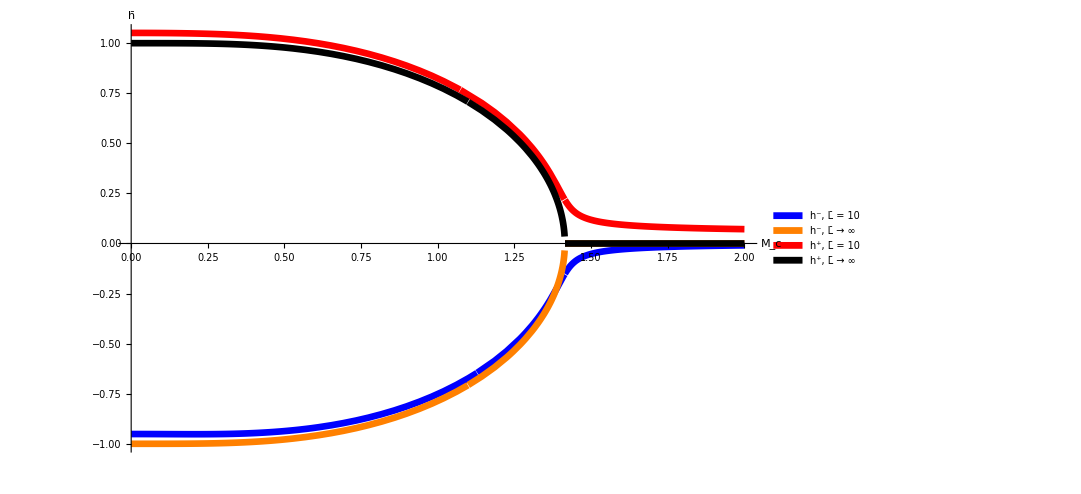

```mathematica
L=10;
M1=1;
hplusminus=Plot[{
Re[N[hminusnorm[L,M1,gammanorm[L,M1,Mc]]]],
Re[N[hminusnognorm[M1,gammanognorm[M1,Mc]]]],
Re[N[hplusnorm[L,M1+2*Mc,gammanorm[L,M1,Mc]]]],
Re[N[hplusnognorm[M1+2*Mc,gammanognorm[M1,Mc]]]]},
{Mc,0,2},
ImageSize->800,
PlotStyle->{Directive[Blue,Thickness[0.006]],Directive[Orange,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]},
PlotLegends->{SwatchLegend[{Style["h^-, L̄ = 10",Bold,20],Style["h^-, L̄ → ∞",Bold,20],Style["h^+, L̄ = 10",Bold,20],Style["h^+, L̄ → ∞",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"]},
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["h̄",Blue,Bold,24]}
]
```

```mathematica
Export["hplusminus.eps",hplusminus,"EPS"]
```

hplusminus.eps

## e^h+-

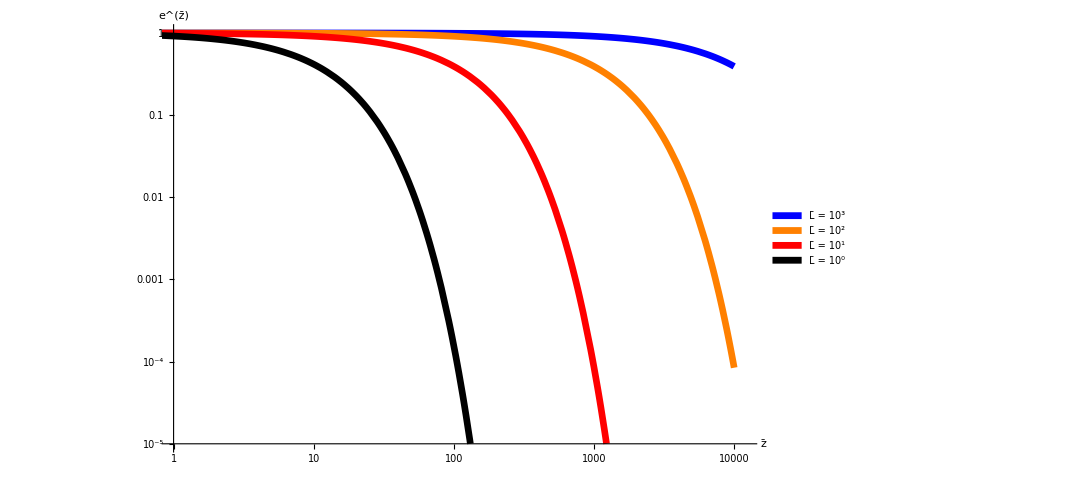

```mathematica
M1=1;
L1=1000;
L2=100;
L3=10;
L4=1;
eigenfun=LogLogPlot[{
Re[Exp[z*Re[N[hminusnorm[L1,M1,gammanorm[L1,M1,2]]]]]],
Re[Exp[z*Re[N[hminusnorm[L2,M1,gammanorm[L2,M1,2]]]]]],
Re[Exp[z*Re[N[hminusnorm[L3,M1,gammanorm[L3,M1,2]]]]]],
Re[Exp[z*Re[N[hminusnorm[L4,M1,gammanorm[L4,M1,2]]]]]]},
{z,0.1,10000},
ImageSize->800,
PlotRange->{{1,12000},{10^-5,1}},
PlotStyle->{Directive[Blue,Thickness[0.006]],Directive[Orange,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]},
PlotLegends->{SwatchLegend[{Style["L̄ = 10^3",Bold,20],Style["L̄ = 10^2",Bold,20],Style["L̄ = 10^1",Bold,20],Style["L̄ = 10^0",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"]},
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["z̄",Bold,Blue,24],Style["e^(z̄)",Blue,Bold,24]}
]
```

```mathematica
Export["eigenfun.eps",eigenfun,"EPS"]
```

eigenfun.eps

## Peak movement due to gravity

```mathematica
gammanorm[L_,M1_,Mc_]:=  ⅈ   (-(M1+Mc)+√((- ⅈ)/(2 L)+1+(Mc)^2-√((1-ⅈ/(2 L))^2+4 Mc^2)));
hplusnognorm[M2_,γ_]:=√(1+ (γ+I*M2)^2)
hminusnognorm[M1_,γ_]:=-√(1+ (γ+I*M1)^2)
gammanognorm[M1_,Mc_]:=I(-(M1+Mc)-√(Mc^2+1-√(1+4 Mc^2)));
```

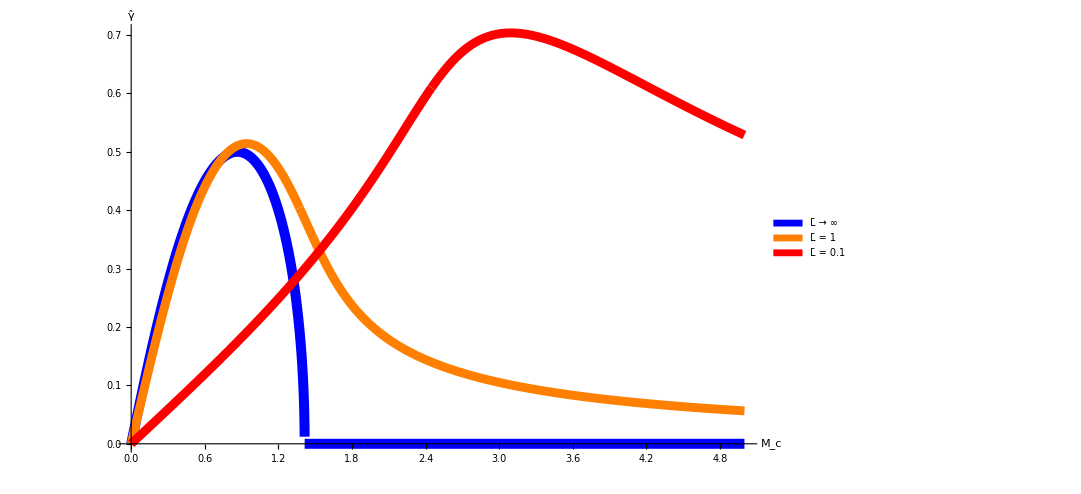

```mathematica
gravpeak=Plot[{Re[gammanognorm[M1,Mc]],
Re[gammanorm[1,M1,Mc]],
Re[gammanorm[0.1,M1,Mc]]},
{Mc,0,5},
ImageSize->800,
PlotRange->All,
PlotPoints->500,
PlotStyle->{Directive[Blue,Thickness[0.009]],Directive[Orange,Thickness[0.008]],Directive[Red,Thickness[0.008]]},
PlotLegends->{SwatchLegend[{Style["L̄ → ∞",Bold,20],Style["L̄ = 1",Bold,20],Style["L̄ = 0.1",Bold,20]},LegendMarkerSize->20,LegendMarkers->"Bubble"]},
AxesStyle->Directive[24,Thick,Bold],
AxesLabel->{Style["M_c",Bold,Blue,24],Style["γ̂",Blue,Bold,24]}]
```

```mathematica
Export["gravpeak.eps",gravpeak,"EPS"]
```

gravpeak.eps

```mathematica
N[20000^2/10]
```

4.×10^7